## Instability Analysis

### 1. Initialization commands

```mathematica
Block[{Print},<<xAct`xTensor`];
Block[{Print},<<xAct`xPert`];
Block[{Print},<<xAct`xPand`];
Block[{Print},<<xAct`xCoba`];
Block[{Print},<<xAct`xTras`];
$PrePrint=ScreenDollarIndices;

DefManifold[M,4,{α,β,μ,ν,λ,σ,γ,τ,χ,η,κ,ζ}]
DefMetric[-1,g[-α,-β],CD,{";","∇"},PrintAs->"ḡ"];
DefMetricPerturbation[g,dg,ε];
PrintAs[dg]^="h";

DefManifold[M1,4,{b,c,d,e,f,l,m,n,p,q,r,s,u,v}]
DefMetric[1,g1[-b,-c],PD,{",","∂"},FlatMetric->True,PrintAs->"g1"]
DefMetricPerturbation[g1,dg1,ε];
PrintAs[dg1]^="δg1";
```

```mathematica
DefTensor[A[-μ,b],{M,M1}]
pertvforder[order_]:=DefTensorPerturbation[pertvf[LI[order],-μ,b],A[-μ,b],M]
pertvforder[1];
PrintAs[pertvf]^="δA";
```

** DefTensor: Defining tensor A[-μ,b].

** DefTensor: Defining tensor pertvf[LI[order],-μ,b].

```mathematica
DefConstantSymbol[gpar]
DefConstantSymbol[alpha];
DefConstantSymbol[kappa];
DefConstantSymbol[lambda];
DefConstantSymbol[theta];
DefConstantSymbol[gamma];
DefConstantSymbol[beta];

PrintAs[alpha]^="α^OverTilde[~]";
PrintAs[kappa]^="κ^OverTilde[~]";
PrintAs[lambda]^="λ^OverTilde[~]";
PrintAs[theta]^="(θ^OverTilde[~])_4";
PrintAs[gamma]^="(Θ^OverTilde[~])_1";
PrintAs[beta]^="β^OverTilde[~]";
```

** DefConstantSymbol: Defining constant symbol gamma.

```mathematica
Ruledg1frs=MakeRule[{dg1[LI[1],-b,-c],0},MetricOn->All];
Ruledg1snd=MakeRule[{dg1[LI[2],-b,-c],0},MetricOn->All];
CheckZeroDerivativeStart[CD]
```

```mathematica
Ruledg=MakeRule[{dg[LI[1],-α,-β],dg[-α,-β]},MetricOn->All]
RuledA=MakeRule[{pertvf[LI[1],-μ,b],pertvf[-μ,b]},MetricOn->All]
```

{HoldPattern[h | 1 | UnderBar[α̲] | UnderBar[β̲]
  |   |  ]:>Module[{},h | α | β
  |  ]}

{HoldPattern[δA | 1 | UnderBar[μ̲] | UnderBar[b̲]
  |   |  ]:>Module[{},δA | μ | b
  |  ]}

### 2. Total perturbed L_41up to second order for metric perturbations:

```mathematica
(1/8 √(-Overscript[ḡ, OverTilde[~]]){{A, {{, }, {α, b}}}} {{A, {{α, b}, {, }}}} 8 {{g1, {{, }, {c, d}}}} ∇_β {{δA, {{1, β, c}, {, , }}}} ∇_γ {{δA, {{1, γ, d}, {, , }}}}+1/16 √(-Overscript[ḡ, OverTilde[~]]){{A, {{, }, {α, b}}}} {{A, {{α, b}, {, }}}}( 8 {{g1, {{, }, {c, d}}}} ∇_β {{δA, {{1, , d}, {, γ, }}}} ∇^γ {{δA, {{1, β, c}, {, , }}}}+8 {{g1, {{, }, {c, d}}}} ∇_γ {{δA, {{1, , d}, {, β, }}}} ∇^γ {{δA, {{1, β, c}, {, , }}}})+1/4 √(-Overscript[ḡ, OverTilde[~]]){{A, {{, c}, {α, }}}} {{A, {{α, b}, {, }}}}8 ∇_β {{δA, {{1, β, }, {, , b}}}} ∇_γ {{δA, {{1, γ, }, {, , c}}}}+1/8 √(-Overscript[ḡ, OverTilde[~]]) {{A, {{, c}, {α, }}}} {{A, {{α, b}, {, }}}}(8 ∇_β {{δA, {{1, , }, {, γ, c}}}} ∇^γ {{δA, {{1, β, }, {, , b}}}}+8 ∇_γ {{δA, {{1, , }, {, β, c}}}} ∇^γ {{δA, {{1, β, }, {, , b}}}}))/.Ruledg/.RuledA//ContractMetric//Factor
```

1/2 A | α | b
  |   √(-ḡ^OverTilde[~]) (4 A |   | c
α |   ∇_β δA | β |  
  | b ∇_γ δA | γ |  
  | c+2 A |   |  
α | b ∇_β δA | β |  
  | d ∇_γ δA | γ | d
  |  +2 A |   | c
α |   ∇_β δA |   |  
γ | c ∇^γ δA | β |  
  | b+2 A |   | c
α |   ∇_γ δA |   |  
β | c ∇^γ δA | β |  
  | b+A |   |  
α | b ∇_β δA |   |  
γ | c ∇^γ δA | β | c
  |  +A |   |  
α | b ∇_γ δA |   |  
β | c ∇^γ δA | β | c
  |  )

```mathematica
2 {{A, {{, c}, {α, }}}} {{A, {{α, b}, {, }}}} √(-Overscript[ḡ, OverTilde[~]]) ∇_β {{δA, {{β, }, {, b}}}} ∇_γ {{δA, {{γ, }, {, c}}}}+{{A, {{, }, {α, b}}}} {{A, {{α, b}, {, }}}} √(-Overscript[ḡ, OverTilde[~]]) {{g1, {{, }, {c, d}}}} ∇_β {{δA, {{β, c}, {, }}}} ∇_γ {{δA, {{γ, d}, {, }}}}+1/8 {{A, {{, c}, {α, }}}} {{A, {{α, b}, {, }}}} √(-Overscript[ḡ, OverTilde[~]]) (8 ∇_β {{δA, {{, }, {γ, c}}}} ∇^γ {{δA, {{β, }, {, b}}}}+8 ∇_γ {{δA, {{, }, {β, c}}}} ∇^γ {{δA, {{β, }, {, b}}}})+1/16 {{A, {{, }, {α, b}}}} {{A, {{α, b}, {, }}}} √(-Overscript[ḡ, OverTilde[~]]) (8 {{g1, {{, }, {c, d}}}} ∇_β {{δA, {{, d}, {γ, }}}} ∇^γ {{δA, {{β, c}, {, }}}}+8 {{g1, {{, }, {c, d}}}} ∇_γ {{δA, {{, d}, {β, }}}} ∇^γ {{δA, {{β, c}, {, }}}})//ContractMetric//Factor
```

1/2 A | α | b
  |   √(-ḡ^OverTilde[~]) (4 A |   | c
α |   ∇_β δA | β |  
  | b ∇_γ δA | γ |  
  | c+2 A |   |  
α | b ∇_β δA | β |  
  | d ∇_γ δA | γ | d
  |  +2 A |   | c
α |   ∇_β δA |   |  
γ | c ∇^γ δA | β |  
  | b+2 A |   | c
α |   ∇_γ δA |   |  
β | c ∇^γ δA | β |  
  | b+A |   |  
α | b ∇_β δA |   |  
γ | c ∇^γ δA | β | c
  |  +A |   |  
α | b ∇_γ δA |   |  
β | c ∇^γ δA | β | c
  |  )

```mathematica
L41dAdA=2 {{A, {{, c}, {α, }}}} {{A, {{α, b}, {, }}}} √(-Overscript[ḡ, OverTilde[~]]) ∇_β {{δA, {{β, }, {, b}}}} ∇_γ {{δA, {{γ, }, {, c}}}}+{{A, {{, }, {α, b}}}} {{A, {{α, b}, {, }}}} √(-Overscript[ḡ, OverTilde[~]]) {{g1, {{, }, {c, d}}}} ∇_β {{δA, {{β, c}, {, }}}} ∇_γ {{δA, {{γ, d}, {, }}}}+1/8 {{A, {{, c}, {α, }}}} {{A, {{α, b}, {, }}}} √(-Overscript[ḡ, OverTilde[~]]) (8 ∇_β {{δA, {{, }, {γ, c}}}} ∇^γ {{δA, {{β, }, {, b}}}}+8 ∇_γ {{δA, {{, }, {β, c}}}} ∇^γ {{δA, {{β, }, {, b}}}})+1/16 {{A, {{, }, {α, b}}}} {{A, {{α, b}, {, }}}} √(-Overscript[ḡ, OverTilde[~]]) (8 {{g1, {{, }, {c, d}}}} ∇_β {{δA, {{, d}, {γ, }}}} ∇^γ {{δA, {{β, c}, {, }}}}+8 {{g1, {{, }, {c, d}}}} ∇_γ {{δA, {{, d}, {β, }}}} ∇^γ {{δA, {{β, c}, {, }}}})//ContractMetric//Factor
```

1/2 A | α | b
  |   √(-ḡ^OverTilde[~]) (4 A |   | c
α |   ∇_β δA | β |  
  | b ∇_γ δA | γ |  
  | c+2 A |   |  
α | b ∇_β δA | β |  
  | d ∇_γ δA | γ | d
  |  +2 A |   | c
α |   ∇_β δA |   |  
γ | c ∇^γ δA | β |  
  | b+2 A |   | c
α |   ∇_γ δA |   |  
β | c ∇^γ δA | β |  
  | b+A |   |  
α | b ∇_β δA |   |  
γ | c ∇^γ δA | β | c
  |  +A |   |  
α | b ∇_γ δA |   |  
β | c ∇^γ δA | β | c
  |  )

```mathematica
(1/16 √(-Overscript[ḡ, OverTilde[~]]) {{A, {{, }, {α, b}}}} {{A, {{α, b}, {, }}}}4 {{A, {{β, c}, {, }}}}(4 ∇_β {{h, {{1, , }, {, γ, ζ}}}} ∇^ζ {{δA, {{1, γ, }, {, , c}}}}-4 ∇_γ {{h, {{1, , }, {, β, ζ}}}} ∇^ζ {{δA, {{1, γ, }, {, , c}}}}-4 ∇_ζ {{h, {{1, , }, {, β, γ}}}} ∇^ζ {{δA, {{1, γ, }, {, , c}}}})+1/8 √(-Overscript[ḡ, OverTilde[~]]) {{A, {{, c}, {α, }}}} {{A, {{α, b}, {, }}}}8 {{A, {{β, }, {, b}}}}(2 ∇_β {{h, {{1, , }, {, γ, ζ}}}} ∇^ζ {{δA, {{1, γ, }, {, , c}}}}-2 ∇_γ {{h, {{1, , }, {, β, ζ}}}} ∇^ζ {{δA, {{1, γ, }, {, , c}}}}-2 ∇_ζ {{h, {{1, , }, {, β, γ}}}} ∇^ζ {{δA, {{1, γ, }, {, , c}}}}))/.Ruledg/.RuledA//ContractMetric//Factor
```

A | α | b
  |   (2 A |   | c
α |   A | β |  
  | b+A |   |  
α | b A | β | c
  |  ) √(-ḡ^OverTilde[~]) (∇_β h |   |  
γ | ζ-∇_γ h |   |  
β | ζ-∇_ζ h |   |  
β | γ) ∇^ζ δA | γ |  
  | c

```mathematica
L41dgdA=1/4 {{A, {{, }, {α, b}}}} {{A, {{α, b}, {, }}}} {{A, {{β, c}, {, }}}} √(-Overscript[ḡ, OverTilde[~]]) (4 ∇_β {{h, {{, }, {γ, ζ}}}} ∇^ζ {{δA, {{γ, }, {, c}}}}-4 ∇_γ {{h, {{, }, {β, ζ}}}} ∇^ζ {{δA, {{γ, }, {, c}}}}-4 ∇_ζ {{h, {{, }, {β, γ}}}} ∇^ζ {{δA, {{γ, }, {, c}}}})+{{A, {{, c}, {α, }}}} {{A, {{α, b}, {, }}}} {{A, {{β, }, {, b}}}} √(-Overscript[ḡ, OverTilde[~]]) (2 ∇_β {{h, {{, }, {γ, ζ}}}} ∇^ζ {{δA, {{γ, }, {, c}}}}-2 ∇_γ {{h, {{, }, {β, ζ}}}} ∇^ζ {{δA, {{γ, }, {, c}}}}-2 ∇_ζ {{h, {{, }, {β, γ}}}} ∇^ζ {{δA, {{γ, }, {, c}}}})//ContractMetric//Factor
```

A | α | b
  |   (2 A |   | c
α |   A | β |  
  | b+A |   |  
α | b A | β | c
  |  ) √(-ḡ^OverTilde[~]) (∇_β h |   |  
γ | ζ-∇_γ h |   |  
β | ζ-∇_ζ h |   |  
β | γ) ∇^ζ δA | γ |  
  | c

### 3. Total perturbed L_42up to second order for metric perturbations:

```mathematica
(1/2 alpha {{A, {{α, b}, {, }}}} {{A, {{β, c}, {, }}}} √(-Overscript[ḡ, OverTilde[~]]) ∇_α {{δA, {{1, γ, }, {, , b}}}} ∇_β {{δA, {{1, , }, {, γ, c}}}}-1/2 alpha {{A, {{α, b}, {, }}}} {{A, {{β, c}, {, }}}} √(-Overscript[ḡ, OverTilde[~]]) ∇_α {{δA, {{1, , }, {, γ, c}}}} ∇_β {{δA, {{1, γ, }, {, , b}}}}+alpha {{A, {{α, b}, {, }}}} {{A, {{β, c}, {, }}}} √(-Overscript[ḡ, OverTilde[~]]) ∇_β {{δA, {{1, , }, {, γ, c}}}} ∇^γ {{δA, {{1, , }, {, α, b}}}}-alpha {{A, {{α, b}, {, }}}} {{A, {{β, c}, {, }}}} √(-Overscript[ḡ, OverTilde[~]]) ∇_β {{δA, {{1, , }, {, γ, b}}}} ∇^γ {{δA, {{1, , }, {, α, c}}}}-1/16 alpha {{A, {{, c}, {α, }}}} {{A, {{α, b}, {, }}}} √(-Overscript[ḡ, OverTilde[~]]) (8 ∇_β {{δA, {{1, , }, {, γ, c}}}} ∇^γ {{δA, {{1, β, }, {, , b}}}}+8 ∇_γ {{δA, {{1, , }, {, β, c}}}} ∇^γ {{δA, {{1, β, }, {, , b}}}}))/.Ruledg/.RuledA//ContractMetric//Factor
```

1/2 α^OverTilde[~] A | α | b
  |   √(-ḡ^OverTilde[~]) (A | β | c
  |   ∇_α δA | γ |  
  | b ∇_β δA |   |  
γ | c-A | β | c
  |   ∇_α δA |   |  
γ | c ∇_β δA | γ |  
  | b+2 A | β | c
  |   ∇_β δA |   |  
γ | c ∇^γ δA |   |  
α | b-2 A | β | c
  |   ∇_β δA |   |  
γ | b ∇^γ δA |   |  
α | c-A |   | c
α |   ∇_β δA |   |  
γ | c ∇^γ δA | β |  
  | b-A |   | c
α |   ∇_γ δA |   |  
β | c ∇^γ δA | β |  
  | b)

```mathematica
L42dAdA=1/2 kappa {{A, {{α, b}, {, }}}} {{A, {{β, c}, {, }}}} √(-Overscript[ḡ, OverTilde[~]]) ∇_α {{δA, {{γ, }, {, b}}}} ∇_β {{δA, {{, }, {γ, c}}}}-1/2 alpha {{A, {{α, b}, {, }}}} {{A, {{β, c}, {, }}}} √(-Overscript[ḡ, OverTilde[~]]) ∇_α {{δA, {{, }, {γ, c}}}} ∇_β {{δA, {{γ, }, {, b}}}}+alpha {{A, {{α, b}, {, }}}} {{A, {{β, c}, {, }}}} √(-Overscript[ḡ, OverTilde[~]]) ∇_β {{δA, {{, }, {γ, c}}}} ∇^γ {{δA, {{, }, {α, b}}}}-alpha {{A, {{α, b}, {, }}}} {{A, {{β, c}, {, }}}} √(-Overscript[ḡ, OverTilde[~]]) ∇_β {{δA, {{, }, {γ, b}}}} ∇^γ {{δA, {{, }, {α, c}}}}-1/16 alpha {{A, {{, c}, {α, }}}} {{A, {{α, b}, {, }}}} √(-Overscript[ḡ, OverTilde[~]]) (8 ∇_β {{δA, {{, }, {γ, c}}}} ∇^γ {{δA, {{β, }, {, b}}}}+8 ∇_γ {{δA, {{, }, {β, c}}}} ∇^γ {{δA, {{β, }, {, b}}}})//ContractMetric//Factor
```

1/2 A | α | b
  |   √(-ḡ^OverTilde[~]) (κ^OverTilde[~] A | β | c
  |   ∇_α δA | γ |  
  | b ∇_β δA |   |  
γ | c-α^OverTilde[~] A | β | c
  |   ∇_α δA |   |  
γ | c ∇_β δA | γ |  
  | b+2 α^OverTilde[~] A | β | c
  |   ∇_β δA |   |  
γ | c ∇^γ δA |   |  
α | b-2 α^OverTilde[~] A | β | c
  |   ∇_β δA |   |  
γ | b ∇^γ δA |   |  
α | c-α^OverTilde[~] A |   | c
α |   ∇_β δA |   |  
γ | c ∇^γ δA | β |  
  | b-α^OverTilde[~] A |   | c
α |   ∇_γ δA |   |  
β | c ∇^γ δA | β |  
  | b)

```mathematica
(-1/8 alpha {{A, {{α, b}, {, }}}} √(-Overscript[ḡ, OverTilde[~]]) (4 {{A, {{β, }, {, b}}}} {{A, {{γ, c}, {, }}}} ∇_α {{δA, {{1, ζ, }, {, , c}}}} ∇_β {{h, {{1, , }, {, γ, ζ}}}}-4 {{A, {{β, }, {, b}}}} {{A, {{γ, c}, {, }}}} ∇_α {{δA, {{1, ζ, }, {, , c}}}} ∇_γ {{h, {{1, , }, {, β, ζ}}}})-1/2 alpha {{A, {{α, b}, {, }}}} {{A, {{β, }, {, b}}}} {{A, {{γ, c}, {, }}}} √(-Overscript[ḡ, OverTilde[~]]) ∇_γ {{δA, {{1, ζ, }, {, , c}}}} ∇_ζ {{h, {{1, , }, {, α, β}}}}-1/2 alpha {{A, {{α, b}, {, }}}} {{A, {{β, }, {, b}}}} {{A, {{γ, c}, {, }}}} √(-Overscript[ḡ, OverTilde[~]]) (-2 {{δA, {{1, ζ, }, {, , c}}}} ∇_β ∇_α {{h, {{1, , }, {, γ, ζ}}}}+{{δA, {{1, ζ, }, {, , c}}}} ∇_β ∇_γ {{h, {{1, , }, {, α, ζ}}}}+{{δA, {{1, ζ, }, {, , c}}}} ∇_β ∇_ζ {{h, {{1, , }, {, α, γ}}}}+{{δA, {{1, ζ, }, {, , c}}}} ∇_γ ∇_β {{h, {{1, , }, {, α, ζ}}}}-{{δA, {{1, ζ, }, {, , c}}}} ∇_γ ∇_ζ {{h, {{1, , }, {, α, β}}}}+{{δA, {{1, ζ, }, {, , c}}}} ∇_ζ ∇_β {{h, {{1, , }, {, α, γ}}}}-{{δA, {{1, ζ, }, {, , c}}}} ∇_ζ ∇_γ {{h, {{1, , }, {, α, β}}}})-1/4 alpha {{A, {{α, b}, {, }}}} {{A, {{β, }, {, b}}}} {{A, {{γ, c}, {, }}}} √(-Overscript[ḡ, OverTilde[~]]) (2 ∇_α {{δA, {{1, ζ, }, {, , c}}}} ∇_β {{h, {{1, , }, {, γ, ζ}}}}-2 ∇_α {{δA, {{1, ζ, }, {, , c}}}} ∇_γ {{h, {{1, , }, {, β, ζ}}}}+2 ∇_β {{h, {{1, , }, {, γ, ζ}}}} ∇^ζ {{δA, {{1, , }, {, α, c}}}}-2 ∇_γ {{h, {{1, , }, {, β, ζ}}}} ∇^ζ {{δA, {{1, , }, {, α, c}}}}-2 ∇_ζ {{h, {{1, , }, {, β, γ}}}} ∇^ζ {{δA, {{1, , }, {, α, c}}}})-alpha {{A, {{α, b}, {, }}}} {{A, {{β, }, {, b}}}} {{A, {{γ, c}, {, }}}} √(-Overscript[ḡ, OverTilde[~]]) ∇_ζ {{h, {{1, , }, {, α, β}}}} ∇^ζ {{δA, {{1, , }, {, γ, c}}}}+1/8 alpha {{A, {{α, b}, {, }}}} √(-Overscript[ḡ, OverTilde[~]]) (-4 {{A, {{β, }, {, b}}}} {{A, {{γ, c}, {, }}}} ∇_γ {{δA, {{1, ζ, }, {, , c}}}} ∇_ζ {{h, {{1, , }, {, α, β}}}}-4 {{A, {{β, }, {, b}}}} {{A, {{γ, c}, {, }}}} ∇_ζ {{h, {{1, , }, {, α, β}}}} ∇^ζ {{δA, {{1, , }, {, γ, c}}}})-1/2 alpha {{A, {{, c}, {α, }}}} {{A, {{α, b}, {, }}}} {{A, {{β, }, {, b}}}} √(-Overscript[ḡ, OverTilde[~]]) (2 ∇_β {{h, {{1, , }, {, γ, ζ}}}} ∇^ζ {{δA, {{1, γ, }, {, , c}}}}-2 ∇_γ {{h, {{1, , }, {, β, ζ}}}} ∇^ζ {{δA, {{1, γ, }, {, , c}}}}-2 ∇_ζ {{h, {{1, , }, {, β, γ}}}} ∇^ζ {{δA, {{1, γ, }, {, , c}}}}))/.Ruledg/.RuledA//ContractMetric//Factor
```

-1/2 α^OverTilde[~] A | α | b
  |   A | β |  
  | b √(-ḡ^OverTilde[~]) (2 A | γ | c
  |   ∇_α δA | ζ |  
  | c ∇_β h |   |  
γ | ζ-2 A | γ | c
  |   δA | ζ |  
  | c ∇_β ∇_α h |   |  
γ | ζ+A | γ | c
  |   δA | ζ |  
  | c ∇_β ∇_γ h |   |  
α | ζ+A | γ | c
  |   δA | ζ |  
  | c ∇_β ∇_ζ h |   |  
α | γ-2 A | γ | c
  |   ∇_α δA | ζ |  
  | c ∇_γ h |   |  
β | ζ+A | γ | c
  |   δA | ζ |  
  | c ∇_γ ∇_β h |   |  
α | ζ-A | γ | c
  |   δA | ζ |  
  | c ∇_γ ∇_ζ h |   |  
α | β+2 A | γ | c
  |   ∇_γ δA | ζ |  
  | c ∇_ζ h |   |  
α | β+A | γ | c
  |   δA | ζ |  
  | c ∇_ζ ∇_β h |   |  
α | γ-A | γ | c
  |   δA | ζ |  
  | c ∇_ζ ∇_γ h |   |  
α | β+A | γ | c
  |   ∇_β h |   |  
γ | ζ ∇^ζ δA |   |  
α | c-A | γ | c
  |   ∇_γ h |   |  
β | ζ ∇^ζ δA |   |  
α | c-A | γ | c
  |   ∇_ζ h |   |  
β | γ ∇^ζ δA |   |  
α | c+3 A | γ | c
  |   ∇_ζ h |   |  
α | β ∇^ζ δA |   |  
γ | c+2 A |   | c
α |   ∇_β h |   |  
γ | ζ ∇^ζ δA | γ |  
  | c-2 A |   | c
α |   ∇_γ h |   |  
β | ζ ∇^ζ δA | γ |  
  | c-2 A |   | c
α |   ∇_ζ h |   |  
β | γ ∇^ζ δA | γ |  
  | c)

```mathematica
L42dgdA=-1/8 kappa {{A, {{α, b}, {, }}}} √(-Overscript[ḡ, OverTilde[~]]) (4 {{A, {{β, }, {, b}}}} {{A, {{γ, c}, {, }}}} ∇_α {{δA, {{ζ, }, {, c}}}} ∇_β {{h, {{, }, {γ, ζ}}}}-4 {{A, {{β, }, {, b}}}} {{A, {{γ, c}, {, }}}} ∇_α {{δA, {{ζ, }, {, c}}}} ∇_γ {{h, {{, }, {β, ζ}}}})-1/2 alpha {{A, {{α, b}, {, }}}} {{A, {{β, }, {, b}}}} {{A, {{γ, c}, {, }}}} √(-Overscript[ḡ, OverTilde[~]]) ∇_γ {{δA, {{ζ, }, {, c}}}} ∇_ζ {{h, {{, }, {α, β}}}}-1/2 alpha {{A, {{α, b}, {, }}}} {{A, {{β, }, {, b}}}} {{A, {{γ, c}, {, }}}} √(-Overscript[ḡ, OverTilde[~]]) (-2 {{δA, {{ζ, }, {, c}}}} ∇_β ∇_α {{h, {{, }, {γ, ζ}}}}+{{δA, {{ζ, }, {, c}}}} ∇_β ∇_γ {{h, {{, }, {α, ζ}}}}+{{δA, {{ζ, }, {, c}}}} ∇_β ∇_ζ {{h, {{, }, {α, γ}}}}+{{δA, {{ζ, }, {, c}}}} ∇_γ ∇_β {{h, {{, }, {α, ζ}}}}-{{δA, {{ζ, }, {, c}}}} ∇_γ ∇_ζ {{h, {{, }, {α, β}}}}+{{δA, {{ζ, }, {, c}}}} ∇_ζ ∇_β {{h, {{, }, {α, γ}}}}-{{δA, {{ζ, }, {, c}}}} ∇_ζ ∇_γ {{h, {{, }, {α, β}}}})-1/4 alpha {{A, {{α, b}, {, }}}} {{A, {{β, }, {, b}}}} {{A, {{γ, c}, {, }}}} √(-Overscript[ḡ, OverTilde[~]]) (2 ∇_α {{δA, {{ζ, }, {, c}}}} ∇_β {{h, {{, }, {γ, ζ}}}}-2 ∇_α {{δA, {{ζ, }, {, c}}}} ∇_γ {{h, {{, }, {β, ζ}}}}+2 ∇_β {{h, {{, }, {γ, ζ}}}} ∇^ζ {{δA, {{, }, {α, c}}}}-2 ∇_γ {{h, {{, }, {β, ζ}}}} ∇^ζ {{δA, {{, }, {α, c}}}}-2 ∇_ζ {{h, {{, }, {β, γ}}}} ∇^ζ {{δA, {{, }, {α, c}}}})-alpha {{A, {{α, b}, {, }}}} {{A, {{β, }, {, b}}}} {{A, {{γ, c}, {, }}}} √(-Overscript[ḡ, OverTilde[~]]) ∇_ζ {{h, {{, }, {α, β}}}} ∇^ζ {{δA, {{, }, {γ, c}}}}+1/8 alpha {{A, {{α, b}, {, }}}} √(-Overscript[ḡ, OverTilde[~]]) (-4 {{A, {{β, }, {, b}}}} {{A, {{γ, c}, {, }}}} ∇_γ {{δA, {{ζ, }, {, c}}}} ∇_ζ {{h, {{, }, {α, β}}}}-4 {{A, {{β, }, {, b}}}} {{A, {{γ, c}, {, }}}} ∇_ζ {{h, {{, }, {α, β}}}} ∇^ζ {{δA, {{, }, {γ, c}}}})-1/2 alpha {{A, {{, c}, {α, }}}} {{A, {{α, b}, {, }}}} {{A, {{β, }, {, b}}}} √(-Overscript[ḡ, OverTilde[~]]) (2 ∇_β {{h, {{, }, {γ, ζ}}}} ∇^ζ {{δA, {{γ, }, {, c}}}}-2 ∇_γ {{h, {{, }, {β, ζ}}}} ∇^ζ {{δA, {{γ, }, {, c}}}}-2 ∇_ζ {{h, {{, }, {β, γ}}}} ∇^ζ {{δA, {{γ, }, {, c}}}}) //ContractMetric//Factor
```

-1/2 A | α | b
  |   A | β |  
  | b √(-ḡ^OverTilde[~]) (α^OverTilde[~] A | γ | c
  |   ∇_α δA | ζ |  
  | c ∇_β h |   |  
γ | ζ+κ^OverTilde[~] A | γ | c
  |   ∇_α δA | ζ |  
  | c ∇_β h |   |  
γ | ζ-2 α^OverTilde[~] A | γ | c
  |   δA | ζ |  
  | c ∇_β ∇_α h |   |  
γ | ζ+α^OverTilde[~] A | γ | c
  |   δA | ζ |  
  | c ∇_β ∇_γ h |   |  
α | ζ+α^OverTilde[~] A | γ | c
  |   δA | ζ |  
  | c ∇_β ∇_ζ h |   |  
α | γ-α^OverTilde[~] A | γ | c
  |   ∇_α δA | ζ |  
  | c ∇_γ h |   |  
β | ζ-κ^OverTilde[~] A | γ | c
  |   ∇_α δA | ζ |  
  | c ∇_γ h |   |  
β | ζ+α^OverTilde[~] A | γ | c
  |   δA | ζ |  
  | c ∇_γ ∇_β h |   |  
α | ζ-α^OverTilde[~] A | γ | c
  |   δA | ζ |  
  | c ∇_γ ∇_ζ h |   |  
α | β+2 α^OverTilde[~] A | γ | c
  |   ∇_γ δA | ζ |  
  | c ∇_ζ h |   |  
α | β+α^OverTilde[~] A | γ | c
  |   δA | ζ |  
  | c ∇_ζ ∇_β h |   |  
α | γ-α^OverTilde[~] A | γ | c
  |   δA | ζ |  
  | c ∇_ζ ∇_γ h |   |  
α | β+α^OverTilde[~] A | γ | c
  |   ∇_β h |   |  
γ | ζ ∇^ζ δA |   |  
α | c-α^OverTilde[~] A | γ | c
  |   ∇_γ h |   |  
β | ζ ∇^ζ δA |   |  
α | c-α^OverTilde[~] A | γ | c
  |   ∇_ζ h |   |  
β | γ ∇^ζ δA |   |  
α | c+3 α^OverTilde[~] A | γ | c
  |   ∇_ζ h |   |  
α | β ∇^ζ δA |   |  
γ | c+2 α^OverTilde[~] A |   | c
α |   ∇_β h |   |  
γ | ζ ∇^ζ δA | γ |  
  | c-2 α^OverTilde[~] A |   | c
α |   ∇_γ h |   |  
β | ζ ∇^ζ δA | γ |  
  | c-2 α^OverTilde[~] A |   | c
α |   ∇_ζ h |   |  
β | γ ∇^ζ δA | γ |  
  | c)

### 4. Total perturbed L_43up to second order for metric perturbations:

```mathematica
(1/8 lambda √Overscript[ḡ, OverTilde[~]] {{A, {{α, b}, {, }}}}{{A, {{β, c}, {, }}}}(8 ∇_α {{δA, {{1, , }, {, γ, c}}}} ∇_β {{δA, {{1, γ, }, {, , b}}}}-8 ∇_γ {{δA, {{1, , }, {, β, b}}}} ∇^γ {{δA, {{1, , }, {, α, c}}}}))/.Ruledg/.RuledA//ContractMetric//Factor
```

λ^OverTilde[~] A | α | b
  |   A | β | c
  |   √(ḡ^OverTilde[~]) (∇_α δA |   |  
γ | c ∇_β δA | γ |  
  | b-∇_γ δA |   |  
β | b ∇^γ δA |   |  
α | c)

```mathematica
L43dAdA=1/8 lambda {{A, {{α, b}, {, }}}} {{A, {{β, c}, {, }}}} √Overscript[ḡ, OverTilde[~]] (8 ∇_α {{δA, {{, }, {γ, c}}}} ∇_β {{δA, {{γ, }, {, b}}}}-8 ∇_γ {{δA, {{, }, {β, b}}}} ∇^γ {{δA, {{, }, {α, c}}}})//ContractMetric//Factor
```

λ^OverTilde[~] A | α | b
  |   A | β | c
  |   √(ḡ^OverTilde[~]) (∇_α δA |   |  
γ | c ∇_β δA | γ |  
  | b-∇_γ δA |   |  
β | b ∇^γ δA |   |  
α | c)

```mathematica
(4/8 lambda √Overscript[ḡ, OverTilde[~]] {{A, {{α, b}, {, }}}}(2 {{A, {{β, }, {, b}}}} {{A, {{γ, c}, {, }}}} ∇_α {{δA, {{1, ζ, }, {, , c}}}} ∇_β {{h, {{1, , }, {, γ, ζ}}}}-2 {{A, {{β, }, {, b}}}} {{A, {{γ, c}, {, }}}} ∇_α {{δA, {{1, ζ, }, {, , c}}}} ∇_γ {{h, {{1, , }, {, β, ζ}}}}-2 {{A, {{β, }, {, b}}}} {{A, {{γ, c}, {, }}}} ∇_α {{δA, {{1, ζ, }, {, , c}}}} ∇_ζ {{h, {{1, , }, {, β, γ}}}}-2 {{A, {{β, }, {, b}}}} {{A, {{γ, c}, {, }}}} ∇_β {{h, {{1, , }, {, γ, ζ}}}} ∇^ζ {{δA, {{1, , }, {, α, c}}}}+2 {{A, {{β, }, {, b}}}} {{A, {{γ, c}, {, }}}} ∇_γ {{h, {{1, , }, {, β, ζ}}}} ∇^ζ {{δA, {{1, , }, {, α, c}}}}+2 {{A, {{β, }, {, b}}}} {{A, {{γ, c}, {, }}}} ∇_ζ {{h, {{1, , }, {, β, γ}}}} ∇^ζ {{δA, {{1, , }, {, α, c}}}}))/.Ruledg/.RuledA//ContractMetric//Factor
```

λ^OverTilde[~] A | α | b
  |   A | β |  
  | b A | γ | c
  |   √(ḡ^OverTilde[~]) (∇_β h |   |  
γ | ζ-∇_γ h |   |  
β | ζ-∇_ζ h |   |  
β | γ) (∇_α δA | ζ |  
  | c-∇^ζ δA |   |  
α | c)

```mathematica
L43dgdA=1/2 lambda {{A, {{α, b}, {, }}}} √Overscript[ḡ, OverTilde[~]] (2 {{A, {{β, }, {, b}}}} {{A, {{γ, c}, {, }}}} ∇_α {{δA, {{ζ, }, {, c}}}} ∇_β {{h, {{, }, {γ, ζ}}}}-2 {{A, {{β, }, {, b}}}} {{A, {{γ, c}, {, }}}} ∇_α {{δA, {{ζ, }, {, c}}}} ∇_γ {{h, {{, }, {β, ζ}}}}-2 {{A, {{β, }, {, b}}}} {{A, {{γ, c}, {, }}}} ∇_α {{δA, {{ζ, }, {, c}}}} ∇_ζ {{h, {{, }, {β, γ}}}}-2 {{A, {{β, }, {, b}}}} {{A, {{γ, c}, {, }}}} ∇_β {{h, {{, }, {γ, ζ}}}} ∇^ζ {{δA, {{, }, {α, c}}}}+2 {{A, {{β, }, {, b}}}} {{A, {{γ, c}, {, }}}} ∇_γ {{h, {{, }, {β, ζ}}}} ∇^ζ {{δA, {{, }, {α, c}}}}+2 {{A, {{β, }, {, b}}}} {{A, {{γ, c}, {, }}}} ∇_ζ {{h, {{, }, {β, γ}}}} ∇^ζ {{δA, {{, }, {α, c}}}})//ContractMetric//Factor
```

λ^OverTilde[~] A | α | b
  |   A | β |  
  | b A | γ | c
  |   √(ḡ^OverTilde[~]) (∇_β h |   |  
γ | ζ-∇_γ h |   |  
β | ζ-∇_ζ h |   |  
β | γ) (∇_α δA | ζ |  
  | c-∇^ζ δA |   |  
α | c)

```mathematica
L43dgdg=0;
```

### 5. Total perturbed L_(4curv)up to second order for metric perturbations:

```mathematica
(1/8 theta {{A, {{α, b}, {, }}}} √(-Overscript[ḡ, OverTilde[~]]) ({{A, {{β, }, {, b}}}}(32 {{A, {{, c}, {α, }}}} {{δA, {{1, γ, }, {, , c}}}} ∇_ζ ∇_β {{h, {{1, , ζ}, {, γ, }}}}+32 {{A, {{, c}, {α, }}}} {{δA, {{1, γ, }, {, , c}}}} ∇_ζ ∇_γ {{h, {{1, , ζ}, {, β, }}}}-32 {{A, {{, c}, {α, }}}} {{δA, {{1, , }, {, β, c}}}} ∇_ζ ∇_γ {{h, {{1, γ, ζ}, {, , }}}}-32 {{A, {{, c}, {α, }}}} {{δA, {{1, γ, }, {, , c}}}} ∇_ζ ∇^ζ {{h, {{1, , }, {, β, γ}}}}+8 {{A, {{, c}, {α, }}}} {{A, {{, }, {β, c}}}} {{h, {{1, γ, ζ}, {, , }}}} ∇_ζ ∇_η {{h, {{1, , η}, {, γ, }}}}+2 {{A, {{γ, c}, {, }}}}(-16 {{δA, {{1, ζ, }, {, , c}}}} ∇_β ∇_α {{h, {{1, , }, {, γ, ζ}}}}+8 {{δA, {{1, ζ, }, {, , c}}}} ∇_β ∇_γ {{h, {{1, , }, {, α, ζ}}}}+8 {{δA, {{1, ζ, }, {, , c}}}} ∇_β ∇_ζ {{h, {{1, , }, {, α, γ}}}}+8 {{δA, {{1, ζ, }, {, , c}}}} ∇_γ ∇_β {{h, {{1, , }, {, α, ζ}}}}-8 {{δA, {{1, ζ, }, {, , c}}}} ∇_γ ∇_ζ {{h, {{1, , }, {, α, β}}}}+8 {{δA, {{1, ζ, }, {, , c}}}} ∇_ζ ∇_β {{h, {{1, , }, {, α, γ}}}}-32 {{δA, {{1, , }, {, γ, c}}}} ∇_ζ ∇_β {{h, {{1, , ζ}, {, α, }}}}+16 {{δA, {{1, , }, {, α, c}}}} ∇_ζ ∇_β {{h, {{1, , ζ}, {, γ, }}}}-8 {{δA, {{1, ζ, }, {, , c}}}} ∇_ζ ∇_γ {{h, {{1, , }, {, α, β}}}}+16 {{δA, {{1, , }, {, α, c}}}} ∇_ζ ∇_γ {{h, {{1, , ζ}, {, β, }}}}+16 {{δA, {{1, , }, {, γ, c}}}} ∇_ζ ∇^ζ {{h, {{1, , }, {, α, β}}}}-16 {{δA, {{1, , }, {, α, c}}}} ∇_ζ ∇^ζ {{h, {{1, , }, {, β, γ}}}}))+{{A, {{β, c}, {, }}}}{{A, {{, }, {α, b}}}}(-32 {{δA, {{1, γ, }, {, , c}}}} ∇_ζ ∇_β {{h, {{1, , ζ}, {, γ, }}}}-32 {{δA, {{1, γ, }, {, , c}}}} ∇_ζ ∇_γ {{h, {{1, , ζ}, {, β, }}}}+32 {{δA, {{1, , }, {, β, c}}}} ∇_ζ ∇_γ {{h, {{1, γ, ζ}, {, , }}}}+32 {{δA, {{1, γ, }, {, , c}}}} ∇_ζ ∇^ζ {{h, {{1, , }, {, β, γ}}}})))/.Ruledg/.RuledA//ContractMetric//Factor
```

-(θ^OverTilde[~])_4 A | α | b
  |   √(-ḡ^OverTilde[~]) (4 A | β |  
  | b A | γ | c
  |   δA | ζ |  
  | c ∇_β ∇_α h |   |  
γ | ζ-2 A | β |  
  | b A | γ | c
  |   δA | ζ |  
  | c ∇_β ∇_γ h |   |  
α | ζ-2 A | β |  
  | b A | γ | c
  |   δA | ζ |  
  | c ∇_β ∇_ζ h |   |  
α | γ-2 A | β |  
  | b A | γ | c
  |   δA | ζ |  
  | c ∇_γ ∇_β h |   |  
α | ζ+2 A | β |  
  | b A | γ | c
  |   δA | ζ |  
  | c ∇_γ ∇_ζ h |   |  
α | β-2 A | β |  
  | b A | γ | c
  |   δA | ζ |  
  | c ∇_ζ ∇_β h |   |  
α | γ+8 A | β |  
  | b A | γ | c
  |   δA |   |  
γ | c ∇_ζ ∇_β h |   | ζ
α |  -4 A | β |  
  | b A | γ | c
  |   δA |   |  
α | c ∇_ζ ∇_β h |   | ζ
γ |  -4 A |   | c
α |   A | β |  
  | b δA | γ |  
  | c ∇_ζ ∇_β h |   | ζ
γ |  +4 A |   |  
α | b A | β | c
  |   δA | γ |  
  | c ∇_ζ ∇_β h |   | ζ
γ |  +2 A | β |  
  | b A | γ | c
  |   δA | ζ |  
  | c ∇_ζ ∇_γ h |   |  
α | β-4 A | β |  
  | b A | γ | c
  |   δA |   |  
α | c ∇_ζ ∇_γ h |   | ζ
β |  -4 A |   | c
α |   A | β |  
  | b δA | γ |  
  | c ∇_ζ ∇_γ h |   | ζ
β |  +4 A |   |  
α | b A | β | c
  |   δA | γ |  
  | c ∇_ζ ∇_γ h |   | ζ
β |  +4 A |   | c
α |   A | β |  
  | b δA |   |  
β | c ∇_ζ ∇_γ h | γ | ζ
  |  -4 A |   |  
α | b A | β | c
  |   δA |   |  
β | c ∇_ζ ∇_γ h | γ | ζ
  |  -4 A | β |  
  | b A | γ | c
  |   δA |   |  
γ | c ∇_ζ ∇^ζ h |   |  
α | β+4 A | β |  
  | b A | γ | c
  |   δA |   |  
α | c ∇_ζ ∇^ζ h |   |  
β | γ+4 A |   | c
α |   A | β |  
  | b δA | γ |  
  | c ∇_ζ ∇^ζ h |   |  
β | γ-4 A |   |  
α | b A | β | c
  |   δA | γ |  
  | c ∇_ζ ∇^ζ h |   |  
β | γ-A |   | c
α |   A |   |  
β | c A | β |  
  | b h | γ | ζ
  |   ∇_ζ ∇_η h |   | η
γ |  )

```mathematica
L4curvdgdA=1/8 theta {{A, {{α, b}, {, }}}} √(-Overscript[ḡ, OverTilde[~]]) ({{A, {{, }, {α, b}}}} {{A, {{β, c}, {, }}}} (-32 {{δA, {{γ, }, {, c}}}} ∇_ζ ∇_β {{h, {{, ζ}, {γ, }}}}-32 {{δA, {{γ, }, {, c}}}} ∇_ζ ∇_γ {{h, {{, ζ}, {β, }}}}+32 {{δA, {{, }, {β, c}}}} ∇_ζ ∇_γ {{h, {{γ, ζ}, {, }}}}+32 {{δA, {{γ, }, {, c}}}} ∇_ζ ∇^ζ {{h, {{, }, {β, γ}}}})+{{A, {{β, }, {, b}}}} (32 {{A, {{, c}, {α, }}}} {{δA, {{γ, }, {, c}}}} ∇_ζ ∇_β {{h, {{, ζ}, {γ, }}}}+32 {{A, {{, c}, {α, }}}} {{δA, {{γ, }, {, c}}}} ∇_ζ ∇_γ {{h, {{, ζ}, {β, }}}}-32 {{A, {{, c}, {α, }}}} {{δA, {{, }, {β, c}}}} ∇_ζ ∇_γ {{h, {{γ, ζ}, {, }}}}-32 {{A, {{, c}, {α, }}}} {{δA, {{γ, }, {, c}}}} ∇_ζ ∇^ζ {{h, {{, }, {β, γ}}}}+2 {{A, {{γ, c}, {, }}}} (-16 {{δA, {{ζ, }, {, c}}}} ∇_β ∇_α {{h, {{, }, {γ, ζ}}}}+8 {{δA, {{ζ, }, {, c}}}} ∇_β ∇_γ {{h, {{, }, {α, ζ}}}}+8 {{δA, {{ζ, }, {, c}}}} ∇_β ∇_ζ {{h, {{, }, {α, γ}}}}+8 {{δA, {{ζ, }, {, c}}}} ∇_γ ∇_β {{h, {{, }, {α, ζ}}}}-8 {{δA, {{ζ, }, {, c}}}} ∇_γ ∇_ζ {{h, {{, }, {α, β}}}}+8 {{δA, {{ζ, }, {, c}}}} ∇_ζ ∇_β {{h, {{, }, {α, γ}}}}-32 {{δA, {{, }, {γ, c}}}} ∇_ζ ∇_β {{h, {{, ζ}, {α, }}}}+16 {{δA, {{, }, {α, c}}}} ∇_ζ ∇_β {{h, {{, ζ}, {γ, }}}}-8 {{δA, {{ζ, }, {, c}}}} ∇_ζ ∇_γ {{h, {{, }, {α, β}}}}+16 {{δA, {{, }, {α, c}}}} ∇_ζ ∇_γ {{h, {{, ζ}, {β, }}}}+16 {{δA, {{, }, {γ, c}}}} ∇_ζ ∇^ζ {{h, {{, }, {α, β}}}}-16 {{δA, {{, }, {α, c}}}} ∇_ζ ∇^ζ {{h, {{, }, {β, γ}}}})+8 {{A, {{, c}, {α, }}}} {{A, {{, }, {β, c}}}} {{h, {{γ, ζ}, {, }}}} ∇_ζ ∇_η {{h, {{, η}, {γ, }}}}))//ContractMetric//Factor
```

-(θ^OverTilde[~])_4 A | α | b
  |   √(-ḡ^OverTilde[~]) (4 A | β |  
  | b A | γ | c
  |   δA | ζ |  
  | c ∇_β ∇_α h |   |  
γ | ζ-2 A | β |  
  | b A | γ | c
  |   δA | ζ |  
  | c ∇_β ∇_γ h |   |  
α | ζ-2 A | β |  
  | b A | γ | c
  |   δA | ζ |  
  | c ∇_β ∇_ζ h |   |  
α | γ-2 A | β |  
  | b A | γ | c
  |   δA | ζ |  
  | c ∇_γ ∇_β h |   |  
α | ζ+2 A | β |  
  | b A | γ | c
  |   δA | ζ |  
  | c ∇_γ ∇_ζ h |   |  
α | β-2 A | β |  
  | b A | γ | c
  |   δA | ζ |  
  | c ∇_ζ ∇_β h |   |  
α | γ+8 A | β |  
  | b A | γ | c
  |   δA |   |  
γ | c ∇_ζ ∇_β h |   | ζ
α |  -4 A | β |  
  | b A | γ | c
  |   δA |   |  
α | c ∇_ζ ∇_β h |   | ζ
γ |  -4 A |   | c
α |   A | β |  
  | b δA | γ |  
  | c ∇_ζ ∇_β h |   | ζ
γ |  +4 A |   |  
α | b A | β | c
  |   δA | γ |  
  | c ∇_ζ ∇_β h |   | ζ
γ |  +2 A | β |  
  | b A | γ | c
  |   δA | ζ |  
  | c ∇_ζ ∇_γ h |   |  
α | β-4 A | β |  
  | b A | γ | c
  |   δA |   |  
α | c ∇_ζ ∇_γ h |   | ζ
β |  -4 A |   | c
α |   A | β |  
  | b δA | γ |  
  | c ∇_ζ ∇_γ h |   | ζ
β |  +4 A |   |  
α | b A | β | c
  |   δA | γ |  
  | c ∇_ζ ∇_γ h |   | ζ
β |  +4 A |   | c
α |   A | β |  
  | b δA |   |  
β | c ∇_ζ ∇_γ h | γ | ζ
  |  -4 A |   |  
α | b A | β | c
  |   δA |   |  
β | c ∇_ζ ∇_γ h | γ | ζ
  |  -4 A | β |  
  | b A | γ | c
  |   δA |   |  
γ | c ∇_ζ ∇^ζ h |   |  
α | β+4 A | β |  
  | b A | γ | c
  |   δA |   |  
α | c ∇_ζ ∇^ζ h |   |  
β | γ+4 A |   | c
α |   A | β |  
  | b δA | γ |  
  | c ∇_ζ ∇^ζ h |   |  
β | γ-4 A |   |  
α | b A | β | c
  |   δA | γ |  
  | c ∇_ζ ∇^ζ h |   |  
β | γ-A |   | c
α |   A |   |  
β | c A | β |  
  | b h | γ | ζ
  |   ∇_ζ ∇_η h |   | η
γ |  )

```mathematica
(1/8 gamma {{A, {{α, b}, {, }}}} √(-Overscript[ḡ, OverTilde[~]]) ({{A, {{β, }, {, b}}}}(8 {{A, {{, c}, {α, }}}} {{A, {{γ, }, {, c}}}} ∇_β {{h, {{1, ζ, η}, {, , }}}} ∇_γ {{h, {{1, , }, {, ζ, η}}}}+16 {{A, {{, c}, {α, }}}} {{A, {{γ, }, {, c}}}} {{h, {{1, ζ, η}, {, , }}}} ∇_γ ∇_β {{h, {{1, , }, {, ζ, η}}}}-32 {{A, {{, c}, {α, }}}} {{A, {{γ, }, {, c}}}} ∇_γ {{h, {{1, , ζ}, {, β, }}}} ∇_η {{h, {{1, , η}, {, ζ, }}}}+8 {{A, {{, c}, {α, }}}} {{A, {{, }, {β, c}}}} ∇_γ {{h, {{1, γ, ζ}, {, , }}}} ∇_η {{h, {{1, , η}, {, ζ, }}}}+16 {{A, {{, c}, {α, }}}} {{A, {{γ, }, {, c}}}} ∇^ζ {{h, {{1, , }, {, β, γ}}}} ∇_η {{h, {{1, , η}, {, ζ, }}}}-32 {{A, {{, c}, {α, }}}} {{A, {{γ, }, {, c}}}} {{h, {{1, ζ, η}, {, , }}}} ∇_η ∇_γ {{h, {{1, , }, {, β, ζ}}}}-32 {{A, {{, c}, {α, }}}} {{A, {{γ, }, {, c}}}} {{h, {{1, , ζ}, {, β, }}}} ∇_η ∇_γ {{h, {{1, , η}, {, ζ, }}}}+16 {{A, {{, c}, {α, }}}} {{A, {{γ, }, {, c}}}} {{h, {{1, ζ, η}, {, , }}}} ∇_η ∇_ζ {{h, {{1, , }, {, β, γ}}}}-32 {{A, {{, c}, {α, }}}} {{A, {{γ, }, {, c}}}} {{h, {{1, , ζ}, {, β, }}}} ∇_η ∇_ζ {{h, {{1, , η}, {, γ, }}}}+8 {{A, {{, c}, {α, }}}} {{A, {{, }, {β, c}}}} {{h, {{1, γ, ζ}, {, , }}}} ∇_η ∇_ζ {{h, {{1, , η}, {, γ, }}}}+16 {{A, {{, c}, {α, }}}} {{A, {{γ, }, {, c}}}} {{h, {{1, , }, {, β, γ}}}} ∇_η ∇_ζ {{h, {{1, ζ, η}, {, , }}}}+32 {{A, {{, c}, {α, }}}} {{A, {{γ, }, {, c}}}} {{h, {{1, , ζ}, {, β, }}}} ∇_η ∇^η {{h, {{1, , }, {, γ, ζ}}}}-8 {{A, {{, c}, {α, }}}} {{A, {{, }, {β, c}}}} {{h, {{1, γ, ζ}, {, , }}}} ∇_η ∇^η {{h, {{1, , }, {, γ, ζ}}}}+2 {{A, {{γ, c}, {, }}}}(-8 {{A, {{ζ, }, {, c}}}} {{h, {{1, , η}, {, α, }}}} ∇_β ∇_ζ {{h, {{1, , }, {, γ, η}}}}+8 {{A, {{ζ, }, {, c}}}} {{h, {{1, , η}, {, α, }}}} ∇_β ∇_η {{h, {{1, , }, {, γ, ζ}}}}+4 {{A, {{ζ, }, {, c}}}} ∇_β {{h, {{1, , }, {, ζ, η}}}} ∇_γ {{h, {{1, , η}, {, α, }}}}+4 {{A, {{ζ, }, {, c}}}} ∇_γ {{h, {{1, , η}, {, α, }}}} ∇_ζ {{h, {{1, , }, {, β, η}}}}-8 {{A, {{ζ, }, {, c}}}} ∇_β {{h, {{1, , η}, {, α, }}}} ∇_ζ {{h, {{1, , }, {, γ, η}}}}-8 {{A, {{ζ, }, {, c}}}} {{h, {{1, , η}, {, α, }}}} ∇_ζ ∇_β {{h, {{1, , }, {, γ, η}}}}+16 {{A, {{ζ, }, {, c}}}} {{h, {{1, , η}, {, α, }}}} ∇_ζ ∇_γ {{h, {{1, , }, {, β, η}}}}-8 {{A, {{ζ, }, {, c}}}} {{h, {{1, , η}, {, α, }}}} ∇_ζ ∇_η {{h, {{1, , }, {, β, γ}}}}+8 {{A, {{ζ, }, {, c}}}} {{h, {{1, , η}, {, α, }}}} ∇_η ∇_β {{h, {{1, , }, {, γ, ζ}}}}-8 {{A, {{ζ, }, {, c}}}} {{h, {{1, , η}, {, α, }}}} ∇_η ∇_ζ {{h, {{1, , }, {, β, γ}}}}-16 {{A, {{ζ, }, {, c}}}} {{h, {{1, , }, {, α, γ}}}} ∇_η ∇_ζ {{h, {{1, , η}, {, β, }}}}+16 {{A, {{ζ, }, {, c}}}} {{h, {{1, , }, {, α, β}}}} ∇_η ∇_ζ {{h, {{1, , η}, {, γ, }}}}+8 {{A, {{ζ, }, {, c}}}} {{h, {{1, , }, {, α, γ}}}} ∇_η ∇^η {{h, {{1, , }, {, β, ζ}}}}-8 {{A, {{ζ, }, {, c}}}} {{h, {{1, , }, {, α, β}}}} ∇_η ∇^η {{h, {{1, , }, {, γ, ζ}}}}+8 {{A, {{ζ, }, {, c}}}} ∇_ζ {{h, {{1, , }, {, γ, η}}}} ∇^η {{h, {{1, , }, {, α, β}}}}-2 {{A, {{ζ, }, {, c}}}} ∇_η {{h, {{1, , }, {, γ, ζ}}}} ∇^η {{h, {{1, , }, {, α, β}}}}-8 {{A, {{ζ, }, {, c}}}} ∇_ζ {{h, {{1, , }, {, β, η}}}} ∇^η {{h, {{1, , }, {, α, γ}}}}+2 {{A, {{ζ, }, {, c}}}} ∇_η {{h, {{1, , }, {, β, ζ}}}} ∇^η {{h, {{1, , }, {, α, γ}}}})-16 {{A, {{, c}, {α, }}}} {{A, {{γ, }, {, c}}}} ∇_ζ {{h, {{1, , }, {, γ, η}}}} ∇^η {{h, {{1, , ζ}, {, β, }}}}+16 {{A, {{, c}, {α, }}}} {{A, {{γ, }, {, c}}}} ∇_η {{h, {{1, , }, {, γ, ζ}}}} ∇^η {{h, {{1, , ζ}, {, β, }}}}+4 {{A, {{, c}, {α, }}}} {{A, {{, }, {β, c}}}} ∇_ζ {{h, {{1, , }, {, γ, η}}}} ∇^η {{h, {{1, γ, ζ}, {, , }}}}-6 {{A, {{, c}, {α, }}}} {{A, {{, }, {β, c}}}} ∇_η {{h, {{1, , }, {, γ, ζ}}}} ∇^η {{h, {{1, γ, ζ}, {, , }}}})+{{A, {{β, c}, {, }}}} ({{A, {{, }, {α, b}}}} (-8 {{A, {{, }, {β, c}}}} {{h, {{1, γ, ζ}, {, , }}}} ∇_ζ ∇_η {{h, {{1, , η}, {, γ, }}}}-8 {{A, {{, }, {β, c}}}} ∇_γ {{h, {{1, γ, ζ}, {, , }}}} ∇_η {{h, {{1, , η}, {, ζ, }}}}-8 {{A, {{, }, {β, c}}}} {{h, {{1, γ, ζ}, {, , }}}} ∇_η ∇_ζ {{h, {{1, , η}, {, γ, }}}}+8 {{A, {{, }, {β, c}}}} {{h, {{1, γ, ζ}, {, , }}}} ∇_η ∇^η {{h, {{1, , }, {, γ, ζ}}}}+4 {{A, {{γ, }, {, c}}}} (-2 ∇_β {{h, {{1, ζ, η}, {, , }}}} ∇_γ {{h, {{1, , }, {, ζ, η}}}}-4 {{h, {{1, ζ, η}, {, , }}}} ∇_γ ∇_β {{h, {{1, , }, {, ζ, η}}}}+8 ∇_γ {{h, {{1, , ζ}, {, β, }}}} ∇_η {{h, {{1, , η}, {, ζ, }}}}-4 ∇^ζ {{h, {{1, , }, {, β, γ}}}} ∇_η {{h, {{1, , η}, {, ζ, }}}}+8 {{h, {{1, ζ, η}, {, , }}}} ∇_η ∇_γ {{h, {{1, , }, {, β, ζ}}}}+8 {{h, {{1, , ζ}, {, β, }}}} ∇_η ∇_γ {{h, {{1, , η}, {, ζ, }}}}-4 {{h, {{1, ζ, η}, {, , }}}} ∇_η ∇_ζ {{h, {{1, , }, {, β, γ}}}}+8 {{h, {{1, , ζ}, {, β, }}}} ∇_η ∇_ζ {{h, {{1, , η}, {, γ, }}}}-4 {{h, {{1, , }, {, β, γ}}}} ∇_η ∇_ζ {{h, {{1, ζ, η}, {, , }}}}-8 {{h, {{1, , ζ}, {, β, }}}} ∇_η ∇^η {{h, {{1, , }, {, γ, ζ}}}}+4 ∇_ζ {{h, {{1, , }, {, γ, η}}}} ∇^η {{h, {{1, , ζ}, {, β, }}}}-4 ∇_η {{h, {{1, , }, {, γ, ζ}}}} ∇^η {{h, {{1, , ζ}, {, β, }}}})-4 {{A, {{, }, {β, c}}}} ∇_ζ {{h, {{1, , }, {, γ, η}}}} ∇^η {{h, {{1, γ, ζ}, {, , }}}}+6 {{A, {{, }, {β, c}}}} ∇_η {{h, {{1, , }, {, γ, ζ}}}} ∇^η {{h, {{1, γ, ζ}, {, , }}}}))))/.Ruledg/.RuledA//ContractMetric//Factor
```

-1/4 (Θ^OverTilde[~])_1 A | α | b
  |   √(-ḡ^OverTilde[~]) (8 A | β |  
  | b A | γ | c
  |   A | ζ |  
  | c h |   | η
α |   ∇_β ∇_ζ h |   |  
γ | η-8 A | β |  
  | b A | γ | c
  |   A | ζ |  
  | c h |   | η
α |   ∇_β ∇_η h |   |  
γ | ζ-4 A | β |  
  | b A | γ | c
  |   A | ζ |  
  | c ∇_β h |   |  
ζ | η ∇_γ h |   | η
α |  -4 A |   | c
α |   A | β |  
  | b A | γ |  
  | c ∇_β h | ζ | η
  |   ∇_γ h |   |  
ζ | η+4 A |   |  
α | b A | β | c
  |   A | γ |  
  | c ∇_β h | ζ | η
  |   ∇_γ h |   |  
ζ | η-8 A |   | c
α |   A | β |  
  | b A | γ |  
  | c h | ζ | η
  |   ∇_γ ∇_β h |   |  
ζ | η+8 A |   |  
α | b A | β | c
  |   A | γ |  
  | c h | ζ | η
  |   ∇_γ ∇_β h |   |  
ζ | η-4 A | β |  
  | b A | γ | c
  |   A | ζ |  
  | c ∇_γ h |   | η
α |   ∇_ζ h |   |  
β | η+8 A | β |  
  | b A | γ | c
  |   A | ζ |  
  | c ∇_β h |   | η
α |   ∇_ζ h |   |  
γ | η+8 A | β |  
  | b A | γ | c
  |   A | ζ |  
  | c h |   | η
α |   ∇_ζ ∇_β h |   |  
γ | η-16 A | β |  
  | b A | γ | c
  |   A | ζ |  
  | c h |   | η
α |   ∇_ζ ∇_γ h |   |  
β | η+8 A | β |  
  | b A | γ | c
  |   A | ζ |  
  | c h |   | η
α |   ∇_ζ ∇_η h |   |  
β | γ+4 A |   |  
α | b A |   |  
β | c A | β | c
  |   h | γ | ζ
  |   ∇_ζ ∇_η h |   | η
γ |  +16 A |   | c
α |   A | β |  
  | b A | γ |  
  | c ∇_γ h |   | ζ
β |   ∇_η h |   | η
ζ |  -16 A |   |  
α | b A | β | c
  |   A | γ |  
  | c ∇_γ h |   | ζ
β |   ∇_η h |   | η
ζ |  -4 A |   | c
α |   A |   |  
β | c A | β |  
  | b ∇_γ h | γ | ζ
  |   ∇_η h |   | η
ζ |  +4 A |   |  
α | b A |   |  
β | c A | β | c
  |   ∇_γ h | γ | ζ
  |   ∇_η h |   | η
ζ |  -8 A |   | c
α |   A | β |  
  | b A | γ |  
  | c ∇^ζ h |   |  
β | γ ∇_η h |   | η
ζ |  +8 A |   |  
α | b A | β | c
  |   A | γ |  
  | c ∇^ζ h |   |  
β | γ ∇_η h |   | η
ζ |  -8 A | β |  
  | b A | γ | c
  |   A | ζ |  
  | c h |   | η
α |   ∇_η ∇_β h |   |  
γ | ζ+16 A |   | c
α |   A | β |  
  | b A | γ |  
  | c h | ζ | η
  |   ∇_η ∇_γ h |   |  
β | ζ-16 A |   |  
α | b A | β | c
  |   A | γ |  
  | c h | ζ | η
  |   ∇_η ∇_γ h |   |  
β | ζ+16 A |   | c
α |   A | β |  
  | b A | γ |  
  | c h |   | ζ
β |   ∇_η ∇_γ h |   | η
ζ |  -16 A |   |  
α | b A | β | c
  |   A | γ |  
  | c h |   | ζ
β |   ∇_η ∇_γ h |   | η
ζ |  +8 A | β |  
  | b A | γ | c
  |   A | ζ |  
  | c h |   | η
α |   ∇_η ∇_ζ h |   |  
β | γ-8 A |   | c
α |   A | β |  
  | b A | γ |  
  | c h | ζ | η
  |   ∇_η ∇_ζ h |   |  
β | γ+8 A |   |  
α | b A | β | c
  |   A | γ |  
  | c h | ζ | η
  |   ∇_η ∇_ζ h |   |  
β | γ+16 A | β |  
  | b A | γ | c
  |   A | ζ |  
  | c h |   |  
α | γ ∇_η ∇_ζ h |   | η
β |  -16 A | β |  
  | b A | γ | c
  |   A | ζ |  
  | c h |   |  
α | β ∇_η ∇_ζ h |   | η
γ |  +16 A |   | c
α |   A | β |  
  | b A | γ |  
  | c h |   | ζ
β |   ∇_η ∇_ζ h |   | η
γ |  -16 A |   |  
α | b A | β | c
  |   A | γ |  
  | c h |   | ζ
β |   ∇_η ∇_ζ h |   | η
γ |  -4 A |   | c
α |   A |   |  
β | c A | β |  
  | b h | γ | ζ
  |   ∇_η ∇_ζ h |   | η
γ |  +4 A |   |  
α | b A |   |  
β | c A | β | c
  |   h | γ | ζ
  |   ∇_η ∇_ζ h |   | η
γ |  -8 A |   | c
α |   A | β |  
  | b A | γ |  
  | c h |   |  
β | γ ∇_η ∇_ζ h | ζ | η
  |  +8 A |   |  
α | b A | β | c
  |   A | γ |  
  | c h |   |  
β | γ ∇_η ∇_ζ h | ζ | η
  |  -8 A | β |  
  | b A | γ | c
  |   A | ζ |  
  | c h |   |  
α | γ ∇_η ∇^η h |   |  
β | ζ+8 A | β |  
  | b A | γ | c
  |   A | ζ |  
  | c h |   |  
α | β ∇_η ∇^η h |   |  
γ | ζ-16 A |   | c
α |   A | β |  
  | b A | γ |  
  | c h |   | ζ
β |   ∇_η ∇^η h |   |  
γ | ζ+16 A |   |  
α | b A | β | c
  |   A | γ |  
  | c h |   | ζ
β |   ∇_η ∇^η h |   |  
γ | ζ+4 A |   | c
α |   A |   |  
β | c A | β |  
  | b h | γ | ζ
  |   ∇_η ∇^η h |   |  
γ | ζ-4 A |   |  
α | b A |   |  
β | c A | β | c
  |   h | γ | ζ
  |   ∇_η ∇^η h |   |  
γ | ζ-8 A | β |  
  | b A | γ | c
  |   A | ζ |  
  | c ∇_ζ h |   |  
γ | η ∇^η h |   |  
α | β+2 A | β |  
  | b A | γ | c
  |   A | ζ |  
  | c ∇_η h |   |  
γ | ζ ∇^η h |   |  
α | β+8 A | β |  
  | b A | γ | c
  |   A | ζ |  
  | c ∇_ζ h |   |  
β | η ∇^η h |   |  
α | γ-2 A | β |  
  | b A | γ | c
  |   A | ζ |  
  | c ∇_η h |   |  
β | ζ ∇^η h |   |  
α | γ+8 A |   | c
α |   A | β |  
  | b A | γ |  
  | c ∇_ζ h |   |  
γ | η ∇^η h |   | ζ
β |  -8 A |   |  
α | b A | β | c
  |   A | γ |  
  | c ∇_ζ h |   |  
γ | η ∇^η h |   | ζ
β |  -8 A |   | c
α |   A | β |  
  | b A | γ |  
  | c ∇_η h |   |  
γ | ζ ∇^η h |   | ζ
β |  +8 A |   |  
α | b A | β | c
  |   A | γ |  
  | c ∇_η h |   |  
γ | ζ ∇^η h |   | ζ
β |  -2 A |   | c
α |   A |   |  
β | c A | β |  
  | b ∇_ζ h |   |  
γ | η ∇^η h | γ | ζ
  |  +2 A |   |  
α | b A |   |  
β | c A | β | c
  |   ∇_ζ h |   |  
γ | η ∇^η h | γ | ζ
  |  +3 A |   | c
α |   A |   |  
β | c A | β |  
  | b ∇_η h |   |  
γ | ζ ∇^η h | γ | ζ
  |  -3 A |   |  
α | b A |   |  
β | c A | β | c
  |   ∇_η h |   |  
γ | ζ ∇^η h | γ | ζ
  |  )

```mathematica
L4curvdgdg=1/8  theta{{A, {{α, b}, {, }}}} √(-Overscript[ḡ, OverTilde[~]]) ({{A, {{, }, {α, b}}}} {{A, {{β, c}, {, }}}} (-8 {{A, {{, }, {β, c}}}} {{h, {{γ, ζ}, {, }}}} ∇_ζ ∇_η {{h, {{, η}, {γ, }}}}-8 {{A, {{, }, {β, c}}}} ∇_γ {{h, {{γ, ζ}, {, }}}} ∇_η {{h, {{, η}, {ζ, }}}}-8 {{A, {{, }, {β, c}}}} {{h, {{γ, ζ}, {, }}}} ∇_η ∇_ζ {{h, {{, η}, {γ, }}}}+8 {{A, {{, }, {β, c}}}} {{h, {{γ, ζ}, {, }}}} ∇_η ∇^η {{h, {{, }, {γ, ζ}}}}+4 {{A, {{γ, }, {, c}}}} (-2 ∇_β {{h, {{ζ, η}, {, }}}} ∇_γ {{h, {{, }, {ζ, η}}}}-4 {{h, {{ζ, η}, {, }}}} ∇_γ ∇_β {{h, {{, }, {ζ, η}}}}+8 ∇_γ {{h, {{, ζ}, {β, }}}} ∇_η {{h, {{, η}, {ζ, }}}}-4 ∇^ζ {{h, {{, }, {β, γ}}}} ∇_η {{h, {{, η}, {ζ, }}}}+8 {{h, {{ζ, η}, {, }}}} ∇_η ∇_γ {{h, {{, }, {β, ζ}}}}+8 {{h, {{, ζ}, {β, }}}} ∇_η ∇_γ {{h, {{, η}, {ζ, }}}}-4 {{h, {{ζ, η}, {, }}}} ∇_η ∇_ζ {{h, {{, }, {β, γ}}}}+8 {{h, {{, ζ}, {β, }}}} ∇_η ∇_ζ {{h, {{, η}, {γ, }}}}-4 {{h, {{, }, {β, γ}}}} ∇_η ∇_ζ {{h, {{ζ, η}, {, }}}}-8 {{h, {{, ζ}, {β, }}}} ∇_η ∇^η {{h, {{, }, {γ, ζ}}}}+4 ∇_ζ {{h, {{, }, {γ, η}}}} ∇^η {{h, {{, ζ}, {β, }}}}-4 ∇_η {{h, {{, }, {γ, ζ}}}} ∇^η {{h, {{, ζ}, {β, }}}})-4 {{A, {{, }, {β, c}}}} ∇_ζ {{h, {{, }, {γ, η}}}} ∇^η {{h, {{γ, ζ}, {, }}}}+6 {{A, {{, }, {β, c}}}} ∇_η {{h, {{, }, {γ, ζ}}}} ∇^η {{h, {{γ, ζ}, {, }}}})+{{A, {{β, }, {, b}}}} (8 {{A, {{, c}, {α, }}}} {{A, {{γ, }, {, c}}}} ∇_β {{h, {{ζ, η}, {, }}}} ∇_γ {{h, {{, }, {ζ, η}}}}+16 {{A, {{, c}, {α, }}}} {{A, {{γ, }, {, c}}}} {{h, {{ζ, η}, {, }}}} ∇_γ ∇_β {{h, {{, }, {ζ, η}}}}-32 {{A, {{, c}, {α, }}}} {{A, {{γ, }, {, c}}}} ∇_γ {{h, {{, ζ}, {β, }}}} ∇_η {{h, {{, η}, {ζ, }}}}+8 {{A, {{, c}, {α, }}}} {{A, {{, }, {β, c}}}} ∇_γ {{h, {{γ, ζ}, {, }}}} ∇_η {{h, {{, η}, {ζ, }}}}+16 {{A, {{, c}, {α, }}}} {{A, {{γ, }, {, c}}}} ∇^ζ {{h, {{, }, {β, γ}}}} ∇_η {{h, {{, η}, {ζ, }}}}-32 {{A, {{, c}, {α, }}}} {{A, {{γ, }, {, c}}}} {{h, {{ζ, η}, {, }}}} ∇_η ∇_γ {{h, {{, }, {β, ζ}}}}-32 {{A, {{, c}, {α, }}}} {{A, {{γ, }, {, c}}}} {{h, {{, ζ}, {β, }}}} ∇_η ∇_γ {{h, {{, η}, {ζ, }}}}+16 {{A, {{, c}, {α, }}}} {{A, {{γ, }, {, c}}}} {{h, {{ζ, η}, {, }}}} ∇_η ∇_ζ {{h, {{, }, {β, γ}}}}-32 {{A, {{, c}, {α, }}}} {{A, {{γ, }, {, c}}}} {{h, {{, ζ}, {β, }}}} ∇_η ∇_ζ {{h, {{, η}, {γ, }}}}+8 {{A, {{, c}, {α, }}}} {{A, {{, }, {β, c}}}} {{h, {{γ, ζ}, {, }}}} ∇_η ∇_ζ {{h, {{, η}, {γ, }}}}+16 {{A, {{, c}, {α, }}}} {{A, {{γ, }, {, c}}}} {{h, {{, }, {β, γ}}}} ∇_η ∇_ζ {{h, {{ζ, η}, {, }}}}+32 {{A, {{, c}, {α, }}}} {{A, {{γ, }, {, c}}}} {{h, {{, ζ}, {β, }}}} ∇_η ∇^η {{h, {{, }, {γ, ζ}}}}-8 {{A, {{, c}, {α, }}}} {{A, {{, }, {β, c}}}} {{h, {{γ, ζ}, {, }}}} ∇_η ∇^η {{h, {{, }, {γ, ζ}}}}+2 {{A, {{γ, c}, {, }}}} (-8 {{A, {{ζ, }, {, c}}}} {{h, {{, η}, {α, }}}} ∇_β ∇_ζ {{h, {{, }, {γ, η}}}}+8 {{A, {{ζ, }, {, c}}}} {{h, {{, η}, {α, }}}} ∇_β ∇_η {{h, {{, }, {γ, ζ}}}}+4 {{A, {{ζ, }, {, c}}}} ∇_β {{h, {{, }, {ζ, η}}}} ∇_γ {{h, {{, η}, {α, }}}}+4 {{A, {{ζ, }, {, c}}}} ∇_γ {{h, {{, η}, {α, }}}} ∇_ζ {{h, {{, }, {β, η}}}}-8 {{A, {{ζ, }, {, c}}}} ∇_β {{h, {{, η}, {α, }}}} ∇_ζ {{h, {{, }, {γ, η}}}}-8 {{A, {{ζ, }, {, c}}}} {{h, {{, η}, {α, }}}} ∇_ζ ∇_β {{h, {{, }, {γ, η}}}}+16 {{A, {{ζ, }, {, c}}}} {{h, {{, η}, {α, }}}} ∇_ζ ∇_γ {{h, {{, }, {β, η}}}}-8 {{A, {{ζ, }, {, c}}}} {{h, {{, η}, {α, }}}} ∇_ζ ∇_η {{h, {{, }, {β, γ}}}}+8 {{A, {{ζ, }, {, c}}}} {{h, {{, η}, {α, }}}} ∇_η ∇_β {{h, {{, }, {γ, ζ}}}}-8 {{A, {{ζ, }, {, c}}}} {{h, {{, η}, {α, }}}} ∇_η ∇_ζ {{h, {{, }, {β, γ}}}}-16 {{A, {{ζ, }, {, c}}}} {{h, {{, }, {α, γ}}}} ∇_η ∇_ζ {{h, {{, η}, {β, }}}}+16 {{A, {{ζ, }, {, c}}}} {{h, {{, }, {α, β}}}} ∇_η ∇_ζ {{h, {{, η}, {γ, }}}}+8 {{A, {{ζ, }, {, c}}}} {{h, {{, }, {α, γ}}}} ∇_η ∇^η {{h, {{, }, {β, ζ}}}}-8 {{A, {{ζ, }, {, c}}}} {{h, {{, }, {α, β}}}} ∇_η ∇^η {{h, {{, }, {γ, ζ}}}}+8 {{A, {{ζ, }, {, c}}}} ∇_ζ {{h, {{, }, {γ, η}}}} ∇^η {{h, {{, }, {α, β}}}}-2 {{A, {{ζ, }, {, c}}}} ∇_η {{h, {{, }, {γ, ζ}}}} ∇^η {{h, {{, }, {α, β}}}}-8 {{A, {{ζ, }, {, c}}}} ∇_ζ {{h, {{, }, {β, η}}}} ∇^η {{h, {{, }, {α, γ}}}}+2 {{A, {{ζ, }, {, c}}}} ∇_η {{h, {{, }, {β, ζ}}}} ∇^η {{h, {{, }, {α, γ}}}})-16 {{A, {{, c}, {α, }}}} {{A, {{γ, }, {, c}}}} ∇_ζ {{h, {{, }, {γ, η}}}} ∇^η {{h, {{, ζ}, {β, }}}}+16 {{A, {{, c}, {α, }}}} {{A, {{γ, }, {, c}}}} ∇_η {{h, {{, }, {γ, ζ}}}} ∇^η {{h, {{, ζ}, {β, }}}}+4 {{A, {{, c}, {α, }}}} {{A, {{, }, {β, c}}}} ∇_ζ {{h, {{, }, {γ, η}}}} ∇^η {{h, {{γ, ζ}, {, }}}}-6 {{A, {{, c}, {α, }}}} {{A, {{, }, {β, c}}}} ∇_η {{h, {{, }, {γ, ζ}}}} ∇^η {{h, {{γ, ζ}, {, }}}}))//ContractMetric//Factor
```

-1/4 (θ^OverTilde[~])_4 A | α | b
  |   √(-ḡ^OverTilde[~]) (8 A | β |  
  | b A | γ | c
  |   A | ζ |  
  | c h |   | η
α |   ∇_β ∇_ζ h |   |  
γ | η-8 A | β |  
  | b A | γ | c
  |   A | ζ |  
  | c h |   | η
α |   ∇_β ∇_η h |   |  
γ | ζ-4 A | β |  
  | b A | γ | c
  |   A | ζ |  
  | c ∇_β h |   |  
ζ | η ∇_γ h |   | η
α |  -4 A |   | c
α |   A | β |  
  | b A | γ |  
  | c ∇_β h | ζ | η
  |   ∇_γ h |   |  
ζ | η+4 A |   |  
α | b A | β | c
  |   A | γ |  
  | c ∇_β h | ζ | η
  |   ∇_γ h |   |  
ζ | η-8 A |   | c
α |   A | β |  
  | b A | γ |  
  | c h | ζ | η
  |   ∇_γ ∇_β h |   |  
ζ | η+8 A |   |  
α | b A | β | c
  |   A | γ |  
  | c h | ζ | η
  |   ∇_γ ∇_β h |   |  
ζ | η-4 A | β |  
  | b A | γ | c
  |   A | ζ |  
  | c ∇_γ h |   | η
α |   ∇_ζ h |   |  
β | η+8 A | β |  
  | b A | γ | c
  |   A | ζ |  
  | c ∇_β h |   | η
α |   ∇_ζ h |   |  
γ | η+8 A | β |  
  | b A | γ | c
  |   A | ζ |  
  | c h |   | η
α |   ∇_ζ ∇_β h |   |  
γ | η-16 A | β |  
  | b A | γ | c
  |   A | ζ |  
  | c h |   | η
α |   ∇_ζ ∇_γ h |   |  
β | η+8 A | β |  
  | b A | γ | c
  |   A | ζ |  
  | c h |   | η
α |   ∇_ζ ∇_η h |   |  
β | γ+4 A |   |  
α | b A |   |  
β | c A | β | c
  |   h | γ | ζ
  |   ∇_ζ ∇_η h |   | η
γ |  +16 A |   | c
α |   A | β |  
  | b A | γ |  
  | c ∇_γ h |   | ζ
β |   ∇_η h |   | η
ζ |  -16 A |   |  
α | b A | β | c
  |   A | γ |  
  | c ∇_γ h |   | ζ
β |   ∇_η h |   | η
ζ |  -4 A |   | c
α |   A |   |  
β | c A | β |  
  | b ∇_γ h | γ | ζ
  |   ∇_η h |   | η
ζ |  +4 A |   |  
α | b A |   |  
β | c A | β | c
  |   ∇_γ h | γ | ζ
  |   ∇_η h |   | η
ζ |  -8 A |   | c
α |   A | β |  
  | b A | γ |  
  | c ∇^ζ h |   |  
β | γ ∇_η h |   | η
ζ |  +8 A |   |  
α | b A | β | c
  |   A | γ |  
  | c ∇^ζ h |   |  
β | γ ∇_η h |   | η
ζ |  -8 A | β |  
  | b A | γ | c
  |   A | ζ |  
  | c h |   | η
α |   ∇_η ∇_β h |   |  
γ | ζ+16 A |   | c
α |   A | β |  
  | b A | γ |  
  | c h | ζ | η
  |   ∇_η ∇_γ h |   |  
β | ζ-16 A |   |  
α | b A | β | c
  |   A | γ |  
  | c h | ζ | η
  |   ∇_η ∇_γ h |   |  
β | ζ+16 A |   | c
α |   A | β |  
  | b A | γ |  
  | c h |   | ζ
β |   ∇_η ∇_γ h |   | η
ζ |  -16 A |   |  
α | b A | β | c
  |   A | γ |  
  | c h |   | ζ
β |   ∇_η ∇_γ h |   | η
ζ |  +8 A | β |  
  | b A | γ | c
  |   A | ζ |  
  | c h |   | η
α |   ∇_η ∇_ζ h |   |  
β | γ-8 A |   | c
α |   A | β |  
  | b A | γ |  
  | c h | ζ | η
  |   ∇_η ∇_ζ h |   |  
β | γ+8 A |   |  
α | b A | β | c
  |   A | γ |  
  | c h | ζ | η
  |   ∇_η ∇_ζ h |   |  
β | γ+16 A | β |  
  | b A | γ | c
  |   A | ζ |  
  | c h |   |  
α | γ ∇_η ∇_ζ h |   | η
β |  -16 A | β |  
  | b A | γ | c
  |   A | ζ |  
  | c h |   |  
α | β ∇_η ∇_ζ h |   | η
γ |  +16 A |   | c
α |   A | β |  
  | b A | γ |  
  | c h |   | ζ
β |   ∇_η ∇_ζ h |   | η
γ |  -16 A |   |  
α | b A | β | c
  |   A | γ |  
  | c h |   | ζ
β |   ∇_η ∇_ζ h |   | η
γ |  -4 A |   | c
α |   A |   |  
β | c A | β |  
  | b h | γ | ζ
  |   ∇_η ∇_ζ h |   | η
γ |  +4 A |   |  
α | b A |   |  
β | c A | β | c
  |   h | γ | ζ
  |   ∇_η ∇_ζ h |   | η
γ |  -8 A |   | c
α |   A | β |  
  | b A | γ |  
  | c h |   |  
β | γ ∇_η ∇_ζ h | ζ | η
  |  +8 A |   |  
α | b A | β | c
  |   A | γ |  
  | c h |   |  
β | γ ∇_η ∇_ζ h | ζ | η
  |  -8 A | β |  
  | b A | γ | c
  |   A | ζ |  
  | c h |   |  
α | γ ∇_η ∇^η h |   |  
β | ζ+8 A | β |  
  | b A | γ | c
  |   A | ζ |  
  | c h |   |  
α | β ∇_η ∇^η h |   |  
γ | ζ-16 A |   | c
α |   A | β |  
  | b A | γ |  
  | c h |   | ζ
β |   ∇_η ∇^η h |   |  
γ | ζ+16 A |   |  
α | b A | β | c
  |   A | γ |  
  | c h |   | ζ
β |   ∇_η ∇^η h |   |  
γ | ζ+4 A |   | c
α |   A |   |  
β | c A | β |  
  | b h | γ | ζ
  |   ∇_η ∇^η h |   |  
γ | ζ-4 A |   |  
α | b A |   |  
β | c A | β | c
  |   h | γ | ζ
  |   ∇_η ∇^η h |   |  
γ | ζ-8 A | β |  
  | b A | γ | c
  |   A | ζ |  
  | c ∇_ζ h |   |  
γ | η ∇^η h |   |  
α | β+2 A | β |  
  | b A | γ | c
  |   A | ζ |  
  | c ∇_η h |   |  
γ | ζ ∇^η h |   |  
α | β+8 A | β |  
  | b A | γ | c
  |   A | ζ |  
  | c ∇_ζ h |   |  
β | η ∇^η h |   |  
α | γ-2 A | β |  
  | b A | γ | c
  |   A | ζ |  
  | c ∇_η h |   |  
β | ζ ∇^η h |   |  
α | γ+8 A |   | c
α |   A | β |  
  | b A | γ |  
  | c ∇_ζ h |   |  
γ | η ∇^η h |   | ζ
β |  -8 A |   |  
α | b A | β | c
  |   A | γ |  
  | c ∇_ζ h |   |  
γ | η ∇^η h |   | ζ
β |  -8 A |   | c
α |   A | β |  
  | b A | γ |  
  | c ∇_η h |   |  
γ | ζ ∇^η h |   | ζ
β |  +8 A |   |  
α | b A | β | c
  |   A | γ |  
  | c ∇_η h |   |  
γ | ζ ∇^η h |   | ζ
β |  -2 A |   | c
α |   A |   |  
β | c A | β |  
  | b ∇_ζ h |   |  
γ | η ∇^η h | γ | ζ
  |  +2 A |   |  
α | b A |   |  
β | c A | β | c
  |   ∇_ζ h |   |  
γ | η ∇^η h | γ | ζ
  |  +3 A |   | c
α |   A |   |  
β | c A | β |  
  | b ∇_η h |   |  
γ | ζ ∇^η h | γ | ζ
  |  -3 A |   |  
α | b A |   |  
β | c A | β | c
  |   ∇_η h |   |  
γ | ζ ∇^η h | γ | ζ
  |  )

```mathematica
L4curvdAdA=0;
```

```mathematica
L1curdgdg=(1/8 √(-Overscript[ḡ, OverTilde[~]]) {{A, {{α, c}, {, }}}} (8 {{δA, {{1, β, }, {, , c}}}} ∇_γ ∇_α {{h, {{1, , γ}, {, β, }}}}+8 {{δA, {{1, β, }, {, , c}}}} ∇_γ ∇_β {{h, {{1, , γ}, {, α, }}}}-8 {{δA, {{1, , }, {, α, c}}}} ∇_γ ∇_β {{h, {{1, β, γ}, {, , }}}}-8 {{δA, {{1, β, }, {, , c}}}} ∇_γ ∇^γ {{h, {{1, , }, {, α, β}}}}+4 {{A, {{, }, {α, c}}}} {{h, {{1, β, γ}, {, , }}}} ∇_γ ∇_ζ {{h, {{1, , ζ}, {, β, }}}}+4 {{A, {{, }, {α, c}}}} ∇_β {{h, {{1, β, γ}, {, , }}}} ∇_ζ {{h, {{1, , ζ}, {, γ, }}}}+4 {{A, {{, }, {α, c}}}} {{h, {{1, β, γ}, {, , }}}} ∇_ζ ∇_γ {{h, {{1, , ζ}, {, β, }}}}-4 {{A, {{, }, {α, c}}}} {{h, {{1, β, γ}, {, , }}}} ∇_ζ ∇^ζ {{h, {{1, , }, {, β, γ}}}}-{{A, {{β, }, {, c}}}} (-2 ∇_α {{h, {{1, γ, ζ}, {, , }}}} ∇_β {{h, {{1, , }, {, γ, ζ}}}}-4 {{h, {{1, γ, ζ}, {, , }}}} ∇_β ∇_α {{h, {{1, , }, {, γ, ζ}}}}+8 ∇_β {{h, {{1, , γ}, {, α, }}}} ∇_ζ {{h, {{1, , ζ}, {, γ, }}}}-4 ∇^γ {{h, {{1, , }, {, α, β}}}} ∇_ζ {{h, {{1, , ζ}, {, γ, }}}}+8 {{h, {{1, γ, ζ}, {, , }}}} ∇_ζ ∇_β {{h, {{1, , }, {, α, γ}}}}+8 {{h, {{1, , γ}, {, α, }}}} ∇_ζ ∇_β {{h, {{1, , ζ}, {, γ, }}}}-4 {{h, {{1, γ, ζ}, {, , }}}} ∇_ζ ∇_γ {{h, {{1, , }, {, α, β}}}}+8 {{h, {{1, , γ}, {, α, }}}} ∇_ζ ∇_γ {{h, {{1, , ζ}, {, β, }}}}-4 {{h, {{1, , }, {, α, β}}}} ∇_ζ ∇_γ {{h, {{1, γ, ζ}, {, , }}}}-8 {{h, {{1, , γ}, {, α, }}}} ∇_ζ ∇^ζ {{h, {{1, , }, {, β, γ}}}}+4 ∇_γ {{h, {{1, , }, {, β, ζ}}}} ∇^ζ {{h, {{1, , γ}, {, α, }}}}-4 ∇_ζ {{h, {{1, , }, {, β, γ}}}} ∇^ζ {{h, {{1, , γ}, {, α, }}}})+2 {{A, {{, }, {α, c}}}} ∇_γ {{h, {{1, , }, {, β, ζ}}}} ∇^ζ {{h, {{1, β, γ}, {, , }}}}-3 {{A, {{, }, {α, c}}}} ∇_ζ {{h, {{1, , }, {, β, γ}}}} ∇^ζ {{h, {{1, β, γ}, {, , }}}}))/.Ruledg/.RuledA//ContractMetric//Factor

(*Not relevant for this analysis of trivial GW solutions*)
```

1/8 A | α | c
  |   √(-ḡ^OverTilde[~]) (2 A | β |  
  | c ∇_α h | γ | ζ
  |   ∇_β h |   |  
γ | ζ+4 A | β |  
  | c h | γ | ζ
  |   ∇_β ∇_α h |   |  
γ | ζ+8 δA | β |  
  | c ∇_γ ∇_α h |   | γ
β |  +8 δA | β |  
  | c ∇_γ ∇_β h |   | γ
α |  -8 δA |   |  
α | c ∇_γ ∇_β h | β | γ
  |  -8 δA | β |  
  | c ∇_γ ∇^γ h |   |  
α | β+4 A |   |  
α | c h | β | γ
  |   ∇_γ ∇_ζ h |   | ζ
β |  -8 A | β |  
  | c ∇_β h |   | γ
α |   ∇_ζ h |   | ζ
γ |  +4 A |   |  
α | c ∇_β h | β | γ
  |   ∇_ζ h |   | ζ
γ |  +4 A | β |  
  | c ∇^γ h |   |  
α | β ∇_ζ h |   | ζ
γ |  -8 A | β |  
  | c h | γ | ζ
  |   ∇_ζ ∇_β h |   |  
α | γ-8 A | β |  
  | c h |   | γ
α |   ∇_ζ ∇_β h |   | ζ
γ |  +4 A | β |  
  | c h | γ | ζ
  |   ∇_ζ ∇_γ h |   |  
α | β-8 A | β |  
  | c h |   | γ
α |   ∇_ζ ∇_γ h |   | ζ
β |  +4 A |   |  
α | c h | β | γ
  |   ∇_ζ ∇_γ h |   | ζ
β |  +4 A | β |  
  | c h |   |  
α | β ∇_ζ ∇_γ h | γ | ζ
  |  +8 A | β |  
  | c h |   | γ
α |   ∇_ζ ∇^ζ h |   |  
β | γ-4 A |   |  
α | c h | β | γ
  |   ∇_ζ ∇^ζ h |   |  
β | γ-4 A | β |  
  | c ∇_γ h |   |  
β | ζ ∇^ζ h |   | γ
α |  +4 A | β |  
  | c ∇_ζ h |   |  
β | γ ∇^ζ h |   | γ
α |  +2 A |   |  
α | c ∇_γ h |   |  
β | ζ ∇^ζ h | β | γ
  |  -3 A |   |  
α | c ∇_ζ h |   |  
β | γ ∇^ζ h | β | γ
  |  )

### 6. Background evaluation and stability preliminaries

```mathematica
DefChart[cb,M,{0,1,2,3},{t[],x[],y[],z[]}]
cb/:CIndexForm[0,cb]:="t";
cb/:CIndexForm[1,cb]:="x";
cb/:CIndexForm[2,cb]:="y";
cb/:CIndexForm[3,cb]:="z";
```

** DefChart: Defining chart cb.

** DefTensor: Defining coordinate scalar t[].

** DefTensor: Defining coordinate scalar x[].

** DefTensor: Defining coordinate scalar y[].

** DefTensor: Defining coordinate scalar z[].

** DefMapping: Defining mapping cb.

** DefMapping: Defining inverse mapping icb.

** DefTensor: Defining mapping differential tensor dicb[-a,icbα].

** DefTensor: Defining mapping differential tensor dcb[-α,cba].

** DefBasis: Defining basis cb. Coordinated basis.

** DefCovD: Defining parallel derivative PDcb[-α].

** DefTensor: Defining vanishing torsion tensor TorsionPDcb[α,-β,-γ].

** DefTensor: Defining symmetric Christoffel tensor ChristoffelPDcb[α,-β,-γ].

** DefTensor: Defining vanishing Riemann tensor RiemannPDcb[-α,-β,-γ,ζ].

** DefTensor: Defining vanishing Ricci tensor RicciPDcb[-α,-β].

** DefTensor: Defining antisymmetric +1 density etaUpcb[α,β,γ,ζ].

** DefTensor: Defining antisymmetric -1 density etaDowncb[-α,-β,-γ,-ζ].

```mathematica
DefChart[cb1,M1,{0,1,2,3},{a0[],a1[],a2[],a3[]}]
cb1/:CIndexForm[0,cb1]:="a0";
cb1/:CIndexForm[1,cb1]:="a1";
cb1/:CIndexForm[2,cb1]:="a2";
cb1/:CIndexForm[3,cb1]:="a3";
```

** DefChart: Defining chart cb1.

** DefTensor: Defining coordinate scalar a0[].

** DefTensor: Defining coordinate scalar a1[].

** DefTensor: Defining coordinate scalar a2[].

** DefTensor: Defining coordinate scalar a3[].

** DefMapping: Defining mapping cb1.

** DefMapping: Defining inverse mapping icb1.

** DefTensor: Defining mapping differential tensor dicb1[-a,icb1b].

** DefTensor: Defining mapping differential tensor dcb1[-b,cb1a].

** DefBasis: Defining basis cb1. Coordinated basis.

** DefCovD: Defining parallel derivative PDcb1[-b].

** DefTensor: Defining vanishing torsion tensor TorsionPDcb1[b,-c,-d].

** DefTensor: Defining symmetric Christoffel tensor ChristoffelPDcb1[b,-c,-d].

** DefTensor: Defining vanishing Riemann tensor RiemannPDcb1[-b,-c,-d,e].

** DefTensor: Defining vanishing Ricci tensor RicciPDcb1[-b,-c].

** DefTensor: Defining antisymmetric +1 density etaUpcb1[b,c,d,e].

** DefTensor: Defining antisymmetric -1 density etaDowncb1[-b,-c,-d,-e].

```mathematica
DefScalarFunction[acosmic][t]; 
PrintAs[acosmic]^="a";
DefScalarFunction[sf][t];
PrintAs[sf]^="ψ";

(* COMPONENTES DE LA PERTURBACIÓN DE LA MÉTRICA *)

DefScalarFunction[hplus];
DefScalarFunction[hcross];
DefScalarFunction[hlongitudinal];
DefScalarFunction[htransverse];
DefScalarFunction[hscalar1];
DefScalarFunction[hscalar2];

PrintAs[hplus]^="h_+";
PrintAs[hcross]^="h_X";
PrintAs[hlongitudinal]^="h_L";
PrintAs[htransverse]^="h_T";
PrintAs[hscalar1]^="h_1";
PrintAs[hscalar2]^="h_2";

(* COMPONENTES DE LA PERTURBACIÓN DE LOS CAMPOS DE GAUGE *)

DefScalarFunction[tplus];
DefScalarFunction[tcross];
DefScalarFunction[tlongitudinal];
DefScalarFunction[ttransverse];
DefScalarFunction[tscalar1];
DefScalarFunction[tscalar2];

PrintAs[tplus]^="t_+";
PrintAs[tcross]^="t_X";
PrintAs[tlongitudinal]^="t_L";
PrintAs[ttransverse]^="t_T";
PrintAs[tscalar1]^="t_1";
PrintAs[tscalar2]^="t_2";
```

```mathematica
MatrixForm[met=DiagonalMatrix[{-1,acosmic[t[]]^2,acosmic[t[]]^2,acosmic[t[]]^2}]]
g= CTensor[met,{-cb,-cb}];SetCMetric[g,-cb,SignatureOfMetric->{3,1,0}];CD=CovDOfMetric[g];
ChristoffelCD=Christoffel[CD,PDcb];
MetricCompute[g,cb,All];
RicciCD=Ricci[CD];
RiemannCD=Riemann[CD];
RicciScalarCD[]=RicciScalar[CD][];

MatrixForm[met1=DiagonalMatrix[{1,1,1,1}]] 
g1= CTensor[met1,{-cb1,-cb1}];SetCMetric[g1,-cb1,SignatureOfMetric->{4,0,0}];CD1=CovDOfMetric[g1];
(* One should put Subscript[g1, 00]=0 here but this leads to a singular metric and it can be avoided by setting Subscript[A, 0]=0 instead of Subscript[g1, 00] *)

MatrixForm[matA=acosmic[t[]]* sf[t[]]*DiagonalMatrix[{0,1,1,1}]]
A= CTensor[matA,{-cb,cb1}];
```

(-1 | 0 | 0 | 0
0 | a[t]^2 | 0 | 0
0 | 0 | a[t]^2 | 0
0 | 0 | 0 | a[t]^2)

(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1)

(0 | 0 | 0 | 0
0 | a[t] ψ[t] | 0 | 0
0 | 0 | a[t] ψ[t] | 0
0 | 0 | 0 | a[t] ψ[t])

```mathematica
MatrixForm[metpert=(acosmic[t[]]^2 ){{0,0,0,0},{0,hplus[t[],z[]],hcross[t[],z[]],0},{0,hcross[t[],z[]],-hplus[t[],z[]],0},{0,0,0,0}}]
dg= CTensor[metpert,{-cb,-cb}];SetCMetric[dg,-cb];
```

(0 | 0 | 0 | 0
0 | a[t]^2 h_+[t,z] | a[t]^2 h_X[t,z] | 0
0 | a[t]^2 h_X[t,z] | -a[t]^2 h_+[t,z] | 0
0 | 0 | 0 | 0)

```mathematica
MatrixForm[Apert=acosmic[t[]]{{0,0,0,0},{0,tplus[t[],z[]],tcross[t[],z[]],0},{0,tcross[t[],z[]],-tplus[t[],z[]],0},{0,0,0,0}}]
pertvf= CTensor[ Apert,{-cb,cb1}];(*SetCMetric[A,-cb]*)
```

(0 | 0 | 0 | 0
0 | a[t] t_+[t,z] | a[t] t_X[t,z] | 0
0 | a[t] t_X[t,z] | -a[t] t_+[t,z] | 0
0 | 0 | 0 | 0)

```mathematica
(* EXAMPLES OF THE SYNTAXIS THAT IS REQUIRED TO ACCESS TO THE COMPONENTS OF DIFFERENT TENSORS *)

CD[{3,cb}][dg[{1,cb},{1,cb}]]
A[{1,-cb},{1,cb1}]
```

a[t] ψ[t]

((h_+)^(0,1)[t,z])/a[t]^4

```mathematica
Sum[pertvf[{i,-cb},{j,cb1}]KroneckerDelta[i,j],{i,1,3},{j,1,3}]
```

0

```mathematica
pertvf[{1,cb},{2,cb1}]
```

tx[t,z]/acosmic[t]

```mathematica
------------------------------------------------------------------------------------------------------------------------------------------------
```

```mathematica
CD[ν][A[μ,b]]/.ν->{0,cb}/.μ-> {1,cb}/.b-> {1,cb1}//Expand (*with a(t)*)
```

-ϕ'[t]/acosmic[t]

```mathematica
L41dAdA//Expand
```

-(5 √(-ḡ^OverTilde[~]) ϕ[t]^2 tpl[t,z]^2 acosmic'[t]^2)/acosmic[t]^2-(5 √(-ḡ^OverTilde[~]) ϕ[t]^2 tx[t,z]^2 acosmic'[t]^2)/acosmic[t]^2+(5 √(-ḡ^OverTilde[~]) ϕ[t]^2 (tpl^(0,1)[t,z])^2)/acosmic[t]^2+(5 √(-ḡ^OverTilde[~]) ϕ[t]^2 (tx^(0,1)[t,z])^2)/acosmic[t]^2+(10 √(-ḡ^OverTilde[~]) ϕ[t]^2 tpl[t,z] acosmic'[t] tpl^(1,0)[t,z])/acosmic[t]-5 √(-ḡ^OverTilde[~]) ϕ[t]^2 (tpl^(1,0)[t,z])^2+(10 √(-ḡ^OverTilde[~]) ϕ[t]^2 tx[t,z] acosmic'[t] tx^(1,0)[t,z])/acosmic[t]-5 √(-ḡ^OverTilde[~]) ϕ[t]^2 (tx^(1,0)[t,z])^2

```mathematica
L41dgdA//Expand
```

-(10 √(-ḡ^OverTilde[~]) ϕ[t]^3 hpl^(0,1)[t,z] tpl^(0,1)[t,z])/acosmic[t]^2-(10 √(-ḡ^OverTilde[~]) ϕ[t]^3 hx^(0,1)[t,z] tx^(0,1)[t,z])/acosmic[t]^2-(10 √(-ḡ^OverTilde[~]) ϕ[t]^3 tpl[t,z] acosmic'[t] hpl^(1,0)[t,z])/acosmic[t]-(10 √(-ḡ^OverTilde[~]) ϕ[t]^3 tx[t,z] acosmic'[t] hx^(1,0)[t,z])/acosmic[t]+10 √(-ḡ^OverTilde[~]) ϕ[t]^3 hpl^(1,0)[t,z] tpl^(1,0)[t,z]+10 √(-ḡ^OverTilde[~]) ϕ[t]^3 hx^(1,0)[t,z] tx^(1,0)[t,z]

```mathematica
RL41dAdA=alpha((5 √(-Overscript[ḡ, OverTilde[~]]) ϕ[t]^2 (Derivative[0,1][tpl][t,z])^2)/acosmic[t]^4+(5 √(-Overscript[ḡ, OverTilde[~]]) ϕ[t]^2 (Derivative[0,1][tx][t,z])^2)/acosmic[t]^4-(5 √(-Overscript[ḡ, OverTilde[~]]) ϕ[t]^2 (Derivative[1,0][tpl][t,z])^2)/acosmic[t]^2-(5 √(-Overscript[ḡ, OverTilde[~]]) ϕ[t]^2 (Derivative[1,0][tx][t,z])^2)/acosmic[t]^2)//Expand;
```

```mathematica
RL41dgdA=alpha(-(10 √(-Overscript[ḡ, OverTilde[~]]) ϕ[t]^3 Derivative[0,1][hpl][t,z] Derivative[0,1][tpl][t,z])/acosmic[t]^5-(10 √(-Overscript[ḡ, OverTilde[~]]) ϕ[t]^3 Derivative[0,1][hx][t,z] Derivative[0,1][tx][t,z])/acosmic[t]^5+(10 √(-Overscript[ḡ, OverTilde[~]]) ϕ[t]^3 Derivative[1,0][hpl][t,z] Derivative[1,0][tpl][t,z])/acosmic[t]^3+(10 √(-Overscript[ḡ, OverTilde[~]]) ϕ[t]^3 Derivative[1,0][hx][t,z] Derivative[1,0][tx][t,z])/acosmic[t]^3)//Expand;
```

```mathematica
-----------------------------------------------------------------------------------------------------------------------------------------------
```

Result for L_42

```mathematica
81(L42dAdA)//Expand
```

(162 alpha √(-ḡ^OverTilde[~]) ϕ[t]^2 tpl[t,z]^2 acosmic'[t]^2)/acosmic[t]^2+(162 alpha √(-ḡ^OverTilde[~]) ϕ[t]^2 tx[t,z]^2 acosmic'[t]^2)/acosmic[t]^2-(81 alpha √(-ḡ^OverTilde[~]) ϕ[t]^2 (tpl^(0,1)[t,z])^2)/acosmic[t]^2-(81 alpha √(-ḡ^OverTilde[~]) ϕ[t]^2 (tx^(0,1)[t,z])^2)/acosmic[t]^2-(324 alpha √(-ḡ^OverTilde[~]) ϕ[t]^2 tpl[t,z] acosmic'[t] tpl^(1,0)[t,z])/acosmic[t]+81 alpha √(-ḡ^OverTilde[~]) ϕ[t]^2 (tpl^(1,0)[t,z])^2-(324 alpha √(-ḡ^OverTilde[~]) ϕ[t]^2 tx[t,z] acosmic'[t] tx^(1,0)[t,z])/acosmic[t]+81 alpha √(-ḡ^OverTilde[~]) ϕ[t]^2 (tx^(1,0)[t,z])^2

```mathematica
RL42dAdA=1/81(-(81 alpha √(-Overscript[ḡ, OverTilde[~]]) ϕ[t]^2 (Derivative[0,1][tpl][t,z])^2)/acosmic[t]^4-(81 alpha √(-Overscript[ḡ, OverTilde[~]]) ϕ[t]^2 (Derivative[0,1][tx][t,z])^2)/acosmic[t]^4+(81 alpha √(-Overscript[ḡ, OverTilde[~]]) ϕ[t]^2 (Derivative[1,0][tpl][t,z])^2)/acosmic[t]^2+(81 alpha √(-Overscript[ḡ, OverTilde[~]]) ϕ[t]^2 (Derivative[1,0][tx][t,z])^2)/acosmic[t]^2)/.alpha->kappa//Expand;
```

```mathematica
81(L42dgdA)//Expand
```

-(162 alpha √(-ḡ^OverTilde[~]) hpl[t,z] ϕ[t]^3 tpl[t,z] acosmic'[t]^2)/acosmic[t]^2-(162 alpha √(-ḡ^OverTilde[~]) hx[t,z] ϕ[t]^3 tx[t,z] acosmic'[t]^2)/acosmic[t]^2+(81 alpha √(-ḡ^OverTilde[~]) ϕ[t]^3 hpl^(0,1)[t,z] tpl^(0,1)[t,z])/acosmic[t]^2+(81 alpha √(-ḡ^OverTilde[~]) ϕ[t]^3 hx^(0,1)[t,z] tx^(0,1)[t,z])/acosmic[t]^2+(162 alpha √(-ḡ^OverTilde[~]) ϕ[t]^3 tpl[t,z] hpl^(0,2)[t,z])/acosmic[t]^2+(162 alpha √(-ḡ^OverTilde[~]) ϕ[t]^3 tx[t,z] hx^(0,2)[t,z])/acosmic[t]^2-243 alpha √(-ḡ^OverTilde[~]) ϕ[t]^3 hpl^(1,0)[t,z] tpl^(1,0)[t,z]-243 alpha √(-ḡ^OverTilde[~]) ϕ[t]^3 hx^(1,0)[t,z] tx^(1,0)[t,z]

```mathematica
EqnL42dgdA//Expand
```

(162 alpha √(-ḡ^OverTilde[~]) hpl[t,z] ϕ[t]^3 tpl[t,z] acosmic'[t]^2)/acosmic[t]^5+(162 alpha √(-ḡ^OverTilde[~]) hx[t,z] ϕ[t]^3 tx[t,z] acosmic'[t]^2)/acosmic[t]^5+(81 alpha √(-ḡ^OverTilde[~]) ϕ[t]^3 hpl^(0,1)[t,z] tpl^(0,1)[t,z])/acosmic[t]^5+(81 alpha √(-ḡ^OverTilde[~]) ϕ[t]^3 hx^(0,1)[t,z] tx^(0,1)[t,z])/acosmic[t]^5+(162 alpha √(-ḡ^OverTilde[~]) ϕ[t]^3 tpl[t,z] hpl^(0,2)[t,z])/acosmic[t]^5+(162 alpha √(-ḡ^OverTilde[~]) ϕ[t]^3 tx[t,z] hx^(0,2)[t,z])/acosmic[t]^5+(81 alpha √(-ḡ^OverTilde[~]) ϕ[t]^3 tpl[t,z] acosmic'[t] hpl^(1,0)[t,z])/acosmic[t]^4+(81 alpha √(-ḡ^OverTilde[~]) ϕ[t]^3 tx[t,z] acosmic'[t] hx^(1,0)[t,z])/acosmic[t]^4-(486 alpha √(-ḡ^OverTilde[~]) hpl[t,z] ϕ[t]^3 acosmic'[t] tpl^(1,0)[t,z])/acosmic[t]^4-(243 alpha √(-ḡ^OverTilde[~]) ϕ[t]^3 hpl^(1,0)[t,z] tpl^(1,0)[t,z])/acosmic[t]^3-(486 alpha √(-ḡ^OverTilde[~]) hx[t,z] ϕ[t]^3 acosmic'[t] tx^(1,0)[t,z])/acosmic[t]^4-(243 alpha √(-ḡ^OverTilde[~]) ϕ[t]^3 hx^(1,0)[t,z] tx^(1,0)[t,z])/acosmic[t]^3

```mathematica
RL42dgdA=1/81((81 alpha √(-Overscript[ḡ, OverTilde[~]]) ϕ[t]^3 Derivative[0,1][hpl][t,z] Derivative[0,1][tpl][t,z])/acosmic[t]^5+(81 alpha √(-Overscript[ḡ, OverTilde[~]]) ϕ[t]^3 Derivative[0,1][hx][t,z] Derivative[0,1][tx][t,z])/acosmic[t]^5-(162 alpha √(-Overscript[ḡ, OverTilde[~]]) ϕ[t]^3 Derivative[0,1][tpl][t,z] Derivative[0,1][hpl][t,z])/acosmic[t]^5-(162 alpha √(-Overscript[ḡ, OverTilde[~]]) ϕ[t]^3 Derivative[0,1][tx][t,z]  Derivative[0,1][hx][t,z])/acosmic[t]^5-(243 alpha √(-Overscript[ḡ, OverTilde[~]]) ϕ[t]^3 Derivative[1,0][hpl][t,z] Derivative[1,0][tpl][t,z])/acosmic[t]^3-(243 alpha √(-Overscript[ḡ, OverTilde[~]]) ϕ[t]^3 Derivative[1,0][hx][t,z] Derivative[1,0][tx][t,z])/acosmic[t]^3)/.alpha->kappa//Expand;
```

```mathematica
-----------------------------------------------------------------------------------------------------------------------------------------------
```

Result for  L_43:

```mathematica
L43dAdA//Expand
```

-(2 lambda √(ḡ^OverTilde[~]) ϕ[t]^2 tpl[t,z]^2 acosmic'[t]^2)/acosmic[t]^2-(2 lambda √(ḡ^OverTilde[~]) ϕ[t]^2 tx[t,z]^2 acosmic'[t]^2)/acosmic[t]^2-(2 lambda √(ḡ^OverTilde[~]) ϕ[t]^2 (tpl^(0,1)[t,z])^2)/acosmic[t]^2-(2 lambda √(ḡ^OverTilde[~]) ϕ[t]^2 (tx^(0,1)[t,z])^2)/acosmic[t]^2+2 lambda √(ḡ^OverTilde[~]) ϕ[t]^2 (tpl^(1,0)[t,z])^2+2 lambda √(ḡ^OverTilde[~]) ϕ[t]^2 (tx^(1,0)[t,z])^2

```mathematica
EqnL43dAdA//Expand
```

(2 lambda √(ḡ^OverTilde[~]) ϕ[t]^2 tpl[t,z]^2 acosmic'[t]^2)/acosmic[t]^4+(2 lambda √(ḡ^OverTilde[~]) ϕ[t]^2 tx[t,z]^2 acosmic'[t]^2)/acosmic[t]^4-(2 lambda √(ḡ^OverTilde[~]) ϕ[t]^2 (tpl^(0,1)[t,z])^2)/acosmic[t]^4-(2 lambda √(ḡ^OverTilde[~]) ϕ[t]^2 (tx^(0,1)[t,z])^2)/acosmic[t]^4+(4 lambda √(ḡ^OverTilde[~]) ϕ[t]^2 tpl[t,z] acosmic'[t] tpl^(1,0)[t,z])/acosmic[t]^3+(2 lambda √(ḡ^OverTilde[~]) ϕ[t]^2 (tpl^(1,0)[t,z])^2)/acosmic[t]^2+(4 lambda √(ḡ^OverTilde[~]) ϕ[t]^2 tx[t,z] acosmic'[t] tx^(1,0)[t,z])/acosmic[t]^3+(2 lambda √(ḡ^OverTilde[~]) ϕ[t]^2 (tx^(1,0)[t,z])^2)/acosmic[t]^2

```mathematica
L43dAdA//Expand
```

-(2 lambda √(ḡ^OverTilde[~]) ϕ[t]^2 tpl[t,z]^2 acosmic'[t]^2)/acosmic[t]^2-(2 lambda √(ḡ^OverTilde[~]) ϕ[t]^2 tx[t,z]^2 acosmic'[t]^2)/acosmic[t]^2-(2 lambda √(ḡ^OverTilde[~]) ϕ[t]^2 (tpl^(0,1)[t,z])^2)/acosmic[t]^2-(2 lambda √(ḡ^OverTilde[~]) ϕ[t]^2 (tx^(0,1)[t,z])^2)/acosmic[t]^2+2 lambda √(ḡ^OverTilde[~]) ϕ[t]^2 (tpl^(1,0)[t,z])^2+2 lambda √(ḡ^OverTilde[~]) ϕ[t]^2 (tx^(1,0)[t,z])^2

```mathematica
RL43dAdA=-(2 lambda √Overscript[ḡ, OverTilde[~]] ϕ[t]^2 (Derivative[0,1][tpl][t,z])^2)/acosmic[t]^4-(2 lambda √Overscript[ḡ, OverTilde[~]] ϕ[t]^2 (Derivative[0,1][tx][t,z])^2)/acosmic[t]^4+(2 lambda √Overscript[ḡ, OverTilde[~]] ϕ[t]^2 (Derivative[1,0][tpl][t,z])^2)/acosmic[t]^2+(2 lambda √Overscript[ḡ, OverTilde[~]] ϕ[t]^2 (Derivative[1,0][tx][t,z])^2)/acosmic[t]^2;
```

```mathematica
L43dgdA//Expand
```

(4 lambda √(ḡ^OverTilde[~]) ϕ[t]^3 hpl^(0,1)[t,z] tpl^(0,1)[t,z])/acosmic[t]^2+(4 lambda √(ḡ^OverTilde[~]) ϕ[t]^3 hx^(0,1)[t,z] tx^(0,1)[t,z])/acosmic[t]^2-(2 lambda √(ḡ^OverTilde[~]) ϕ[t]^3 tpl[t,z] acosmic'[t] hpl^(1,0)[t,z])/acosmic[t]-(2 lambda √(ḡ^OverTilde[~]) ϕ[t]^3 tx[t,z] acosmic'[t] hx^(1,0)[t,z])/acosmic[t]-2 lambda √(ḡ^OverTilde[~]) ϕ[t]^3 hpl^(1,0)[t,z] tpl^(1,0)[t,z]-2 lambda √(ḡ^OverTilde[~]) ϕ[t]^3 hx^(1,0)[t,z] tx^(1,0)[t,z]

```mathematica
EqnL43dgdA//Expand
```

-(4 lambda √(ḡ^OverTilde[~]) hpl[t,z] ϕ[t]^3 tpl[t,z] acosmic'[t]^2)/acosmic[t]^5-(4 lambda √(ḡ^OverTilde[~]) hx[t,z] ϕ[t]^3 tx[t,z] acosmic'[t]^2)/acosmic[t]^5+(4 lambda √(ḡ^OverTilde[~]) ϕ[t]^3 hpl^(0,1)[t,z] tpl^(0,1)[t,z])/acosmic[t]^5+(4 lambda √(ḡ^OverTilde[~]) ϕ[t]^3 hx^(0,1)[t,z] tx^(0,1)[t,z])/acosmic[t]^5-(2 lambda √(ḡ^OverTilde[~]) ϕ[t]^3 tpl[t,z] acosmic'[t] hpl^(1,0)[t,z])/acosmic[t]^4-(2 lambda √(ḡ^OverTilde[~]) ϕ[t]^3 tx[t,z] acosmic'[t] hx^(1,0)[t,z])/acosmic[t]^4-(4 lambda √(ḡ^OverTilde[~]) hpl[t,z] ϕ[t]^3 acosmic'[t] tpl^(1,0)[t,z])/acosmic[t]^4-(2 lambda √(ḡ^OverTilde[~]) ϕ[t]^3 hpl^(1,0)[t,z] tpl^(1,0)[t,z])/acosmic[t]^3-(4 lambda √(ḡ^OverTilde[~]) hx[t,z] ϕ[t]^3 acosmic'[t] tx^(1,0)[t,z])/acosmic[t]^4-(2 lambda √(ḡ^OverTilde[~]) ϕ[t]^3 hx^(1,0)[t,z] tx^(1,0)[t,z])/acosmic[t]^3

```mathematica
RL43dgdA=(4 lambda √Overscript[ḡ, OverTilde[~]] ϕ[t]^3 Derivative[0,1][hpl][t,z] Derivative[0,1][tpl][t,z])/acosmic[t]^5+(4 lambda √Overscript[ḡ, OverTilde[~]] ϕ[t]^3 Derivative[0,1][hx][t,z] Derivative[0,1][tx][t,z])/acosmic[t]^5-(2 lambda √Overscript[ḡ, OverTilde[~]] ϕ[t]^3 Derivative[1,0][hpl][t,z] Derivative[1,0][tpl][t,z])/acosmic[t]^3-(2 lambda √Overscript[ḡ, OverTilde[~]] ϕ[t]^3 Derivative[1,0][hx][t,z] Derivative[1,0][tx][t,z])/acosmic[t]^3;
```

```mathematica
----------------------------------------------------------------------------------------------------------------------------------------
```

```mathematica
Result for Subscript[L, 43] curv.:
```

Curvature term involving  four vector fields coupling to  the Riemann dual

```mathematica
EqnL4curvdAdA=0;
```

```mathematica
L4curvdgdA//Expand
```

-(24 gamma √(-ḡ^OverTilde[~]) hpl[t,z] ϕ[t]^3 tpl[t,z] acosmic'[t]^2)/acosmic[t]^2-(24 gamma √(-ḡ^OverTilde[~]) hx[t,z] ϕ[t]^3 tx[t,z] acosmic'[t]^2)/acosmic[t]^2-(16 gamma √(-ḡ^OverTilde[~]) hpl[t,z] ϕ[t]^3 tpl[t,z] acosmic''[t])/acosmic[t]-(16 gamma √(-ḡ^OverTilde[~]) hx[t,z] ϕ[t]^3 tx[t,z] acosmic''[t])/acosmic[t]-(16 gamma √(-ḡ^OverTilde[~]) ϕ[t]^3 tpl[t,z] acosmic'[t] hpl^(1,0)[t,z])/acosmic[t]-(16 gamma √(-ḡ^OverTilde[~]) ϕ[t]^3 tx[t,z] acosmic'[t] hx^(1,0)[t,z])/acosmic[t]-8 gamma √(-ḡ^OverTilde[~]) ϕ[t]^3 tpl[t,z] hpl^(2,0)[t,z]-8 gamma √(-ḡ^OverTilde[~]) ϕ[t]^3 tx[t,z] hx^(2,0)[t,z]

```mathematica
EqnL4curvdgdA//Expand
```

-(16 gamma √(-ḡ^OverTilde[~]) hpl[t,z] ϕ[t]^3 tpl[t,z] acosmic'[t]^2)/acosmic[t]^5-(16 gamma √(-ḡ^OverTilde[~]) hx[t,z] ϕ[t]^3 tx[t,z] acosmic'[t]^2)/acosmic[t]^5-(16 gamma √(-ḡ^OverTilde[~]) hpl[t,z] ϕ[t]^3 tpl[t,z] acosmic''[t])/acosmic[t]^4-(16 gamma √(-ḡ^OverTilde[~]) hx[t,z] ϕ[t]^3 tx[t,z] acosmic''[t])/acosmic[t]^4-(32 gamma √(-ḡ^OverTilde[~]) ϕ[t]^3 tpl[t,z] acosmic'[t] hpl^(1,0)[t,z])/acosmic[t]^4-(32 gamma √(-ḡ^OverTilde[~]) ϕ[t]^3 tx[t,z] acosmic'[t] hx^(1,0)[t,z])/acosmic[t]^4-(8 gamma √(-ḡ^OverTilde[~]) ϕ[t]^3 tpl[t,z] hpl^(2,0)[t,z])/acosmic[t]^3-(8 gamma √(-ḡ^OverTilde[~]) ϕ[t]^3 tx[t,z] hx^(2,0)[t,z])/acosmic[t]^3

```mathematica
RL4curvdgdA=(8 theta √(-Overscript[ḡ, OverTilde[~]]) ϕ[t]^3 Derivative[1,0][hpl][t,z] Derivative[1,0][tpl][t,z])/acosmic[t]^3+(8 theta √(-Overscript[ḡ, OverTilde[~]]) ϕ[t]^3  Derivative[1,0][hx][t,z] Derivative[1,0][tx][t,z])/acosmic[t]^3;
```

```mathematica
EqnL4curvdgdg(**Computed in the file S-terms_Full-FRW_Background.nb)
```

```mathematica
L4curvdgdg//Expand
```

(12 gamma √(-ḡ^OverTilde[~]) hpl[t,z]^2 ϕ[t]^4 acosmic'[t]^2)/acosmic[t]^2+(12 gamma √(-ḡ^OverTilde[~]) hx[t,z]^2 ϕ[t]^4 acosmic'[t]^2)/acosmic[t]^2+(12 gamma √(-ḡ^OverTilde[~]) hpl[t,z]^2 ϕ[t]^4 acosmic''[t])/acosmic[t]+(12 gamma √(-ḡ^OverTilde[~]) hx[t,z]^2 ϕ[t]^4 acosmic''[t])/acosmic[t]-2 gamma √(-ḡ^OverTilde[~]) ϕ[t]^4 (hpl^(1,0)[t,z])^2-2 gamma √(-ḡ^OverTilde[~]) ϕ[t]^4 (hx^(1,0)[t,z])^2

```mathematica
RL4curvdgdg=-1/acosmic[t]^2 theta ϕ^4 2 acosmic[t]^2 ((Derivative[1,0][hpl][t,z])^2+(Derivative[1,0][hx][t,z])^2)(*To be considered for the GW and instability analysis in the K11 element*);
```

```mathematica
----------------------------------------------------------------------------------------------------------------------------------------------
```

Result for L_(1curv)

```mathematica
EqnL1curvdgdg//Expand
```

-(21 √(-ḡ^OverTilde[~]) hpl[t,z]^2 ϕ[t]^2 acosmic'[t]^2)/acosmic[t]^4-(21 √(-ḡ^OverTilde[~]) hx[t,z]^2 ϕ[t]^2 acosmic'[t]^2)/acosmic[t]^4+(12 √(-ḡ^OverTilde[~]) hpl[t,z] ϕ[t] tpl[t,z] acosmic'[t]^2)/acosmic[t]^3+(12 √(-ḡ^OverTilde[~]) hx[t,z] ϕ[t] tx[t,z] acosmic'[t]^2)/acosmic[t]^3+(6 √(-ḡ^OverTilde[~]) hpl[t,z]^2 ϕ[t]^2 acosmic''[t])/acosmic[t]^3+(6 √(-ḡ^OverTilde[~]) hx[t,z]^2 ϕ[t]^2 acosmic''[t])/acosmic[t]^3+(12 √(-ḡ^OverTilde[~]) hpl[t,z] ϕ[t] tpl[t,z] acosmic''[t])/acosmic[t]^2+(12 √(-ḡ^OverTilde[~]) hx[t,z] ϕ[t] tx[t,z] acosmic''[t])/acosmic[t]^2-(9 √(-ḡ^OverTilde[~]) ϕ[t]^2 (hpl^(0,1)[t,z])^2)/(4 acosmic[t]^4)-(9 √(-ḡ^OverTilde[~]) ϕ[t]^2 (hx^(0,1)[t,z])^2)/(4 acosmic[t]^4)-(6 √(-ḡ^OverTilde[~]) ϕ[t] tpl[t,z] hpl^(0,2)[t,z])/acosmic[t]^3-(6 √(-ḡ^OverTilde[~]) ϕ[t] tx[t,z] hx^(0,2)[t,z])/acosmic[t]^3+(6 √(-ḡ^OverTilde[~]) hpl[t,z] ϕ[t]^2 acosmic'[t] hpl^(1,0)[t,z])/acosmic[t]^3+(24 √(-ḡ^OverTilde[~]) ϕ[t] tpl[t,z] acosmic'[t] hpl^(1,0)[t,z])/acosmic[t]^2+(15 √(-ḡ^OverTilde[~]) ϕ[t]^2 (hpl^(1,0)[t,z])^2)/(4 acosmic[t]^2)+(6 √(-ḡ^OverTilde[~]) hx[t,z] ϕ[t]^2 acosmic'[t] hx^(1,0)[t,z])/acosmic[t]^3+(24 √(-ḡ^OverTilde[~]) ϕ[t] tx[t,z] acosmic'[t] hx^(1,0)[t,z])/acosmic[t]^2+(15 √(-ḡ^OverTilde[~]) ϕ[t]^2 (hx^(1,0)[t,z])^2)/(4 acosmic[t]^2)+(3 √(-ḡ^OverTilde[~]) hpl[t,z] ϕ[t]^2 hpl^(2,0)[t,z])/acosmic[t]^2+(6 √(-ḡ^OverTilde[~]) ϕ[t] tpl[t,z] hpl^(2,0)[t,z])/acosmic[t]+(3 √(-ḡ^OverTilde[~]) hx[t,z] ϕ[t]^2 hx^(2,0)[t,z])/acosmic[t]^2+(6 √(-ḡ^OverTilde[~]) ϕ[t] tx[t,z] hx^(2,0)[t,z])/acosmic[t]

```mathematica
RL1curvdgdA=beta(-(9 √(-Overscript[ḡ, OverTilde[~]]) ϕ[t]^2 (Derivative[0,1][hpl][t,z])^2)/(4 acosmic[t]^4)-(9 √(-Overscript[ḡ, OverTilde[~]]) ϕ[t]^2 (Derivative[0,1][hx][t,z])^2)/(4 acosmic[t]^4)+(6 √(-Overscript[ḡ, OverTilde[~]]) ϕ[t] Derivative[0,1][tpl] Derivative[0,1][hpl] [t,z])/acosmic[t]^3+(6 √(-Overscript[ḡ, OverTilde[~]]) ϕ[t] Derivative[0,1][tx] Derivative[0,1][hx][t,z])/acosmic[t]^3+(15 √(-Overscript[ḡ, OverTilde[~]]) ϕ[t]^2 (Derivative[1,0][hpl][t,z])^2)/(4 acosmic[t]^2)+(15 √(-Overscript[ḡ, OverTilde[~]]) ϕ[t]^2 (Derivative[1,0][hx][t,z])^2)/(4 acosmic[t]^2)-(6 √(-Overscript[ḡ, OverTilde[~]]) ϕ[t] Derivative[1,0][tpl] Derivative[1,0][hpl][t,z])/acosmic[t]-(6 √(-Overscript[ḡ, OverTilde[~]]) ϕ[t] Derivative[1,0][tx] Derivative[1,0][hx][t,z])/acosmic[t])//Simplify
```

1/(4 acosmic[t]^4)3 beta √(-ḡ^OverTilde[~]) ϕ[t] (8 acosmic[t] (tpl^(0,1) hpl^(0,1)[t,z]+tx^(0,1) hx^(0,1)[t,z])-3 ϕ[t] ((hpl^(0,1)[t,z])^2+(hx^(0,1)[t,z])^2)-8 acosmic[t]^3 (tpl^(1,0) hpl^(1,0)[t,z]+tx^(1,0) hx^(1,0)[t,z])+5 acosmic[t]^2 ϕ[t] ((hpl^(1,0)[t,z])^2+(hx^(1,0)[t,z])^2))

```mathematica
----------------------------------------------------------------------------------------------------------------------------------------
```

### 7. Final results for second order perturbations:

```mathematica
RL4dAdA=(RL41dAdA+RL42dAdA+RL43dAdA)//Simplify
```

1/acosmic[t]^4(5 alpha √(-ḡ^OverTilde[~])-kappa √(-ḡ^OverTilde[~])-2 lambda √(ḡ^OverTilde[~])) ϕ[t]^2 ((tpl^(0,1)[t,z])^2+(tx^(0,1)[t,z])^2-acosmic[t]^2 ((tpl^(1,0)[t,z])^2+(tx^(1,0)[t,z])^2))

```mathematica
RL4dgdA=(RL41dgdA+RL42dgdA+RL43dgdA+RL4curvdgdA)//Simplify
```

-1/acosmic[t]^5 ϕ[t]^3 ((10 alpha √(-ḡ^OverTilde[~])+kappa √(-ḡ^OverTilde[~])-4 lambda √(ḡ^OverTilde[~])) hpl^(0,1)[t,z] tpl^(0,1)[t,z]+(10 alpha √(-ḡ^OverTilde[~])+kappa √(-ḡ^OverTilde[~])-4 lambda √(ḡ^OverTilde[~])) hx^(0,1)[t,z] tx^(0,1)[t,z]-acosmic[t]^2 (10 alpha √(-ḡ^OverTilde[~])-3 kappa √(-ḡ^OverTilde[~])+8 theta √(-ḡ^OverTilde[~])-2 lambda √(ḡ^OverTilde[~])) (hpl^(1,0)[t,z] tpl^(1,0)[t,z]+hx^(1,0)[t,z] tx^(1,0)[t,z]))

```mathematica
RLYMdAdA=-1/16((16 (Derivative[0,1][tpl][t,z])^2)/acosmic[t]^2+(16 (Derivative[0,1][tx][t,z])^2)/acosmic[t]^2-16 (Derivative[1,0][tpl][t,z])^2-16 (Derivative[1,0][tx][t,z])^2)//Expand
```

-((tpl^(0,1)[t,z])^2)/acosmic[t]^2-((tx^(0,1)[t,z])^2)/acosmic[t]^2+(tpl^(1,0)[t,z])^2+(tx^(1,0)[t,z])^2

```mathematica
LEHdgdg=√(-Overscript[ḡ, OverTilde[~]]) {{h, {{α, β}, {, }}}} ∇_λ ∇^λ {{h, {{, }, {α, β}}}}+3/4 √(-Overscript[ḡ, OverTilde[~]]) ∇_λ {{h, {{, }, {α, β}}}} ∇^λ {{h, {{α, β}, {, }}}}//Expand
```

(√(-ḡ^OverTilde[~]) hpl[t,z]^2 acosmic'[t]^2)/acosmic[t]^2+(√(-ḡ^OverTilde[~]) hx[t,z]^2 acosmic'[t]^2)/acosmic[t]^2+(3 √(-ḡ^OverTilde[~]) (hpl^(0,1)[t,z])^2)/(2 acosmic[t]^2)+(3 √(-ḡ^OverTilde[~]) (hx^(0,1)[t,z])^2)/(2 acosmic[t]^2)+(2 √(-ḡ^OverTilde[~]) hpl[t,z] hpl^(0,2)[t,z])/acosmic[t]^2+(2 √(-ḡ^OverTilde[~]) hx[t,z] hx^(0,2)[t,z])/acosmic[t]^2-(6 √(-ḡ^OverTilde[~]) hpl[t,z] acosmic'[t] hpl^(1,0)[t,z])/acosmic[t]-3/2 √(-ḡ^OverTilde[~]) (hpl^(1,0)[t,z])^2-(6 √(-ḡ^OverTilde[~]) hx[t,z] acosmic'[t] hx^(1,0)[t,z])/acosmic[t]-3/2 √(-ḡ^OverTilde[~]) (hx^(1,0)[t,z])^2-2 √(-ḡ^OverTilde[~]) hpl[t,z] hpl^(2,0)[t,z]-2 √(-ḡ^OverTilde[~]) hx[t,z] hx^(2,0)[t,z]

```mathematica
RLEHdgdg=1/2*((3 √(-Overscript[ḡ, OverTilde[~]]) (Derivative[0,1][hpl][t,z])^2)/(2 acosmic[t]^2)+(3 √(-Overscript[ḡ, OverTilde[~]]) (Derivative[0,1][hx][t,z])^2)/(2 acosmic[t]^2)-(2 √(-Overscript[ḡ, OverTilde[~]])(Derivative[0,1][hpl][t,z])^2)/acosmic[t]^2-(2 √(-Overscript[ḡ, OverTilde[~]]) (Derivative[0,1][hx][t,z])^2)/acosmic[t]^2-3/2 √(-Overscript[ḡ, OverTilde[~]]) (Derivative[1,0][hpl][t,z])^2-3/2 √(-Overscript[ḡ, OverTilde[~]]) (Derivative[1,0][hx][t,z])^2+2 √(-Overscript[ḡ, OverTilde[~]]) (Derivative[1,0][hpl][t,z])^2+2 √(-Overscript[ḡ, OverTilde[~]])  (Derivative[1,0][hx][t,z])^2)//Expand
```

-(√(-ḡ^OverTilde[~]) (hpl^(0,1)[t,z])^2)/(4 acosmic[t]^2)-(√(-ḡ^OverTilde[~]) (hx^(0,1)[t,z])^2)/(4 acosmic[t]^2)+1/4 √(-ḡ^OverTilde[~]) (hpl^(1,0)[t,z])^2+1/4 √(-ḡ^OverTilde[~]) (hx^(1,0)[t,z])^2

Optional case neglecting L_42: This scenario is inconsistent with the GW’s constraints

```mathematica
RoldL4dAdA=RL41dAdA+RL43dAdA//Simplify
```

1/acosmic[t]^4(5 alpha √(-ḡ^OverTilde[~])-2 lambda √(ḡ^OverTilde[~])) ϕ[t]^2 ((tpl^(0,1)[t,z])^2+(tx^(0,1)[t,z])^2-acosmic[t]^2 ((tpl^(1,0)[t,z])^2+(tx^(1,0)[t,z])^2))

```mathematica
RoldL4dgdA=(RL41dgdA+RL43dgdA+RL4curvdgdA)//Simplify
```

1/acosmic[t]^5 2 ϕ[t]^3 ((-5 alpha √(-ḡ^OverTilde[~])+2 lambda √(ḡ^OverTilde[~])) hpl^(0,1)[t,z] tpl^(0,1)[t,z]+(-5 alpha √(-ḡ^OverTilde[~])+2 lambda √(ḡ^OverTilde[~])) hx^(0,1)[t,z] tx^(0,1)[t,z]+acosmic[t]^2 (5 alpha √(-ḡ^OverTilde[~])+4 gamma √(-ḡ^OverTilde[~])-lambda √(ḡ^OverTilde[~])) (hpl^(1,0)[t,z] tpl^(1,0)[t,z]+hx^(1,0)[t,z] tx^(1,0)[t,z]))

## Instability Analysis

```mathematica
MatrixForm[KEH={{k11,0,0,0},{0,0,0,0},{0,0,k33,0},{0,0,0,0}}]
```

(k11 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | k33 | 0
0 | 0 | 0 | 0)

```mathematica
Eigenvalues[KEH]
```

{0,0,k11,k33}

```mathematica
MatrixForm[K={{k11,k12,0,0},{k12,k22,0,0},{0,0,k33,k34},{0,0,k34,k44}}]
```

(k11 | k12 | 0 | 0
k12 | k22 | 0 | 0
0 | 0 | k33 | k34
0 | 0 | k34 | k44)

```mathematica
Det[K]//Simplify
```

(k12^2-k11 k22) (k34^2-k33 k44)

```mathematica
Eigenvalues[K]//Simplify//FactorTerms
k11^2-2 k11 k22+k22^2//Factor
```

{1/2 (k11+k22-√(k11^2+4 k12^2-2 k11 k22+k22^2)),1/2 (k11+k22+√(k11^2+4 k12^2-2 k11 k22+k22^2)),1/2 (k33+k44-√(k33^2+4 k34^2-2 k33 k44+k44^2)),1/2 (k33+k44+√(k33^2+4 k34^2-2 k33 k44+k44^2))}

(k11-k22)^2

```mathematica
1/2 (k11+k22-√(k11^2+4 k12 k21-2 k11 k22+k22^2))*1/2 (k11+k22+√(k11^2+4 k12 k21-2 k11 k22+k22^2))//Simplify
```

```mathematica
λ=-k12 k21+k11 k22;
```

```mathematica
Det[K]//Simplify
```

(k12 k21-k11 k22) (k34 k43-k33 k44)

```mathematica
-------------------------------------------------------------------------------------------------------------------------------------------------
```

S-terms analysis:

```mathematica
k11=1/4+((61alpha+19kappa)/8-2theta) sf^4;
k33=1/4+((61alpha+19kappa)/8-2theta)sf^4;
k22=1+(-5alpha+kappa+2lambda) sf^2;
k44=1+(-5alpha+kappa+2lambda) sf^2;
k12=1/2(10alpha-3kappa+8 theta-2lambda)sf^3 ;
k21=1/2(10alpha-3kappa+8 theta-2lambda)sf^3;
k34=1/2(10alpha-3kappa+8 theta-2lambda)sf^3 ;
k43=1/2(10alpha-3kappa+8 theta-2lambda)sf^3 ;
```

```mathematica
MatrixForm[Ksterms={{k11,k12,0,0},{k21,k22,0,0},{0,0,k33,k34},{0,0,k43,k44}}]
```

(1/4+sf^4 (1/8 (61 alpha+19 kappa)-2 theta) | 1/2 sf^3 (10 alpha-3 kappa-2 lambda+8 theta) | 0 | 0
1/2 sf^3 (10 alpha-3 kappa-2 lambda+8 theta) | 1+(-5 alpha+kappa+2 lambda) sf^2 | 0 | 0
0 | 0 | 1/4+sf^4 (1/8 (61 alpha+19 kappa)-2 theta) | 1/2 sf^3 (10 alpha-3 kappa-2 lambda+8 theta)
0 | 0 | 1/2 sf^3 (10 alpha-3 kappa-2 lambda+8 theta) | 1+(-5 alpha+kappa+2 lambda) sf^2)

```mathematica
λsolsfull=Eigenvalues[Ksterms]
```

{1/16 (10-40 alpha sf^2+8 kappa sf^2+16 lambda sf^2+61 alpha sf^4+19 kappa sf^4-16 sf^4 theta-√((-10+40 alpha sf^2-8 kappa sf^2-16 lambda sf^2-61 alpha sf^4-19 kappa sf^4+16 sf^4 theta)^2-4 (16-80 alpha sf^2+16 kappa sf^2+32 lambda sf^2+488 alpha sf^4+152 kappa sf^4-4040 alpha^2 sf^6+688 alpha kappa sf^6+8 kappa^2 sf^6+1616 alpha lambda sf^6+112 kappa lambda sf^6-64 lambda^2 sf^6-128 sf^4 theta-1920 alpha sf^6 theta+640 kappa sf^6 theta+256 lambda sf^6 theta-1024 sf^6 theta^2))),1/16 (10-40 alpha sf^2+8 kappa sf^2+16 lambda sf^2+61 alpha sf^4+19 kappa sf^4-16 sf^4 theta-√((-10+40 alpha sf^2-8 kappa sf^2-16 lambda sf^2-61 alpha sf^4-19 kappa sf^4+16 sf^4 theta)^2-4 (16-80 alpha sf^2+16 kappa sf^2+32 lambda sf^2+488 alpha sf^4+152 kappa sf^4-4040 alpha^2 sf^6+688 alpha kappa sf^6+8 kappa^2 sf^6+1616 alpha lambda sf^6+112 kappa lambda sf^6-64 lambda^2 sf^6-128 sf^4 theta-1920 alpha sf^6 theta+640 kappa sf^6 theta+256 lambda sf^6 theta-1024 sf^6 theta^2))),1/16 (10-40 alpha sf^2+8 kappa sf^2+16 lambda sf^2+61 alpha sf^4+19 kappa sf^4-16 sf^4 theta+√((-10+40 alpha sf^2-8 kappa sf^2-16 lambda sf^2-61 alpha sf^4-19 kappa sf^4+16 sf^4 theta)^2-4 (16-80 alpha sf^2+16 kappa sf^2+32 lambda sf^2+488 alpha sf^4+152 kappa sf^4-4040 alpha^2 sf^6+688 alpha kappa sf^6+8 kappa^2 sf^6+1616 alpha lambda sf^6+112 kappa lambda sf^6-64 lambda^2 sf^6-128 sf^4 theta-1920 alpha sf^6 theta+640 kappa sf^6 theta+256 lambda sf^6 theta-1024 sf^6 theta^2))),1/16 (10-40 alpha sf^2+8 kappa sf^2+16 lambda sf^2+61 alpha sf^4+19 kappa sf^4-16 sf^4 theta+√((-10+40 alpha sf^2-8 kappa sf^2-16 lambda sf^2-61 alpha sf^4-19 kappa sf^4+16 sf^4 theta)^2-4 (16-80 alpha sf^2+16 kappa sf^2+32 lambda sf^2+488 alpha sf^4+152 kappa sf^4-4040 alpha^2 sf^6+688 alpha kappa sf^6+8 kappa^2 sf^6+1616 alpha lambda sf^6+112 kappa lambda sf^6-64 lambda^2 sf^6-128 sf^4 theta-1920 alpha sf^6 theta+640 kappa sf^6 theta+256 lambda sf^6 theta-1024 sf^6 theta^2)))}

```mathematica
λsolsfull[[1]]/.theta->0/.kappa->alpha/.lambda->b alpha
```

1/16 (10-32 alpha sf^2+16 alpha b sf^2+80 alpha sf^4-√((-10+32 alpha sf^2-16 alpha b sf^2-80 alpha sf^4)^2-4 (16-64 alpha sf^2+32 alpha b sf^2+640 alpha sf^4-3344 alpha^2 sf^6+1728 alpha^2 b sf^6-64 alpha^2 b^2 sf^6)))

```mathematica
detcond=Limit[Det[Ksterms/.theta->0/.kappa->alpha]/sf^12//Expand,sf->Infinity]
```

1/16 (43681 alpha^4-45144 alpha^3 lambda+13336 alpha^2 lambda^2-864 alpha lambda^3+16 lambda^4)

```mathematica
Kpostive=Reduce[detcond>0&&alpha>0,{alpha,lambda}]//N
```

alpha>0.&&(lambda<13.5 alpha-11.4018 √(alpha^2)||13.5 alpha-11.4018 √(alpha^2)<lambda<13.5 alpha+11.4018 √(alpha^2)||lambda>13.5 alpha+11.4018 √(alpha^2))

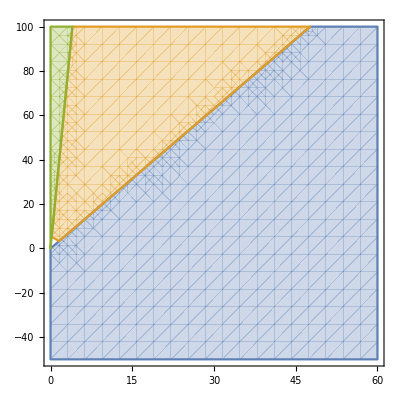

```mathematica
RegionPlot[{lambda<13.5 alpha-11.40175425099138 √(alpha^2),13.5 alpha-11.40175425099138 √(alpha^2)<lambda<13.5 alpha+11.40175425099138 √(alpha^2),lambda>13.5 alpha+11.40175425099138 √(alpha^2)},{alpha,0,60},{lambda,-50,100}]
```

```mathematica
λfullminus=λsols[[1]]/sf^4//Expand;
λfullplus=λsols[[3]]/sf^4//Expand;
```

```mathematica
λsols=Eigenvalues[Ksterms/.alpha->0/.kappa->0/.theta->0/.lambda->0]
```

{1,1,1/4,1/4}

```mathematica
Limit[λsols[[1]]/.theta->0/.kappa->alpha,sf->0]
```

1/4

```mathematica
Limit[λsols[[3]]/.theta->0/.kappa->alpha,sf->0]
```

1

```mathematica
----------------------------------------------------------------------------------------------------------------------------------------------
```

Gravitational wave constraints:

```mathematica
gamma=81alpha-kappa;
eta=61alpha+19kappa-16theta;
```

```mathematica
eqn1=gamma-eta==0/.theta->0;
eqn2=1+(eta sf^4)/4>0/.theta->0;
```

```mathematica
Reduce[eqn1&&eqn2,{alpha,kappa}]
```

alpha∈ℝ&&((sf<0&&alpha>-1/(20 sf^4))||sf==0||(sf>0&&alpha>-1/(20 sf^4)))&&kappa==alpha

```mathematica
eq2lim=eqn2/sf^4
```

```mathematica
eqn3=gamma-eta==0;
eqn4=1+eta sf/4>0;
```

```mathematica
Reduce[eqn3&&eqn4,{alpha,kappa,theta}]
```

(alpha|kappa)∈ℝ&&((sf<0&&kappa>(4+81 alpha sf)/sf)||sf==0||(sf>0&&kappa<(4+81 alpha sf)/sf))&&theta==1/4 (-5 alpha+5 kappa)

```mathematica
theta==1/4 (-5 alpha+5 kappa)//Expand//N
```

theta==-1.25 alpha+1.25 kappa

```mathematica
eqnGW=alpha∈Reals&&kappa<81 alpha&&theta==1/4 (-5 alpha+5 kappa);
```

```mathematica
Reduce[{(eqn1),(eqn2)},{alpha,kappa,theta}]
```

alpha∈ℝ&&kappa<81 alpha&&theta==1/4 (-5 alpha+5 kappa)

```mathematica
eqn3=61 alpha+19 kappa-√((61 alpha+19 kappa-16 theta)^2)-16 theta==0;
```

```mathematica
Reduce[{(eqn1),(eqn2),eqn3},{alpha,kappa,theta}]
```

alpha∈ℝ&&kappa<81 alpha&&theta==1/4 (-5 alpha+5 kappa)

```mathematica
----------------------------------------------------------------------------------------------------------------------------------------------
```

General model:

```mathematica
λminuslimit=Limit[λfullminus,sf->Infinity](*This is actually zero*)
```

λfullminus

```mathematica
λpluslimit=Limit[λfullplus,sf->Infinity]
```

1/16 (61 alpha+19 kappa+√((61 alpha+19 kappa-16 theta)^2)-16 theta)

```mathematica
Reduce[{λminuslimit≥0,λpluslimit≥0},{alpha,kappa,theta}]
```

(alpha|kappa)∈ℝ&&theta≤1/16 (61 alpha+19 kappa)

```mathematica
theta≤1/16 (61 alpha+19 kappa)//Expand//N
```

theta≤3.8125 alpha+1.1875 kappa

```mathematica
Reduce[{λminuslimit≥0,λpluslimit≥0,eqn1,eqn2},{alpha,kappa,theta}] (*Assuming alpha positive*)
```

alpha∈ℝ&&kappa<81 alpha&&theta==1/4 (-5 alpha+5 kappa)

```mathematica
Sign[λminuslimit*λpluslimit//Expand]
```

0

```mathematica
λp=η+Abs[η]
```

η+Abs[η]

```mathematica
Reduce[λp>0]
```

η>0

```mathematica
-----------------------------------------------------------------------------------------------------------------------------------------------
```

Non-infinity limit for phi: (Most general case)

```mathematica
MatrixForm[(Ksterms//Expand)/.theta->0/.kappa->alpha]
```

(1/4+10 alpha sf^4 | (7 alpha sf^3)/2-lambda sf^3 | 0 | 0
(7 alpha sf^3)/2-lambda sf^3 | 1-4 alpha sf^2+2 lambda sf^2 | 0 | 0
0 | 0 | 1/4+10 alpha sf^4 | (7 alpha sf^3)/2-lambda sf^3
0 | 0 | (7 alpha sf^3)/2-lambda sf^3 | 1-4 alpha sf^2+2 lambda sf^2)

```mathematica
λsols=FullSimplify[Eigenvalues[Ksterms/.theta->0/.kappa->alpha]];
```

```mathematica
λsols[[1]]
```

5/8+sf^2 (lambda+alpha (-2+5 sf^2))-1/8 √(9+16 sf^2 (alpha^2 sf^2 (16+129 sf^2+100 sf^4)-alpha (6+(15+16 lambda) sf^2+68 lambda sf^4)+lambda (3+4 lambda (sf^2+sf^4))))

```mathematica
λsols[[3]]//Expand
```

5/8-2 alpha sf^2+lambda sf^2+5 alpha sf^4+1/8 √(9+16 sf^2 (alpha^2 sf^2 (16+129 sf^2+100 sf^4)-alpha (6+(15+16 lambda) sf^2+68 lambda sf^4)+lambda (3+4 lambda (sf^2+sf^4))))

```mathematica
fλfullminus[alpha_,lambda_,sf_]:=5/8+sf^2 (lambda+alpha (-2+5 sf^2))-1/8 √(9+16 sf^2 (alpha^2 sf^2 (16+129 sf^2+100 sf^4)-alpha (6+(15+16 lambda) sf^2+68 lambda sf^4)+lambda (3+4 lambda (sf^2+sf^4))))
fλfullplus[alpha_,lambda_,sf_]:=1/8 (5-16 alpha sf^2+8 lambda sf^2+40 alpha sf^4+√((-5+16 alpha sf^2-8 lambda sf^2-40 alpha sf^4)^2-4 (4-16 alpha sf^2+8 lambda sf^2+160 alpha sf^4-836 alpha^2 sf^6+432 alpha lambda sf^6-16 lambda^2 sf^6)))
```

```mathematica
Manipulate[Plot3D[{fλfullminus[alpha,lambda,sf],0},{alpha,0,0.01},{lambda,0,2 0.05},PlotRange->Automatic,ImageSize->Large],{sf,10^2,10^8}](*-10^5,10^5*)
```

```mathematica
condλ1=Limit[λsols[[1]]/sf^4,sf->Infinity]
```

5 alpha-5 √(alpha^2)

```mathematica
condλ2=Limit[λsols[[3]]/sf^4,sf->Infinity]
```

5 (alpha+√(alpha^2))

```mathematica
Reduce[condλ1≥0&&condλ2≥0]
```

alpha≥0

```mathematica
λalpha1=λsols[[1]]/.lambda->b alpha//Simplify
```

5/8+alpha sf^2 (-2+b+5 sf^2)-1/8 √(9-48 alpha sf^2 (2-b+5 sf^2)+16 alpha^2 sf^4 (16+129 sf^2+100 sf^4+4 b^2 (1+sf^2)-4 b (4+17 sf^2)))

```mathematica
Reduce[λalpha1>0&&alpha>0,alpha]//N
```

sf∈ℝ&&((b<2.09825&&((sf<0.&&0.<alpha<(-2.+b+20. sf^2)/((209.-108. b+4. b^2) sf^4)+√((4.-4. b+b^2+129. sf^2-68. b sf^2+4. b^2 sf^2+400. sf^4)/((209.-108. b+4. b^2)^2 sf^8)))||(sf==0.&&alpha>0.)||(sf>0.&&0.<alpha<(-2.+b+20. sf^2)/((209.-108. b+4. b^2) sf^4)+√((4.-4. b+b^2+129. sf^2-68. b sf^2+4. b^2 sf^2+400. sf^4)/((209.-108. b+4. b^2)^2 sf^8)))))||(2.09825≤b≤24.9018&&alpha>0.)||(b>24.9018&&((sf<0.&&0.<alpha<(-2.+b+20. sf^2)/((209.-108. b+4. b^2) sf^4)+√((4.-4. b+b^2+129. sf^2-68. b sf^2+4. b^2 sf^2+400. sf^4)/((209.-108. b+4. b^2)^2 sf^8)))||(sf==0.&&alpha>0.)||(sf>0.&&0.<alpha<(-2.+b+20. sf^2)/((209.-108. b+4. b^2) sf^4)+√((4.-4. b+b^2+129. sf^2-68. b sf^2+4. b^2 sf^2+400. sf^4)/((209.-108. b+4. b^2)^2 sf^8))))))

```mathematica
λalpha2=λsols[[3]]/.lambda->b alpha//Simplify
```

1/8 (5+8 alpha sf^2 (-2+b+5 sf^2)+√(9-48 alpha sf^2 (2-b+5 sf^2)+16 alpha^2 sf^4 (16+129 sf^2+100 sf^4+4 b^2 (1+sf^2)-4 b (4+17 sf^2))))

```mathematica
Reduce[λalpha2>0&&alpha>0,alpha]//N
```

(b|sf)∈ℝ&&alpha>0.

```mathematica
λsols[[1]]/.lambda->2alpha//Simplify
```

5/8+5 alpha sf^4-1/8 √(9-240 alpha sf^4+16 alpha^2 sf^6 (9+100 sf^2))

```mathematica
Reduce[5/8+5 alpha sf^4-1/8 √(9-240 alpha sf^4+16 alpha^2 sf^6 (9+100 sf^2))≥0&&alpha>0]
```

(sf<0&&0<alpha≤20/(9 sf^2)+1/9 √((9+400 sf^2)/sf^6))||(sf==0&&alpha>0)||(sf>0&&0<alpha≤20/(9 sf^2)+1/9 √((9+400 sf^2)/sf^6))

```mathematica
Reduce[5/8+5beta-1/8 Sqrt[9-240 beta+16beta^2]>0,beta]//N (*case when lambda=2 alpha*)
```

-0.0267742<beta≤0.0375942||beta≥14.9624

```mathematica
Reduce[{fλfullminus[alpha,lambda,10^8]>0,alpha>0},{alpha,lambda},WorkingPrecision->100]//N
```

alpha>0.&&2.5×10^-33 (1.+5.4×10^33 alpha)-9.01388×10^-33 √(3.07692×10^15+1.23077×10^49 alpha+1.6×10^66 alpha^2)<lambda<2.5×10^-33 (1.+5.4×10^33 alpha)+9.01388×10^-33 √(3.07692×10^15+1.23077×10^49 alpha+1.6×10^66 alpha^2)

```mathematica
2.4999999999999998*^-33 (1.+5.4*^33 alpha)-9.013878188659972*^-33 √(3.076923076923077*^15+1.230769230769231*^49 alpha+1.6*^66 alpha^2)<lambda<2.4999999999999998*^-33 (1.+5.4*^33 alpha)+9.013878188659972*^-33 √(3.076923076923077*^15+1.230769230769231*^49 alpha+1.6*^66 alpha^2)/.alpha->1
```

2.09825<lambda<24.9018

```mathematica
eqnphi[sf_]:=Solve[fλfullminus[alpha,lambda,sf]==0,{alpha,lambda}]//N (*gives relation between alpha and lambda*)
```

```mathematica
eqnphi[10^8]
```

{{lambda→2.5×10^-33 (1.+5.4×10^33 alpha-3.60555 √(3.07692×10^15+1.23077×10^49 alpha+1.6×10^66 alpha^2))},{lambda→2.5×10^-33 (1.+5.4×10^33 alpha+3.60555 √(3.07692×10^15+1.23077×10^49 alpha+1.6×10^66 alpha^2))}}

```mathematica
eqnphi[1][[1,1,2]]
```

0.25 (1.+54. alpha-1. √(5.+252. alpha+2080. alpha^2))

```mathematica
eqnphi[1][[2,1,2]]
```

0.25 (1.+54. alpha+√(5.+252. alpha+2080. alpha^2))

```mathematica
(eqnphi[1][[1,1,2]])/(eqnphi[10][[1,1,2]])/.alpha->0.001
(eqnphi[10][[1,1,2]])/(eqnphi[10^2][[1,1,2]])/.alpha->0.001
(eqnphi[10^2][[1,1,2]])/(eqnphi[10^3][[1,1,2]])/.alpha->0.001
(eqnphi[10^5][[1,1,2]])/(eqnphi[10^6][[1,1,2]])/.alpha->0.001
```

185.584

-0.81186

0.979345

1.

```mathematica
(eqnphi[1][[2,1,2]])/(eqnphi[10][[2,1,2]])/.alpha->0.001
(eqnphi[10][[2,1,2]])/(eqnphi[10^2][[2,1,2]])/.alpha->0.001
(eqnphi[10^2][[2,1,2]])/(eqnphi[10^3][[2,1,2]])/.alpha->0.001
(eqnphi[10^5][[2,1,2]])/(eqnphi[10^6][[2,1,2]])/.alpha->0.001
```

29.1297

1.15123

1.00174

1.

```mathematica
(*when alpha is very small, phi should be larger than 10^4 to take a GOOD APPROXIMATION*)
```

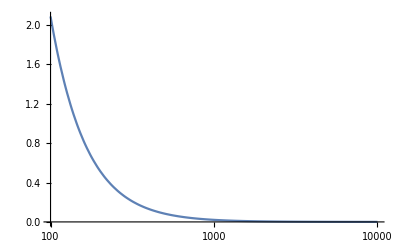

```mathematica
LogLinearPlot[(Abs[(eqnphi[sf][[1,1,2]]-eqnphi[10^6][[1,1,2]])/(eqnphi[10^6][[1,1,2]])/.alpha->0.001]*100),{sf,10^2,10^4},PlotRange->All](*shows that relation between alpha and lambda does not change to much varing phi*)
```

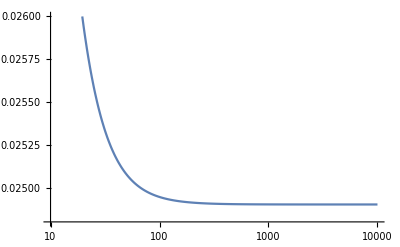

```mathematica
LogLinearPlot[eqnphi[sf][[2,1,2]]/.alpha->0.001,{sf,10^1,10^4},PlotRange->{0.0248,0.026}]
```

```mathematica
flambda1[alpha_]:=2.5*^-9 (1.+5.4*^9 alpha-3.605551275463989 √(3077.+1.23084*^13 alpha+1.6*^18 alpha^2))(*less tnat 2% of error, for phi order two*)
```

```mathematica
flambda2[alpha_]:=2.5*^-9 (1.+5.4*^9 alpha+3.605551275463989 √(3077.+1.23084*^13 alpha+1.6*^18 alpha^2))
```

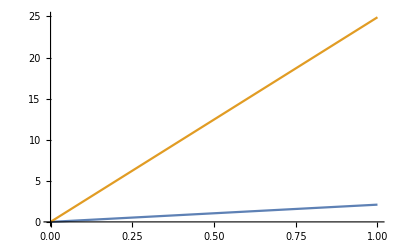

```mathematica
Plot[{flambda1[alpha],flambda2[alpha]},{alpha,0,1},PlotRange->{0,25}](*less tnat 2% of error*)
```

```mathematica
eqnphi[10^8][[1,1,2]]
```

2.5×10^-33 (1.+5.4×10^33 alpha-3.60555 √(3.07692×10^15+1.23077×10^49 alpha+1.6×10^66 alpha^2))

```mathematica
fλlarge1[alpha_]:=2.4999999999999998*^-33 (1.+5.4*^33 alpha-3.605551275463989 √(3.076923076923077*^15+1.230769230769231*^49 alpha+1.6*^66 alpha^2))
```

```mathematica
eqnphi[10^8][[2,1,2]]
```

2.5×10^-33 (1.+5.4×10^33 alpha+3.60555 √(3.07692×10^15+1.23077×10^49 alpha+1.6×10^66 alpha^2))

```mathematica
fλlarge2[alpha_]:=2.4999999999999998*^-33 (1.+5.4*^33 alpha+3.605551275463989 √(3.076923076923077*^15+1.230769230769231*^49 alpha+1.6*^66 alpha^2))
```

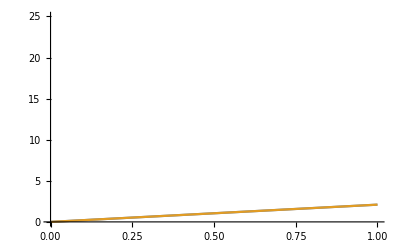

```mathematica
Plot[{flambda1[alpha],fλlarge1[alpha]},{alpha,0,1},PlotRange->{0,25}](*less tnat 2% of error*)
```

```mathematica
fλlarge1[1]
```

2.09825

```mathematica
fλlarge2[1]
```

24.9018

```mathematica
fλfullminus[2,4,10^8]//N (*lambda must be 2.1 times alpha and phi of any order to get the eigenvalue positive but not zero (not exactly for alpha=5,6). When lambda is sliglhy smaller than 2.1 times alpha, and phi less than 10^7, the eigenvalue may be negative. Increasing phi the egenvalue becomes postive*)
```

0.

```mathematica
a=1.9(*2.1<a<24.6*);
Grid[Table[{alpha,10^i,fλfullminus[alpha,a alpha,4 10^i]},{alpha,0,0.001,0.001},{i,1,8}]]//N
```

{0.,10.,0.25} | {0.,100.,0.25} | {0.,1000.,0.25} | {0.,10000.,0.25} | {0.,100000.,0.25} | {0.,1.×10^6,0.25} | {0.,1.×10^7,0.25} | {0.,1.×10^8,0.25}
{0.001,10.,0.2704} | {0.001,100.,-71.96} | {0.001,1000.,-7295.} | {0.001,10000.,-729600.} | {0.001,100000.,-7.2958×10^7} | {0.001,1.×10^6,-6.97932×10^9} | {0.001,1.×10^7,0.} | {0.001,1.×10^8,0.}

```mathematica
fλfullminus[5,11,4 10^7]//N (*lambda must be larger than 2.1 times alpha and phi of the order 10^7 in order to get zero*)
```

0.

```mathematica
Manipulate[Plot3D[fλfullplus[alpha,lambda,sf],{alpha,0,10},{lambda,0,20}],{sf,10^2,10^10}]
```

```mathematica
Limit[λsols[[1]],sf->Infinity]
```

DirectedInfinity[5 alpha-5 √(alpha^2)]

```mathematica
Limit[λsols[[3]],sf->Infinity]
```

DirectedInfinity[alpha+√(alpha^2)]

```mathematica
λglobal=(-k12 k21+k11 k22)/.kappa->alpha/.theta->0//Expand(*product of two eigenvalues*)
```

1/4-alpha sf^2+(lambda sf^2)/2+10 alpha sf^4-(209 alpha^2 sf^6)/4+27 alpha lambda sf^6-lambda^2 sf^6

```mathematica
1/4-alpha sf^2+(lambda sf^2)/2+10 alpha sf^4-(209 alpha^2 sf^6)/4+27 alpha lambda sf^6-lambda^2 sf^6/.lambda->2alpha
```

1/4+10 alpha sf^4-(9 alpha^2 sf^6)/4

```mathematica
Reduce[1/4+10 alpha sf^4-(9 alpha^2 sf^6)/4>0,{sf,alpha}]
```

alpha∈ℝ&&((sf<0&&20/(9 sf^2)-1/9 √((9+400 sf^2)/sf^6)<alpha<20/(9 sf^2)+1/9 √((9+400 sf^2)/sf^6))||sf==0||(sf>0&&20/(9 sf^2)-1/9 √((9+400 sf^2)/sf^6)<alpha<20/(9 sf^2)+1/9 √((9+400 sf^2)/sf^6)))

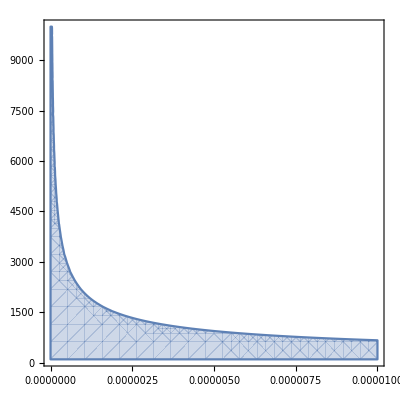

```mathematica
RegionPlot[1/4+10 alpha sf^4-(9 alpha^2 sf^6)/4>0,{alpha,0,0.00001},{sf,10^2,10^4}]
```

```mathematica
fλglobal[alpha_,lambda_,sf_]:=1/4-alpha sf^2+(lambda sf^2)/2+10 alpha sf^4-(209 alpha^2 sf^6)/4+27 alpha lambda sf^6-lambda^2 sf^6
```

```mathematica
fλglobal[0.001,2.1*0.001,10^8]
```

4.×10^40

```mathematica
RegionPlot3D[λglobal>0,{alpha,0,1},{lambda,0,3},{sf,10^2,10^6}]
```

-Graphics3D-

```mathematica
fλglobal2[alpha_,lambda_]:=1/4-alpha sf^2+(lambda sf^2)/2+10 alpha sf^4-(209 alpha^2 sf^6)/4+27 alpha lambda sf^6-lambda^2 sf^6/.sf->10^6
```

```mathematica
Plot3D[{fλglobal2[alpha,lambda],0},{alpha,0,1},{lambda,0,3}]
```

-Graphics3D-

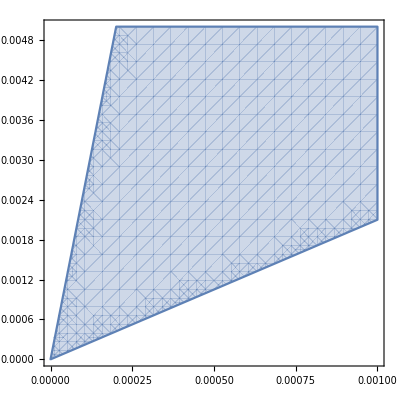

```mathematica
RegionPlot[{fλglobal[alpha,lambda,10^8]>0},{alpha,0,0.001},{lambda,0,0.005}]
```

```mathematica
RegionPlot[27alpha lambda-209/4 alpha^2-lambda^2>0,{alpha,0,0.001},{lambda,0,0.005}](*analytical approximation*)
```

-Graphics-

```mathematica
Reduce[-209/4alpha^2-lambda^2+27alpha lambda>0&&alpha>0,{alpha,lambda}]
```

alpha>0&&(27 alpha)/2-√130 √(alpha^2)<lambda<(27 alpha)/2+√130 √(alpha^2)

```mathematica
(27 alpha)/2-√130 √(alpha^2)<lambda<(27 alpha)/2+√130 √(alpha^2)/.alpha->1//N
```

2.09825<lambda<24.9018

```mathematica
Limit[λglobal/sf^6,sf->Infinity]
```

-(209 alpha^2)/4+27 alpha lambda-lambda^2

```mathematica
-(209 alpha^2)/4+27 alpha lambda-lambda^2/.lambda->2.099alpha//N
```

0.017199 alpha^2

```mathematica
----------------------------------------------------------------------------------------------------------------------------------------------
```

Case I:  theta->0  and lambda->0 (L_41and L_42 with the possibility to add L_43, but it does not affect this result, however in the Cs  does)

```mathematica
Condλ1=Limit[(λfullminus)/.lambda->0/.theta->0,sf->Infinity](*This is actually zero*)
```

1/16 (61 alpha+19 kappa-√((61 alpha+19 kappa)^2))

```mathematica
Condλ2=Limit[(λfullplus)/.lambda->0/.theta->0,sf->Infinity]
```

1/16 (61 alpha+19 kappa+√((61 alpha+19 kappa)^2))

```mathematica
Reduce[{Condλ1≥0,Condλ2≥0},{alpha,kappa}]
```

alpha∈ℝ&&kappa≥-(61 alpha)/19

```mathematica
Reduce[{Condλ1≥0,Condλ2≥0,(eqn1/.lambda->0/.theta->0),(eqn2/.lambda->0/.theta->0)},{alpha,kappa}] (*Assuming alpha positive*)
```

alpha>0&&kappa==alpha

Case II:  theta->0 (independent of lambda) so, results are similar to the case I.

```mathematica
condλ1case2=Limit[(λfullminus)/.theta->0,sf->Infinity](*This is actually zero*)
```

1/16 (61 alpha+19 kappa-√((61 alpha+19 kappa)^2))

```mathematica
condλ2case2=Limit[(λfullplus)/.theta->0,sf->Infinity]
```

1/16 (61 alpha+19 kappa+√((61 alpha+19 kappa)^2))

```mathematica
Reduce[{condλ1case2≥0,condλ2case2≥0},{alpha,kappa}]
```

alpha∈ℝ&&kappa≥-(61 alpha)/19

```mathematica
Reduce[{condλ1case2≥0,condλ2case2≥0,(eqn1/.theta->0),(eqn2/.theta->0)},{alpha,kappa}]
```

alpha>0&&kappa==alpha

Case III:  lambda->0 (leaving freely gamma) (reproduce the general case)

```mathematica
λcase3min=Limit[(λfullminus)/.lambda->0,sf->Infinity](*This is actually zero*)
```

1/16 (61 alpha+19 kappa-√((61 alpha+19 kappa-16 theta)^2)-16 theta)

```mathematica
λcase3pl=Limit[(λfullplus)/.lambda->0,sf->Infinity]
```

1/16 (61 alpha+19 kappa+√((61 alpha+19 kappa-16 theta)^2)-16 theta)

```mathematica
Reduce[{λcase3min≥0,λcase3pl≥0},{alpha, kappa,theta}]
```

(alpha|kappa)∈ℝ&&theta≤1/16 (61 alpha+19 kappa)

```mathematica
Reduce[{λcase3min≥0,λcase3pl≥0,eqn1,eqn2},{alpha,kappa,theta}] (*Assuming alpha positive*)
```

alpha∈ℝ&&kappa<81 alpha&&theta==1/4 (-5 alpha+5 kappa)

```mathematica
-------------------------------------------------------------------------------------------------------------------------------------------------
```

There are not contributions from the gamma term to these elements (L matrix) but this is present in the K matrix.

```mathematica
L11=1/4;
L33=1/4;
L22=1+(-5alpha+kappa+2lambda) sf^2;
L44=1+(-5alpha+kappa+2lambda) sf^2;
L12=1/2(10 alpha+kappa-4lambda)sf^3 ;
L21=1/2(10 alpha+kappa-4lambda) sf^3 ;
L34=1/2(10 alpha+kappa-4lambda) sf^3 ;
L43=1/2(10 alpha+kappa-4lambda) sf^3 ;
```

```mathematica
MatrixForm[Lsterms={{L11,L12,0,0},{L21,L22,0,0},{0,0,L33,L34},{0,0,L43,L44}}]
```

(1/4 | 1/2 (10 alpha+kappa-4 lambda) sf^3 | 0 | 0
1/2 (10 alpha+kappa-4 lambda) sf^3 | 1+(-5 alpha+kappa+2 lambda) sf^2 | 0 | 0
0 | 0 | 1/4 | 1/2 (10 alpha+kappa-4 lambda) sf^3
0 | 0 | 1/2 (10 alpha+kappa-4 lambda) sf^3 | 1+(-5 alpha+kappa+2 lambda) sf^2)

```mathematica
CsSols=Solve[Det[c Ksterms-Lsterms]==0,c];(*it provides 4 solution sets with just one element in the nested list*)
```

```mathematica
Cs1full=c/.CsSols[[1,1]];Cs2full=c/.CsSols[[3,1]];
```

```mathematica
Cs1fulllimit=Limit[Cs1full,sf->Infinity]//Simplify
```

(705 alpha^2-46 alpha kappa-31 kappa^2-362 alpha lambda+2 kappa lambda+32 lambda^2+240 alpha theta+48 kappa theta-96 lambda theta-√(5 alpha-kappa-2 lambda) √((61 alpha+19 kappa-16 theta) (305 alpha^2-51 kappa^2-32 lambda (2 lambda+7 theta)+2 kappa (53 lambda+40 theta)+alpha (-286 kappa+38 lambda+560 theta))))/(2 (505 alpha^2-kappa^2-2 kappa (7 lambda+40 theta)+alpha (-86 kappa-202 lambda+240 theta)+8 (lambda^2-4 lambda theta+16 theta^2)))

```mathematica
Cs2fulllimit=Limit[Cs2full,sf->Infinity]//Simplify
```

(705 alpha^2-46 alpha kappa-31 kappa^2-362 alpha lambda+2 kappa lambda+32 lambda^2+240 alpha theta+48 kappa theta-96 lambda theta+√(5 alpha-kappa-2 lambda) √((61 alpha+19 kappa-16 theta) (305 alpha^2-51 kappa^2-32 lambda (2 lambda+7 theta)+2 kappa (53 lambda+40 theta)+alpha (-286 kappa+38 lambda+560 theta))))/(2 (505 alpha^2-kappa^2-2 kappa (7 lambda+40 theta)+alpha (-86 kappa-202 lambda+240 theta)+8 (lambda^2-4 lambda theta+16 theta^2)))

```mathematica
-----------------------------------------------------------------------------------------------------------------------------------------------
```

Non-infinity limit for phi: (Most general case)

```mathematica
Lsterms/.theta->0/.kappa->alpha//MatrixForm
```

(1/4 | 1/2 (11 alpha-4 lambda) sf^3 | 0 | 0
1/2 (11 alpha-4 lambda) sf^3 | 1+(-4 alpha+2 lambda) sf^2 | 0 | 0
0 | 0 | 1/4 | 1/2 (11 alpha-4 lambda) sf^3
0 | 0 | 1/2 (11 alpha-4 lambda) sf^3 | 1+(-4 alpha+2 lambda) sf^2)

```mathematica
Solve[{1/2(11 alpha-4 lambda)==0&&-4 alpha+2 lambda==0},{alpha,lambda}]
```

{{alpha→0,lambda→0}}

```mathematica
CsSols=Solve[Det[c (Ksterms/.theta->0/.kappa->alpha)-(Lsterms/.theta->0/.kappa->alpha)]==0,c];(*it provides 4 solution sets with just one element in the nested list*)
Cs1full=c/.CsSols[[1,1]]
```

(-1+4 alpha sf^2-2 lambda sf^2-20 alpha sf^4+157 alpha^2 sf^6-90 alpha lambda sf^6+8 lambda^2 sf^6-2 √(4 alpha^2 sf^6-4 alpha lambda sf^6+lambda^2 sf^6+100 alpha^2 sf^8-16 alpha^3 sf^8+24 alpha^2 lambda sf^8-12 alpha lambda^2 sf^8+2 lambda^3 sf^8-360 alpha^3 sf^10+20 alpha^2 lambda sf^10+80 alpha lambda^2 sf^10-160 alpha^4 sf^12+800 alpha^3 lambda sf^12-680 alpha^2 lambda^2 sf^12+160 alpha lambda^3 sf^12))/(-1+4 alpha sf^2-2 lambda sf^2-40 alpha sf^4+209 alpha^2 sf^6-108 alpha lambda sf^6+4 lambda^2 sf^6)

```mathematica
Cs2full=c/.CsSols[[3,1]]
```

(-1+4 alpha sf^2-2 lambda sf^2-20 alpha sf^4+157 alpha^2 sf^6-90 alpha lambda sf^6+8 lambda^2 sf^6+2 √(4 alpha^2 sf^6-4 alpha lambda sf^6+lambda^2 sf^6+100 alpha^2 sf^8-16 alpha^3 sf^8+24 alpha^2 lambda sf^8-12 alpha lambda^2 sf^8+2 lambda^3 sf^8-360 alpha^3 sf^10+20 alpha^2 lambda sf^10+80 alpha lambda^2 sf^10-160 alpha^4 sf^12+800 alpha^3 lambda sf^12-680 alpha^2 lambda^2 sf^12+160 alpha lambda^3 sf^12))/(-1+4 alpha sf^2-2 lambda sf^2-40 alpha sf^4+209 alpha^2 sf^6-108 alpha lambda sf^6+4 lambda^2 sf^6)

```mathematica
fCs1full[alpha_,lambda_,sf_]:=(-1+4 alpha sf^2-2 lambda sf^2-20 alpha sf^4+157 alpha^2 sf^6-90 alpha lambda sf^6+8 lambda^2 sf^6-2 √(4 alpha^2 sf^6-4 alpha lambda sf^6+lambda^2 sf^6+100 alpha^2 sf^8-16 alpha^3 sf^8+24 alpha^2 lambda sf^8-12 alpha lambda^2 sf^8+2 lambda^3 sf^8-360 alpha^3 sf^10+20 alpha^2 lambda sf^10+80 alpha lambda^2 sf^10-160 alpha^4 sf^12+800 alpha^3 lambda sf^12-680 alpha^2 lambda^2 sf^12+160 alpha lambda^3 sf^12))/(-1+4 alpha sf^2-2 lambda sf^2-40 alpha sf^4+209 alpha^2 sf^6-108 alpha lambda sf^6+4 lambda^2 sf^6)
```

```mathematica
fCs2full[alpha_,lambda_,sf_]:=(-1+4 alpha sf^2-2 lambda sf^2-20 alpha sf^4+157 alpha^2 sf^6-90 alpha lambda sf^6+8 lambda^2 sf^6+2 √(4 alpha^2 sf^6-4 alpha lambda sf^6+lambda^2 sf^6+100 alpha^2 sf^8-16 alpha^3 sf^8+24 alpha^2 lambda sf^8-12 alpha lambda^2 sf^8+2 lambda^3 sf^8-360 alpha^3 sf^10+20 alpha^2 lambda sf^10+80 alpha lambda^2 sf^10-160 alpha^4 sf^12+800 alpha^3 lambda sf^12-680 alpha^2 lambda^2 sf^12+160 alpha lambda^3 sf^12))/(-1+4 alpha sf^2-2 lambda sf^2-40 alpha sf^4+209 alpha^2 sf^6-108 alpha lambda sf^6+4 lambda^2 sf^6)
```

```mathematica
Manipulate[Plot3D[{fCs1full[alpha,lambda,sf],1},{alpha,0,10},{lambda,0,20},PlotRange->Automatic,ImageSize->Large],{sf,10^2,10^10}]
```

```mathematica
Manipulate[Plot3D[{fCs2full[alpha,lambda,sf],1},{alpha,0,0.01},{lambda,0,0.05},PlotRange->Automatic,ImageSize->Large],{sf,10^2,10^10}]
```

```mathematica
fCs1full[0.001,2 0.001,10^7]
```

1.

```mathematica
fCs2full[0.01,2 0.01,10^2]
```

1.04651

```mathematica
b=2.098245749008621;
Grid[Table[{alpha,10^i,fCs1full[alpha,b alpha,10^i]},{alpha,0,0.01,0.001},{i,1,8}]]//N(*insensitive to phi*)
```

{0.,10.,1.} | {0.,100.,1.} | {0.,1000.,1.} | {0.,10000.,1.} | {0.,100000.,1.} | {0.,1.×10^6,1.} | {0.,1.×10^7,1.} | {0.,1.×10^8,1.}
{0.001,10.,1.00009} | {0.001,100.,1.00358} | {0.001,1000.,1.00568} | {0.001,10000.,1.00571} | {0.001,100000.,1.00571} | {0.001,1.×10^6,1.00572} | {0.001,1.×10^7,1.00617} | {0.001,1.×10^8,0.985541}
{0.002,10.,1.00019} | {0.002,100.,1.0044} | {0.002,1000.,1.0057} | {0.002,10000.,1.00571} | {0.002,100000.,1.00571} | {0.002,1.×10^6,1.00573} | {0.002,1.×10^7,1.00666} | {0.002,1.×10^8,0.964315}
{0.003,10.,1.00028} | {0.003,100.,1.00477} | {0.003,1000.,1.0057} | {0.003,10000.,1.00571} | {0.003,100000.,1.00571} | {0.003,1.×10^6,1.0057} | {0.003,1.×10^7,1.00482} | {0.003,1.×10^8,0.869044}
{0.004,10.,1.00036} | {0.004,100.,1.00497} | {0.004,1000.,1.0057} | {0.004,10000.,1.00571} | {0.004,100000.,1.00571} | {0.004,1.×10^6,1.00576} | {0.004,1.×10^7,1.00755} | {0.004,1.×10^8,0.926369}
{0.005,10.,1.00044} | {0.005,100.,1.00511} | {0.005,1000.,1.00571} | {0.005,10000.,1.00571} | {0.005,100000.,1.00571} | {0.005,1.×10^6,1.00572} | {0.005,1.×10^7,1.00231} | {0.005,1.×10^8,0.702973}
{0.006,10.,1.00053} | {0.006,100.,1.0052} | {0.006,1000.,1.00571} | {0.006,10000.,1.00571} | {0.006,100000.,1.00571} | {0.006,1.×10^6,1.0057} | {0.006,1.×10^7,1.00397} | {0.006,1.×10^8,0.750057}
{0.007,10.,1.0006} | {0.007,100.,1.00527} | {0.007,1000.,1.00571} | {0.007,10000.,1.00571} | {0.007,100000.,1.00571} | {0.007,1.×10^6,1.00574} | {0.007,1.×10^7,1.00537} | {0.007,1.×10^8,1.14681}
{0.008,10.,1.00068} | {0.008,100.,1.00532} | {0.008,1000.,1.00571} | {0.008,10000.,1.00571} | {0.008,100000.,1.00571} | {0.008,1.×10^6,1.0058} | {0.008,1.×10^7,1.00953} | {0.008,1.×10^8,0.840593}
{0.009,10.,1.00075} | {0.009,100.,1.00536} | {0.009,1000.,1.00571} | {0.009,10000.,1.00571} | {0.009,100000.,1.00571} | {0.009,1.×10^6,1.00574} | {0.009,1.×10^7,1.00589} | {0.009,1.×10^8,1.08779}
{0.01,10.,1.00083} | {0.01,100.,1.00539} | {0.01,1000.,1.00571} | {0.01,10000.,1.00571} | {0.01,100000.,1.00571} | {0.01,1.×10^6,1.00572} | {0.01,1.×10^7,0.999136} | {0.01,1.×10^8,0.455848}

```mathematica
Cs1fullb=Cs1full/.lambda->b alpha//Simplify
```

(-1+alpha^2 (157-90 b+8 b^2) sf^6-2 alpha sf^2 (-2+b+10 sf^2)-2 √(alpha^2 sf^6 (2 alpha b^3 sf^2 (1+80 alpha sf^4)-4 (-1+(-25+4 alpha) sf^2+90 alpha sf^4+40 alpha^2 sf^6)+4 b (-1+200 alpha^2 sf^6+alpha sf^2 (6+5 sf^2))+b^2 (1-680 alpha^2 sf^6+4 alpha sf^2 (-3+20 sf^2)))))/(-1+alpha^2 (209-108 b+4 b^2) sf^6-2 alpha sf^2 (-2+b+20 sf^2))

```mathematica
Cs2fullb=Cs2full/.lambda->b alpha//Simplify
```

(-1+alpha^2 (157-90 b+8 b^2) sf^6-2 alpha sf^2 (-2+b+10 sf^2)+2 √(alpha^2 sf^6 (2 alpha b^3 sf^2 (1+80 alpha sf^4)-4 (-1+(-25+4 alpha) sf^2+90 alpha sf^4+40 alpha^2 sf^6)+4 b (-1+200 alpha^2 sf^6+alpha sf^2 (6+5 sf^2))+b^2 (1-680 alpha^2 sf^6+4 alpha sf^2 (-3+20 sf^2)))))/(-1+alpha^2 (209-108 b+4 b^2) sf^6-2 alpha sf^2 (-2+b+20 sf^2))

```mathematica
Reduce[0<Cs1fullb≤1&&0<Cs2fullb≤1&&alpha>0]
```

b∈ℝ&&((sf<0&&((1/4<b<2&&alpha≥(-4+4 b-b^2-100 sf^2)/(40 sf^4-180 b sf^4+80 b^2 sf^4))||(0<alpha<(√(1/sf^6))/3&&b==2)))||(alpha>0&&sf==0)||(sf>0&&((1/4<b<2&&alpha≥(-4+4 b-b^2-100 sf^2)/(40 sf^4-180 b sf^4+80 b^2 sf^4))||(0<alpha<(√(1/sf^6))/3&&b==2))))

```mathematica
Reduce[0<Cs1fullb≤1&&0<Cs2fullb≤1&& λalpha1>0&&alpha>0](*general result*)
```

(b<2&&sf==0&&alpha>0)||(b==2&&((sf<0&&0<alpha<(√(1/sf^6))/3)||(sf==0&&alpha>0)||(sf>0&&0<alpha<(√(1/sf^6))/3)))||(b>2&&sf==0&&alpha>0)

```mathematica
Cs1limit=Limit[Cs1full,sf->Infinity]
```

(157 alpha^2-90 alpha lambda+8 lambda^2-4 √10 √(-alpha (alpha-4 lambda) (-2 alpha+lambda)^2))/(209 alpha^2-108 alpha lambda+4 lambda^2)

```mathematica
fCs1limit[alpha_,lambda_]:=(157 alpha^2-90 alpha lambda+8 lambda^2-4 √10 √(-alpha (alpha-4 lambda) (-2 alpha+lambda)^2))/(209 alpha^2-108 alpha lambda+4 lambda^2)
```

```mathematica
Cs2limit=Limit[Cs2full,sf->Infinity]
```

(157 alpha^2-90 alpha lambda+8 lambda^2+4 √10 √(-alpha (alpha-4 lambda) (-2 alpha+lambda)^2))/(209 alpha^2-108 alpha lambda+4 lambda^2)

```mathematica
fCs2limit[alpha_,lambda_]:=(157 alpha^2-90 alpha lambda+8 lambda^2+4 √10 √(-alpha (alpha-4 lambda) (-2 alpha+lambda)^2))/(209 alpha^2-108 alpha lambda+4 lambda^2)
```

```mathematica
Reduce[0<Cs1limit≤1&&0<Cs2limit≤1,{alpha,lambda}]
```

(alpha<0&&2 alpha≤lambda≤alpha/4)||(alpha>0&&alpha/4≤lambda≤2 alpha)

```mathematica
Plot3D[{Cs1limit,1},{alpha,0,0.01},{lambda,0,0.05},PlotRange->All,ImageSize->Large]
```

-Graphics3D-

```mathematica
Plot3D[{Cs2limit,1},{alpha,0,0.01},{lambda,0,0.05},PlotRange->{0.5,1.5},ImageSize->Large]
```

-Graphics3D-

```mathematica
Cs1alpha=Cs1limit/.lambda->b alpha//Simplify
```

(-4 √10 √(alpha^4 (-2+b)^2 (-1+4 b))+alpha^2 (157-90 b+8 b^2))/(alpha^2 (209-108 b+4 b^2))

```mathematica
Cs2alpha=Cs2limit/.lambda->b alpha//Simplify
```

(4 √10 √(alpha^4 (-2+b)^2 (-1+4 b))+alpha^2 (157-90 b+8 b^2))/(alpha^2 (209-108 b+4 b^2))

```mathematica
(157-90 b+8 b^2)/(209-108 b+4 b^2)/.b->2
```

1

```mathematica
Reduce[0<Cs1alpha≤1&&0<Cs2alpha≤1]
```

alpha∈ℝ&&alpha≠0&&1/4≤b≤2

```mathematica
Reduce[0<Cs1alpha≤1&&0<Cs2alpha≤1&&condλ1≥0&&condλ2≥0] (*asypmtotic result*)
```

alpha>0&&1/4≤b≤2

```mathematica
Solve[Cs1limit==1,{alpha,lambda}]
```

{{lambda→2 alpha}}

```mathematica
Solve[Cs1limit==0,{alpha,lambda}]
```

{{lambda→(11 alpha)/4}}

```mathematica
Solve[Cs2limit==1,{alpha,lambda}]
```

{{lambda→2 alpha}}

```mathematica
Solve[Cs2limit==0,{alpha,lambda}]
```

{{lambda→(11 alpha)/4}}

```mathematica
Reduce[{0<Cs1limit≤1.1,0<Cs1limit≤1.1,27alpha lambda-209/4 alpha^2-lambda^2>0},{alpha,lambda}]
```

(alpha<0&&3.19136 alpha-1.17964 √(alpha^2)≤lambda<13.5 alpha+11.4018 √(alpha^2))||(alpha>0&&13.5 alpha-11.4018 √(alpha^2)<lambda≤3.19136 alpha+1.17964 √(alpha^2))

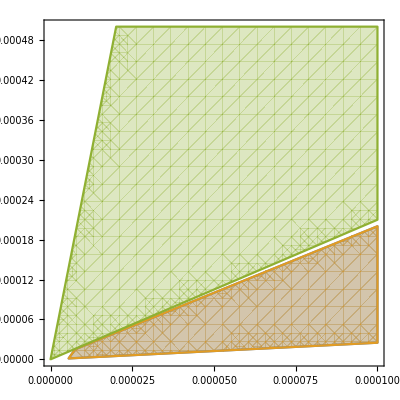

```mathematica
RegionPlot[{0<Cs1limit≤1,0<Cs1limit≤1,27alpha lambda-209/4 alpha^2-lambda^2>0},{alpha,0,0.0001},{lambda,0,0.0005}]
```

```mathematica
(-1+4 alpha sf^2-2 lambda sf^2-20 alpha sf^4+157 alpha^2 sf^6-90 alpha lambda sf^6+8 lambda^2 sf^6+2 √(4 alpha^2 sf^6-4 alpha lambda sf^6+lambda^2 sf^6+100 alpha^2 sf^8-16 alpha^3 sf^8+24 alpha^2 lambda sf^8-12 alpha lambda^2 sf^8+2 lambda^3 sf^8-360 alpha^3 sf^10+20 alpha^2 lambda sf^10+80 alpha lambda^2 sf^10-160 alpha^4 sf^12+800 alpha^3 lambda sf^12-680 alpha^2 lambda^2 sf^12+160 alpha lambda^3 sf^12))/(-1+4 alpha sf^2-2 lambda sf^2-40 alpha sf^4+209 alpha^2 sf^6-108 alpha lambda sf^6+4 lambda^2 sf^6)/.lambda->2 alpha
```

```mathematica
(-1-20 alpha sf^4+9 alpha^2 sf^6-20 √(alpha^2 sf^8))/(-1-40 alpha sf^4+9 alpha^2 sf^6)/.alpha->0.00001 /.sf-> 10^4//N
```

1.

```mathematica
Reduce[0<(-1-20 alpha sf^4+9 alpha^2 sf^6-20 √(alpha^2 sf^8))/(-1-40 alpha sf^4+9 alpha^2 sf^6)≤1,{sf,alpha}]/.sf-> 10//N
```

alpha∈ℝ&&(alpha<-0.000333333||0.≤alpha<0.0444469||alpha>0.0444469)

```mathematica
Reduce[0<(-1-20 alpha sf^4+9 alpha^2 sf^6+20 √(alpha^2 sf^8))/(-1-40 alpha sf^4+9 alpha^2 sf^6)≤1,{sf,alpha}]
```

alpha∈ℝ&&((sf<0&&(alpha<20/(9 sf^2)-1/9 √((9+400 sf^2)/sf^6)||20/(9 sf^2)-1/9 √((9+400 sf^2)/sf^6)<alpha<(√(1/sf^6))/3))||sf==0||(sf>0&&(alpha<20/(9 sf^2)-1/9 √((9+400 sf^2)/sf^6)||20/(9 sf^2)-1/9 √((9+400 sf^2)/sf^6)<alpha<(√(1/sf^6))/3)))

```mathematica
Reduce[0<(-1-20 alpha sf^4+9 alpha^2 sf^6+20 √(alpha^2 sf^8))/(-1-40 alpha sf^4+9 alpha^2 sf^6)≤1&&0<(-1-20 alpha sf^4+9 alpha^2 sf^6-20 √(alpha^2 sf^8))/(-1-40 alpha sf^4+9 alpha^2 sf^6)≤1&&alpha>0,{sf,alpha}]
```

(sf<0&&0<alpha<(√(1/sf^6))/3)||(sf==0&&alpha>0)||(sf>0&&0<alpha<(√(1/sf^6))/3)

```mathematica
Cs1red=Cs1full/.lambda-> b alpha//Simplify
```

(-1+alpha^2 (157-90 b+8 b^2) sf^6-2 alpha sf^2 (-2+b+10 sf^2)-2 √(alpha^2 sf^6 (2 alpha b^3 sf^2 (1+80 alpha sf^4)-4 (-1+(-25+4 alpha) sf^2+90 alpha sf^4+40 alpha^2 sf^6)+4 b (-1+200 alpha^2 sf^6+alpha sf^2 (6+5 sf^2))+b^2 (1-680 alpha^2 sf^6+4 alpha sf^2 (-3+20 sf^2)))))/(-1+alpha^2 (209-108 b+4 b^2) sf^6-2 alpha sf^2 (-2+b+20 sf^2))

```mathematica
Cs2red=Cs2full/.lambda-> b alpha//Simplify
```

(-1+alpha^2 (157-90 b+8 b^2) sf^6-2 alpha sf^2 (-2+b+10 sf^2)+2 √(alpha^2 sf^6 (2 alpha b^3 sf^2 (1+80 alpha sf^4)-4 (-1+(-25+4 alpha) sf^2+90 alpha sf^4+40 alpha^2 sf^6)+4 b (-1+200 alpha^2 sf^6+alpha sf^2 (6+5 sf^2))+b^2 (1-680 alpha^2 sf^6+4 alpha sf^2 (-3+20 sf^2)))))/(-1+alpha^2 (209-108 b+4 b^2) sf^6-2 alpha sf^2 (-2+b+20 sf^2))

```mathematica
Reduce[0<Cs1red≤1&&0<Cs2red≤1&&alpha>0]
```

b∈ℝ&&((sf<0&&((1/4<b<2&&alpha≥(-4+4 b-b^2-100 sf^2)/(40 sf^4-180 b sf^4+80 b^2 sf^4))||(0<alpha<(√(1/sf^6))/3&&b==2)))||(alpha>0&&sf==0)||(sf>0&&((1/4<b<2&&alpha≥(-4+4 b-b^2-100 sf^2)/(40 sf^4-180 b sf^4+80 b^2 sf^4))||(0<alpha<(√(1/sf^6))/3&&b==2))))

```mathematica
Cs1redb=Cs1red/.b->2//Simplify
```

(1+20 alpha sf^4-9 alpha^2 sf^6+20 √(alpha^2 sf^8))/(1+40 alpha sf^4-9 alpha^2 sf^6)

```mathematica
Cs2redb=Cs2red/.b->2//Simplify
```

(1+20 alpha sf^4-9 alpha^2 sf^6-20 √(alpha^2 sf^8))/(1+40 alpha sf^4-9 alpha^2 sf^6)

```mathematica
Reduce[0<Cs1redb≤1&&0<Cs2redb≤1&&alpha>0]
```

(sf<0&&0<alpha<(√(1/sf^6))/3)||(sf==0&&alpha>0)||(sf>0&&0<alpha<(√(1/sf^6))/3)

```mathematica
fCs1full[0.01,2*0.01,10]
```

1.

```mathematica
fCs1limit
```

```mathematica
---------------------------------------------------------------------------------------
```

Reproducing GR:

```mathematica
CGR=Solve[Det[c (Ksterms/.alpha->0/.lambda->0/.theta->0/.kappa->0)-(Lsterms/.alpha->0/.lambda->0/.theta->0/.kappa->0)]==0,c]
```

{{c→1},{c→1},{c→1},{c→1}}

```mathematica
---------------------------------------------------------------------------------------
```

Case I:  theta->0  and lambda->0 (L_41and L_42 model)

```mathematica
Clear[c];
```

```mathematica
Cs1sols=Solve[Det[c (Ksterms/.lambda->0/.theta->0)-(Lsterms/.lambda->0/.theta->0)]==0,c];
```

```mathematica
Cs1sols[[4,1]]
```

c→(-4+20 alpha sf^2-4 kappa sf^2-61 alpha sf^4-19 kappa sf^4+705 alpha^2 sf^6-46 alpha kappa sf^6-31 kappa^2 sf^6+√(256 kappa^2 sf^6+3721 alpha^2 sf^8+2318 alpha kappa sf^8+361 kappa^2 sf^8-1280 alpha kappa^2 sf^8+256 kappa^3 sf^8-37210 alpha^3 sf^10+3782 alpha^2 kappa sf^10+9058 alpha kappa^2 sf^10+1330 kappa^3 sf^10+93025 alpha^4 sf^12-76860 alpha^3 kappa sf^12-31074 alpha^2 kappa^2 sf^12+3700 alpha kappa^3 sf^12+969 kappa^4 sf^12))/(2 (-2+10 alpha sf^2-2 kappa sf^2-61 alpha sf^4-19 kappa sf^4+505 alpha^2 sf^6-86 alpha kappa sf^6-kappa^2 sf^6))

```mathematica
Cs1=c/.Cs1sols[[1,1]];Cs2=c/.Cs1sols[[3,1]];
```

```mathematica
Cond1Cs1=Limit[Cs1,sf->Infinity]//Expand
```

(705 alpha^2)/(2 (505 alpha^2-86 alpha kappa-kappa^2))-(23 alpha kappa)/(505 alpha^2-86 alpha kappa-kappa^2)-(31 kappa^2)/(2 (505 alpha^2-86 alpha kappa-kappa^2))-(√(93025 alpha^4-76860 alpha^3 kappa-31074 alpha^2 kappa^2+3700 alpha kappa^3+969 kappa^4))/(2 (505 alpha^2-86 alpha kappa-kappa^2))

```mathematica
Cond1Cs2=Limit[Cs2,sf->Infinity]//Expand
```

(705 alpha^2)/(1010 alpha^2-172 alpha kappa-2 kappa^2)-(46 alpha kappa)/(1010 alpha^2-172 alpha kappa-2 kappa^2)-(31 kappa^2)/(1010 alpha^2-172 alpha kappa-2 kappa^2)+(√(93025 alpha^4-76860 alpha^3 kappa-31074 alpha^2 kappa^2+3700 alpha kappa^3+969 kappa^4))/(1010 alpha^2-172 alpha kappa-2 kappa^2)

```mathematica
Reduce[{Cond1Cs1>0,Cond1Cs2>0},{alpha,kappa}]
```

(alpha<0&&-(143 alpha)/51-2/51 √9001 √(alpha^2)≤kappa≤-(61 alpha)/19)||(alpha>0&&-(61 alpha)/19≤kappa≤-(143 alpha)/51+2/51 √9001 √(alpha^2))

```mathematica
Reduce[{(eqn1/.lambda->0/.theta->0),(eqn2/.lambda->0/.theta->0),Cond1Cs1≥0,Cond1Cs2≥0},{alpha,kappa}]
```

False

Case II:  theta->0 (here lambda appears as a free parameter) (L_41+ L_42 background model with L_43 in perturbations)

```mathematica
Clear[c];
```

```mathematica
Cssols2=Solve[Det[c (Ksterms/.theta->0/.kappa->alpha)-(Lsterms/.theta->0/.kappa->alpha)]==0,c];
```

```mathematica
Cs1case2=c/.Cssols2[[1,1]];Cs2case2=c/.Cssols2[[3,1]];
```

```mathematica
Cs1case2
```

(-1+4 alpha sf^2-2 lambda sf^2-20 alpha sf^4+157 alpha^2 sf^6-90 alpha lambda sf^6+8 lambda^2 sf^6-2 √(4 alpha^2 sf^6-4 alpha lambda sf^6+lambda^2 sf^6+100 alpha^2 sf^8-16 alpha^3 sf^8+24 alpha^2 lambda sf^8-12 alpha lambda^2 sf^8+2 lambda^3 sf^8-360 alpha^3 sf^10+20 alpha^2 lambda sf^10+80 alpha lambda^2 sf^10-160 alpha^4 sf^12+800 alpha^3 lambda sf^12-680 alpha^2 lambda^2 sf^12+160 alpha lambda^3 sf^12))/(-1+4 alpha sf^2-2 lambda sf^2-40 alpha sf^4+209 alpha^2 sf^6-108 alpha lambda sf^6+4 lambda^2 sf^6)

```mathematica
Cond2Cs1=Limit[Cs1case2,sf->Infinity]//Simplify
```

(157 alpha^2-90 alpha lambda+8 lambda^2-4 √10 √(-alpha (alpha-4 lambda) (-2 alpha+lambda)^2))/(209 alpha^2-108 alpha lambda+4 lambda^2)

```mathematica
Cond2Cs2=Limit[Cs2case2,sf->Infinity]//Simplify
```

(157 alpha^2-90 alpha lambda+8 lambda^2+4 √10 √(-alpha (alpha-4 lambda) (-2 alpha+lambda)^2))/(209 alpha^2-108 alpha lambda+4 lambda^2)

```mathematica
Reduce[{Cond2Cs1>0,Cond2Cs2>0},{alpha,kappa,lambda}];
```

```mathematica
Reduce[{(eqn1/.theta->0),(eqn2/.theta->0),Cond2Cs1≥0,Cond2Cs2≥0},{alpha,kappa,lambda}]
```

alpha>0&&kappa==alpha&&(alpha/4≤lambda<(27 alpha)/2-√130 √(alpha^2)||lambda==(11 alpha)/4||lambda>(27 alpha)/2+√130 √(alpha^2))

```mathematica
(alpha/4≤lambda<(27 alpha)/2-√130 √(alpha^2)||lambda==(11 alpha)/4||lambda>(27 alpha)/2+√130 √(alpha^2))/.alpha->1//N
```

0.25≤lambda<2.09825||lambda==2.75||lambda>24.9018

```mathematica
Reduce[{(eqn1/.theta->0),(eqn2/.theta->0),0<Cond2Cs1≤1,0<Cond2Cs2≤1},{alpha,kappa,lambda}]
```

alpha>0&&kappa==alpha&&alpha/4≤lambda≤2 alpha

Solution:  α>0 with λ taking, in principle, several unconstrained possibilities

Case III:  lambda->0 (leaving theta free)   (L_41+ L_42+L_(4,curv) model)

```mathematica
Clear[c];
```

```mathematica
CsSols3=Solve[Det[c (Ksterms/.lambda->0)-(Lsterms/.lambda->0)]==0,c];
```

```mathematica
Cs1case3=c/.CsSols3[[1,1]];Cs2case3=c/.CsSols3[[3,1]];
```

```mathematica
Cond3Cs1=Limit[Cs1case3,sf->Infinity]//Simplify
```

(705 alpha^2-46 alpha kappa-31 kappa^2+240 alpha theta+48 kappa theta-√(5 alpha-kappa) √(18605 alpha^3-61 alpha^2 (191 kappa-480 theta)+alpha (-8545 kappa^2+20096 kappa theta-8960 theta^2)+kappa (-969 kappa^2+2336 kappa theta-1280 theta^2)))/(2 (505 alpha^2-86 alpha kappa-kappa^2+240 alpha theta-80 kappa theta+128 theta^2))

```mathematica
Cond3Cs2=Limit[Cs2case3,sf->Infinity]//Simplify
```

(705 alpha^2-46 alpha kappa-31 kappa^2+240 alpha theta+48 kappa theta+√(5 alpha-kappa) √(18605 alpha^3-61 alpha^2 (191 kappa-480 theta)+alpha (-8545 kappa^2+20096 kappa theta-8960 theta^2)+kappa (-969 kappa^2+2336 kappa theta-1280 theta^2)))/(2 (505 alpha^2-86 alpha kappa-kappa^2+240 alpha theta-80 kappa theta+128 theta^2))

```mathematica
Reduce[{Cond3Cs1>0,Cond3Cs2>0,alpha>0},{alpha,kappa,theta}]
```

alpha>0&&((kappa<-10 alpha&&theta≤1/16 (61 alpha+19 kappa))||(-10 alpha<kappa<-7 alpha&&theta≤(-305 alpha^2+286 alpha kappa+51 kappa^2)/(560 alpha+80 kappa))||(-(81 alpha)/13<kappa≤82 alpha-√7729 √(alpha^2)&&1/16 (61 alpha+19 kappa)≤theta<-5/16 (3 alpha-kappa)-1/16 √(-785 alpha^2+22 alpha kappa+27 kappa^2))||(82 alpha-√7729 √(alpha^2)<kappa<-(157 alpha)/27&&(1/16 (61 alpha+19 kappa)≤theta<-5/16 (3 alpha-kappa)-1/16 √(-785 alpha^2+22 alpha kappa+27 kappa^2)||-5/16 (3 alpha-kappa)+1/16 √(-785 alpha^2+22 alpha kappa+27 kappa^2)<theta≤(-305 alpha^2+286 alpha kappa+51 kappa^2)/(560 alpha+80 kappa)))||(kappa==-(157 alpha)/27&&(1/16 (61 alpha+19 kappa)≤theta<-5/16 (3 alpha-kappa)-1/16 √(-785 alpha^2+22 alpha kappa+27 kappa^2)||-5/16 (3 alpha-kappa)-1/16 √(-785 alpha^2+22 alpha kappa+27 kappa^2)<theta≤(-305 alpha^2+286 alpha kappa+51 kappa^2)/(560 alpha+80 kappa)))||(-(157 alpha)/27<kappa<-(61 alpha)/11&&1/16 (61 alpha+19 kappa)≤theta≤(-305 alpha^2+286 alpha kappa+51 kappa^2)/(560 alpha+80 kappa))||(kappa==-(61 alpha)/11&&theta==(-305 alpha^2+286 alpha kappa+51 kappa^2)/(560 alpha+80 kappa))||(-(61 alpha)/11<kappa≤5 alpha&&(-305 alpha^2+286 alpha kappa+51 kappa^2)/(560 alpha+80 kappa)≤theta≤1/16 (61 alpha+19 kappa)))

```mathematica
Reduce[{λcase3min≥0,λcase3pl≥0,eqn1,eqn2,Cond3Cs1≥0,Cond3Cs2≥0,alpha>0},{alpha,kappa,theta}]
```

alpha>0&&(kappa≤-(157 alpha)/49-2/49 √11001 √(alpha^2)||-(157 alpha)/49+2/49 √11001 √(alpha^2)≤kappa≤5 alpha)&&theta==1/4 (-5 alpha+5 kappa)

```mathematica
----------------------------------------------------------------------------------------------------------------------------------------------
```

Case IV: General Case

```mathematica
solfull=Reduce[{Cs1fulllimit≥0,Cs2fulllimit≥0,alpha>0},{alpha,kappa,theta,lambda}];
```

```mathematica
Reduce[{λminuslimit≥0,λpluslimit≥0,eqn1,eqn2,Cs1fulllimit≥0,Cs2fulllimit≥0,alpha>0},{alpha,kappa,theta,lambda}] (*Assuming alpha positive*)
```

alpha>0&&((kappa≤0&&theta==1/4 (-5 alpha+5 kappa)&&1/64 (19 alpha+53 kappa-112 theta)-1/64 √(19881 alpha^2-16290 alpha kappa-455 kappa^2+31584 alpha theta-6752 kappa theta+12544 theta^2)≤lambda≤1/2 (5 alpha-kappa))||(0<kappa<(757 alpha)/2141-(64 √(699/5) √(alpha^2))/2141&&theta==1/4 (-5 alpha+5 kappa)&&1/64 (19 alpha+53 kappa-112 theta)-1/64 √(19881 alpha^2-16290 alpha kappa-455 kappa^2+31584 alpha theta-6752 kappa theta+12544 theta^2)≤lambda≤1/64 (19 alpha+53 kappa-112 theta)+1/64 √(19881 alpha^2-16290 alpha kappa-455 kappa^2+31584 alpha theta-6752 kappa theta+12544 theta^2))||(kappa==(757 alpha)/2141-(64 √(699/5) √(alpha^2))/2141&&theta==1/4 (-5 alpha+5 kappa)&&lambda==1/64 (19 alpha+53 kappa-112 theta)-1/64 √(19881 alpha^2-16290 alpha kappa-455 kappa^2+31584 alpha theta-6752 kappa theta+12544 theta^2))||(kappa==(757 alpha)/2141+(64 √(699/5) √(alpha^2))/2141&&theta==1/4 (-5 alpha+5 kappa)&&lambda==1/64 (19 alpha+53 kappa-112 theta)-1/64 √(19881 alpha^2-16290 alpha kappa-455 kappa^2+31584 alpha theta-6752 kappa theta+12544 theta^2))||((757 alpha)/2141+(64 √(699/5) √(alpha^2))/2141<kappa<alpha&&theta==1/4 (-5 alpha+5 kappa)&&1/64 (19 alpha+53 kappa-112 theta)-1/64 √(19881 alpha^2-16290 alpha kappa-455 kappa^2+31584 alpha theta-6752 kappa theta+12544 theta^2)≤lambda≤1/64 (19 alpha+53 kappa-112 theta)+1/64 √(19881 alpha^2-16290 alpha kappa-455 kappa^2+31584 alpha theta-6752 kappa theta+12544 theta^2))||(alpha≤kappa<81 alpha&&theta==1/4 (-5 alpha+5 kappa)&&1/64 (19 alpha+53 kappa-112 theta)-1/64 √(19881 alpha^2-16290 alpha kappa-455 kappa^2+31584 alpha theta-6752 kappa theta+12544 theta^2)≤lambda≤1/2 (5 alpha-kappa)))

```mathematica
---------------------------------------------------------------------------------------
```

```mathematica
End
```

End

```mathematica
Reduce[{Cond3Cs1>0,Cond3Cs2>0,Mred3>0,λcase3pl>0,alpha>0},{alpha,gamma}]
```

alpha>0&&(195 alpha)/8+1/2 √(5567/2) √(alpha^2)<gamma≤(11171 alpha)/220

```mathematica
(√(1045/7))/13//N
```

0.939866

```mathematica
(-38+233 alpha^2)/(8 alpha)+1/4 √19 √((19+567 alpha^2)/alpha^2)<gamma≤(3800 alpha+7371 alpha^3)/(38+182 alpha^2)/.alpha->1//N
```

50.7544<gamma≤50.7773

```mathematica
-163/4<gamma≤-1033/32//N(*Dynamic restriction*)
```

-40.75<gamma≤-32.2813

```mathematica
----------------------------------------------------------------------------------------
```

Case IV: General Case

```mathematica
(*-40.75<gamma≤-32.28125*)
```

```mathematica
solfull=Reduce[{Mred>0,λpluslimit>0,Cs1fulllimit>0,Cs2fulllimit>0,alpha>0},{alpha,gamma,lambda}]
```

alpha>0&&((gamma≤(4583 alpha)/208-3/208 √4079833 √(alpha^2)&&lambda≥7/8 (77 alpha-2 gamma)+1/8 √(-66951 alpha^2-8052 alpha gamma+196 gamma^2))||((4583 alpha)/208-3/208 √4079833 √(alpha^2)<gamma<(2013 alpha)/98-18/49 √5658 √(alpha^2)&&(1/2 (167 alpha+4 gamma)+√2 √(4300 alpha^2+557 alpha gamma-6 gamma^2)<lambda≤7/8 (77 alpha-2 gamma)-1/8 √(-66951 alpha^2-8052 alpha gamma+196 gamma^2)||lambda≥7/8 (77 alpha-2 gamma)+1/8 √(-66951 alpha^2-8052 alpha gamma+196 gamma^2)))||((2013 alpha)/98-18/49 √5658 √(alpha^2)≤gamma≤(157 alpha)/8&&lambda>1/2 (167 alpha+4 gamma)+√2 √(4300 alpha^2+557 alpha gamma-6 gamma^2))||((157 alpha)/8<gamma≤(2013 alpha)/98+18/49 √5658 √(alpha^2)&&(-38 alpha≤lambda<1/2 (167 alpha+4 gamma)-√2 √(4300 alpha^2+557 alpha gamma-6 gamma^2)||lambda>1/2 (167 alpha+4 gamma)+√2 √(4300 alpha^2+557 alpha gamma-6 gamma^2)))||((2013 alpha)/98+18/49 √5658 √(alpha^2)<gamma<50 alpha&&(-38 alpha≤lambda≤7/8 (77 alpha-2 gamma)-1/8 √(-66951 alpha^2-8052 alpha gamma+196 gamma^2)||7/8 (77 alpha-2 gamma)+1/8 √(-66951 alpha^2-8052 alpha gamma+196 gamma^2)≤lambda<1/2 (167 alpha+4 gamma)-√2 √(4300 alpha^2+557 alpha gamma-6 gamma^2)||lambda>1/2 (167 alpha+4 gamma)+√2 √(4300 alpha^2+557 alpha gamma-6 gamma^2)))||(gamma==50 alpha&&(lambda==-38 alpha||7/8 (77 alpha-2 gamma)+1/8 √(-66951 alpha^2-8052 alpha gamma+196 gamma^2)≤lambda<1/2 (167 alpha+4 gamma)-√2 √(4300 alpha^2+557 alpha gamma-6 gamma^2)||lambda>1/2 (167 alpha+4 gamma)+√2 √(4300 alpha^2+557 alpha gamma-6 gamma^2)))||(50 alpha<gamma<(4583 alpha)/208+3/208 √4079833 √(alpha^2)&&(7/8 (77 alpha-2 gamma)-1/8 √(-66951 alpha^2-8052 alpha gamma+196 gamma^2)≤lambda≤-38 alpha||7/8 (77 alpha-2 gamma)+1/8 √(-66951 alpha^2-8052 alpha gamma+196 gamma^2)≤lambda<1/2 (167 alpha+4 gamma)-√2 √(4300 alpha^2+557 alpha gamma-6 gamma^2)||lambda>1/2 (167 alpha+4 gamma)+√2 √(4300 alpha^2+557 alpha gamma-6 gamma^2)))||((4583 alpha)/208+3/208 √4079833 √(alpha^2)≤gamma<100 alpha&&(7/8 (77 alpha-2 gamma)-1/8 √(-66951 alpha^2-8052 alpha gamma+196 gamma^2)≤lambda≤-38 alpha||lambda>1/2 (167 alpha+4 gamma)+√2 √(4300 alpha^2+557 alpha gamma-6 gamma^2))))

```mathematica
------------------------------------------------------------------------------------
```

Solutions:

Solutions for 1:

```mathematica
Sol1=solfull[[2,1]]
```

gamma≤(4583 alpha)/208-3/208 √4079833 √(alpha^2)&&lambda≥7/8 (77 alpha-2 gamma)+1/8 √(-66951 alpha^2-8052 alpha gamma+196 gamma^2)

```mathematica
redu1=Reduce[Sol1&&(-163alpha)/4<gamma≤(-1032alpha)/32&&alpha>0,{alpha,gamma,lambda}]//N
```

alpha>0.&&-40.75 alpha<gamma≤-32.25 alpha&&lambda≥0.875 (77. alpha-2. gamma)+0.125 √(-66951. alpha^2-8052. alpha gamma+196. gamma^2)

```mathematica
Solfull11=redu1
```

alpha>0.&&-40.75 alpha<gamma≤-32.25 alpha&&lambda≥0.875 (77. alpha-2. gamma)+0.125 √(-66951. alpha^2-8052. alpha gamma+196. gamma^2)

```mathematica
lambda≥(0.875 (77. alpha-2. gamma)+0.125 √(-66951. alpha^2-8052. alpha gamma+196. gamma^2))/.alpha->100/.gamma->100 (-40.78)
```

lambda≥23453.9

```mathematica
lambda≥(0.875 (77. alpha-2. gamma)+0.125 √(-66951. alpha^2-8052. alpha gamma+196. gamma^2))/.alpha->10^-18/.gamma->10^-18 (-40.78)
```

lambda≥2.34539×10^-16

```mathematica
(40.75 alpha)/.alpha-> 10^-18
```

4.075×10^-17

```mathematica
-32.25 alpha/.alpha-> 10^-18
```

-3.225×10^-17

```mathematica
Limit[(0.875 (77. alpha-2. gamma)+0.125 √(-66951. alpha^2-8052. alpha gamma+196. gamma^2)),alpha->0]
```

-1.75 gamma+1.75 √(gamma^2)

```mathematica
RegionPlot3D[Solfull11,{alpha,0,100},{gamma,-4000,-3200},{lambda,231,30000},PlotRange->All]
```

-Graphics3D-

Solutions for 2:

```mathematica
Sol2=solfull[[2,2]]
```

(4583 alpha)/208-3/208 √4079833 √(alpha^2)<gamma<(2013 alpha)/98-18/49 √5658 √(alpha^2)&&(1/2 (167 alpha+4 gamma)+√2 √(4300 alpha^2+557 alpha gamma-6 gamma^2)<lambda≤7/8 (77 alpha-2 gamma)-1/8 √(-66951 alpha^2-8052 alpha gamma+196 gamma^2)||lambda≥7/8 (77 alpha-2 gamma)+1/8 √(-66951 alpha^2-8052 alpha gamma+196 gamma^2))

```mathematica
redu2=Reduce[Sol2&&(-163alpha)/4<gamma≤(-1032alpha)/32&&alpha>0,{alpha,gamma,lambda}]//N
```

False

```mathematica
----------------------------------------------------------------------------------------
```

```mathematica
Reduce[gamma≤(4583 alpha)/208-3/208 √4079833 √(alpha^2)&&(-163alpha)/4<gamma≤(-1032alpha)/32&&alpha>0,{alpha,gamma}]//N
```

alpha>0.&&-40.75 alpha<gamma≤-32.25 alpha

```mathematica
Reduce[(4583 alpha)/208-3/208 √4079833 √(alpha^2)<gamma<(2013 alpha)/98-18/49 √5658 √(alpha^2)&&(-163alpha)/4<gamma≤(-1032alpha)/32&&alpha>0,{alpha,gamma}]//N
```

False

```mathematica
Reduce[(2013 alpha)/98-18/49 √5658 √(alpha^2)≤gamma≤(157 alpha)/8&&(-163alpha)/4<gamma≤(-1032alpha)/32&&alpha>0,{alpha,gamma}]//N
```

False

```mathematica
------------------------------------------------------------------------------------
```

```mathematica
--------------------------------------------------------------------------------------------------------------------------------------------
```

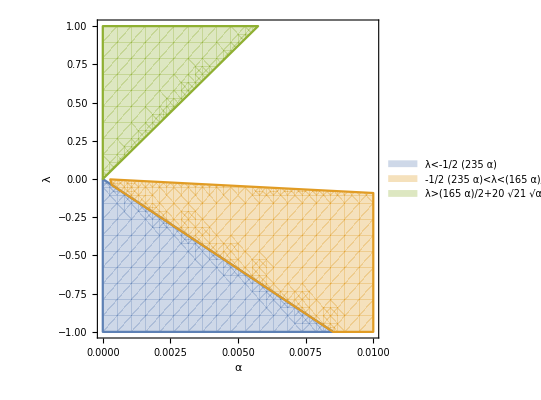

```mathematica
RegionPlot[{λ<-(235 α)/2,-(235 α)/2<λ<(165 α)/2-20 √21 √(α^2),λ>(165 α)/2+20 √21 √(α^2)},{α,0,0.01},{λ,-1,1},FrameLabel->{α,λ},PlotLegends->"Expressions"]
```